## Common Elements

```mathematica
Needs["HEPMath`"]
DeclareLorentzVectors[l,_p];

(* debug tools *)
getAllSymbols=e↦ DeleteDuplicates[Reap[Map[If[Head[#]==Symbol,Sow[#]]&,e,Infinity]][[2]][[1]]];
```

DeclareHEPTensor::redecl: HEPTensor l already declared.

```mathematica
f1=m@1^2-m@0^2-Sqr[p@1];
f2=m@2^2-m@1^2-Sqr[p@1+p@2]+Sqr[p@1];
f3=m@3^2-m@2^2-Sqr[p@1+p@2+p@3]+Sqr[p@1+p@2];

argsB=argsB01=Sequence[p@1,m@0,m@1];
argsB02=Sequence[p@1+p@2,m@0,m@2];
argsB03=Sequence[p@1+p@2+p@3,m@0,m@3];
argsB12=Sequence[p@2,m@1,m@2];
argsB13=Sequence[p@2+p@3,m@1,m@3];
argsB23=Sequence[p@3,m@2,m@3];
argsC=argsC012=Sequence[p@1,p@2,m@0,m@1,m@2];
argsC013=Sequence[p@1,p@2+p@3,m@0,m@1,m@3];
argsC023=Sequence[p@1+p@2,p@3,m@0,m@2,m@3];
argsC123=Sequence[p@2,p@3,m@1,m@2,m@3];
argsD=Sequence[p@1,p@2,p@3,m@0,m@1,m@2,m@3];
```

```mathematica
repVecs={
Sqr[p@1]-> p12,Sqr[p@2]-> p22,Sqr[p@3]-> p32,
SDot[p@1,p@2]-> sp12,SDot[p@1,p@3]-> sp13,SDot[p@2,p@3]-> sp23,
SDot[p@1+p@2,p@3]-> sp13+sp23,SDot[p@1,p@2+p@3]-> sp12+sp13,
Sqr[p@1+p@2]-> p12+p22+2sp12,Sqr[p@1+p@3]-> p12+p32+2sp13,Sqr[p@2+p@3]-> p22+p32+2sp23,
Sqr[p@1+p@2+p@3]-> p12+p22+p32+2sp12+2sp13+2sp23
};
Module[{l,t},Do[l=HEPExpand[First@e]/.repVecs;t=Simplify[l-Last@e];If[Not[t===0],Print[e, "is not consinstent! ",l]],{e,repVecs}]]
repMasses={m@0-> Sqrt@m02,m@1-> Sqrt@m12,m@2-> Sqrt@m22,m@3-> Sqrt@m32};
cmp[a_,b_]:=Simplify[Expand[(a-b)//.repVecs//.repMasses/.{Dim->4+ϵ}]];
getScalars[x_]:=Module[{l},
l=Reap[x/.{
rA[0][a__]:> Sow[rA[0][a]],
rB[0][a__]:> Sow[rB[0][a]],
rC[0][a__]:> Sow[rC[0][a]],
rD[0][a__]:> Sow[rD[0][a]]
}];
DeleteDuplicates[l[[2,1]]]
];
cmp2[a_,b_]:=Module[{x,y,l,lx,ly,ls,l2},
x=Identity[a//.repVecs//.repMasses];
y=Identity[b//.repVecs//.repMasses];
l=getScalars[x];
lx=Coefficient[x,l];
ly=Coefficient[y,l];
If[Length[lx]≠Length[ly],Return[$Failed]];
ls=lx-ly;
ls=ParallelMap[Together,ls];
l2=Select[ls,Not[0==#]&];
If[Length@l2==0,0,{l,l2}]
]
collectScalars[x_]:=collectScalars[x,e↦Simplify@HEPExpand[e]]
collectScalars[x_,f_Function]:=Collect[x,getScalars[x],f]
```

## Passarino-Veltman Decomposition

### bubble functions B

```mathematica
Clear[rB];
SetAttributes[rB,Orderless];

rB[1]={q,m0,m1}↦Evaluate[collectScalars[(1/(2Sqr[p@1])(f1 rB[0][argsB]+rA[0][m@0]-rA[0][m@1]))]/.{p@1-> q,m@0-> m0,m@1-> m1}];
rB[0,0]={q,m0,m1}↦Evaluate[collectScalars[(1/(2(Dim-1))(2m@0^2 rB[0][argsB]+rA[0][m@1]-f1 rB[1][argsB]))]/.{p@1-> q,m@0-> m0,m@1-> m1}];
rB[1,1]={q,m0,m1}↦Evaluate[collectScalars[(1/(2Sqr[p@1])(f1 rB[1][argsB]+rA[0][m@1]-2rB[0,0][argsB]))]/.{p@1-> q,m@0-> m0,m@1-> m1}];
```

### triangle functions C

```mathematica
Xc=Table[SDot[p[j],p[k]],{j,2},{k,2}];
iXc=Inverse@Xc;
SetAttributes[rC,Orderless];
```

```mathematica
Module[{S,i},
S={
1/2(f1 rC[0][argsC]+rB[0][argsB02]-rB[0][argsB12]), (* =Subscript[R, 1] *)
1/2(f2 rC[0][argsC]+rB[0][argsB01]-rB[0][argsB02])  (* =Subscript[R, 2] *)
};
i=iXc.S;
rC[1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
]
```

```mathematica
Module[{S00,S11,S12,S21,S22,i1,i2,t},
S00=rB[0][argsB12]+m@0^2 rC[0][argsC];
S11=1/2(f1 rC[1][argsC]+rB[1][argsB02]+rB[0][argsB12]); (* =Subscript[R, 3] *)
S12=1/2(f2 rC[1][argsC]+rB[1][argsB01]-rB[1][argsB02]); (* =Subscript[R, 4] *)
S21=1/2(f1 rC[2][argsC]+rB[1][argsB02]-rB[1][argsB12]); (* =Subscript[R, 5] *)
S22=1/2(f2 rC[2][argsC]-rB[1][argsB02]); (* =Subscript[R, 6] *)

rC[0,0]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[1/(Dim-2)(S00-S11-S22)]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
i1=iXc.{S11-rC[0,0][argsC],S12};
rC[1,1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i1[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[1,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i1[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
i2=iXc.{S21,S22-rC[0,0][argsC]};
rC[2,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i2[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];

Print["cross check C_21: ",cmp2[i2[[1]],rC[2,1][argsC]]];
]
```

cross check C_21: 0

```mathematica
Module[{S,i0,i1,i2},
S[0,0,1]=1/2(f1 rC[0,0][argsC]+rB[0,0][argsB02]-rB[0,0][argsB12]); (* =Subscript[R, 10] *)
S[0,0,2]=1/2(f2 rC[0,0][argsC]+rB[0,0][argsB01]-rB[0,0][argsB02]); (* =Subscript[R, 11] *)
i0 = iXc.{S[0,0,1],S[0,0,2]};
rC[0,0,1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i0[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[0,0,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i0[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];

S[1,1,1]=1/2(f1 rC[1,1][argsC]+rB[1,1][argsB02]-rB[0][argsB12]); (* =Subscript[R, 12] *)
S[1,1,2]=1/2(f2 rC[1,1][argsC]+rB[1,1][argsB01]-rB[1,1][argsB02]); (* =Subscript[R, 13] *)
i1 = iXc.{S[1,1,1]-2rC[0,0,1][argsC],S[1,1,2]};
rC[1,1,1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i1[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[1,1,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i1[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];

S[2,2,1]=1/2(f1 rC[2,2][argsC]+rB[1,1][argsB02]-rB[1,1][argsB12]); (* =Subscript[R, 14] *)
S[2,2,2]=1/2(f2 rC[2,2][argsC]-rB[1,1][argsB02]); (* =Subscript[R, 15] *)
i2 = iXc.{S[2,2,1],S[2,2,2]-2rC[0,0,2][argsC]};
rC[2,2,1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i2[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[2,2,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i2[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
]
```

```mathematica
Module[{S,i12},
S[1,2,1]=1/2(f1 rC[1,2][argsC]+rB[1,1][argsB02]+rB[1][argsB12]); (* =Subscript[R, 16] *)
S[1,2,2]=1/2(f2 rC[1,2][argsC]-rB[1,1][argsB02]); (* =Subscript[R, 17] *)
i12 = iXc.{S[1,2,1]-rC[0,0,2][argsC],S[1,2,2]-rC[0,0,1][argsC]};
Print["cross check C_121: ",cmp2[i12[[1]],rC[1,1,2][argsC]]];
Print["cross check C_122: ",cmp2[i12[[2]],rC[1,2,2][argsC]]];
]
```

cross check C_121: 0

cross check C_122: 0

### box function D

```mathematica
Xd=Table[SDot[p[j],p[k]],{j,3},{k,3}];
iXd=Inverse@Xd;
SetAttributes[rD,Orderless];
```

```mathematica
Module[{T,i},
T={
1/2(f1 rD[0][argsD]+rC[0][argsC023]-rC[0][argsC123]), (* =Subscript[R, 20] *)
1/2(f2  rD[0][argsD]+rC[0][argsC013]-rC[0][argsC023]), (* =Subscript[R, 21] *)
1/2(f3  rD[0][argsD]+rC[0][argsC012]-rC[0][argsC013]) (* =Subscript[R, 22] *)
};
i=iXd.T;
rD[1]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[1]]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[2]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[2]]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[3]]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
]
```

```mathematica
Module[{T,i1,i2,i3},
T[0,0]=m@0^2 rD[0][argsD]+rC[0][argsC123];

T[1,1]=1/2(f1 rD[1][argsD]+rC[1][argsC023]+rC[0][argsC123]);(* =Subscript[R, 30] *)
T[1,2]=1/2(f2 rD[1][argsD]+rC[1][argsC013]-rC[1][argsC023]);(* =Subscript[R, 31] *)
T[1,3]=1/2(f3 rD[1][argsD]+rC[1][argsC012]-rC[1][argsC013]);(* =Subscript[R, 32] *)

T[2,1]=1/2(f1 rD[2][argsD]+rC[1][argsC023]-rC[1][argsC123]);(* =Subscript[R, 33] *)
T[2,2]=1/2(f2 rD[2][argsD]+rC[2][argsC013]-rC[1][argsC023]); (* =Subscript[R, 34] *)
T[2,3]=1/2(f3 rD[2][argsD]+rC[2][argsC012]-rC[2][argsC013]); (* =Subscript[R, 35] *)

T[3,1]=1/2(f1 rD[3][argsD]+rC[2][argsC023]-rC[2][argsC123]); (* =Subscript[R, 36] *)
T[3,2]=1/2(f2 rD[3][argsD]+rC[2][argsC013]-rC[2][argsC023]); (* =Subscript[R, 37] *)
T[3,3]=1/2(f3 rD[3][argsD]-rC[2][argsC013]); (* =Subscript[R, 38] *)

PrintTemporary[{0,0}];
rD[0,0]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[1/(Dim-3)(T[0,0]-T[1,1]-T[2,2]-T[3,3])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary[{1,1}];
i1=iXd.{T[1,1]-rD[0,0][argsD],T[1,2],T[1,3]};
rD[1,1]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i1[[1]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[1,2]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i1[[2]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[1,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i1[[3]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary[{2,2}];
i2=iXd.{T[2,1],T[2,2]-rD[0,0][argsD],T[2,3]};
rD[2,2]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i2[[2]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[2,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i2[[3]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary[{3,3}];
i3=iXd.{T[3,1],T[3,2],T[3,3]-rD[0,0][argsD]};
rD[3,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i3[[3]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary["Checks"];
Print["cross check D_21: ",cmp2[i2[[1]],rD[2,1][argsD]]];
Print["cross check D_31: ",cmp2[i3[[1]],rD[3,1][argsD]]];
Print["cross check D_32: ",cmp2[i3[[2]],rD[3,2][argsD]]];
]
```

cross check D_21: 0

cross check D_31: 0

cross check D_32: 0

```mathematica
Module[{T,i12,f},
T[0,0,1]=1/2(f1 rD[0,0][argsD]+rC[0,0][argsC023]-rC[0,0][argsC123]); (* =Subscript[R, 40] *)
T[0,0,2]=1/2(f2 rD[0,0][argsD]+rC[0,0][argsC013]-rC[0,0][argsC023]); (* =Subscript[R, 41] *)
T[0,0,3]=1/2(f3 rD[0,0][argsD]+rC[0,0][argsC012]-rC[0,0][argsC013]); (* =Subscript[R, 42] *)

T[1,1,1]=1/2(f1 rD[1,1][argsD]+rC[1,1][argsC023]-rC[0][argsC123]); (* =Subscript[R, 43] *)
T[1,1,2]=1/2(f2 rD[1,1][argsD]+rC[1,1][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 44] *)
T[1,1,3]=1/2(f3 rD[1,1][argsD]+rC[1,1][argsC012]-rC[1,1][argsC013]); (* =Subscript[R, 45] *)

T[2,2,1]=1/2(f1 rD[2,2][argsD]+rC[1,1][argsC023]-rC[1,1][argsC123]); (* =Subscript[R, 46] *)
T[2,2,2]=1/2(f2 rD[2,2][argsD]+rC[2,2][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 47] *)
T[2,2,3]=1/2(f3 rD[2,2][argsD]+rC[2,2][argsC012]-rC[2,2][argsC013]); (* =Subscript[R, 48] *)

T[3,3,1]=1/2(f1 rD[3,3][argsD]+rC[2,2][argsC023]-rC[2,2][argsC123]); (* =Subscript[R, 49] *)
T[3,3,2]=1/2(f2 rD[3,3][argsD]+rC[2,2][argsC013]-rC[2,2][argsC023]); (* =Subscript[R, 50] *)
T[3,3,3]=1/2(f3 rD[3,3][argsD]-rC[2,2][argsC013]); (* =Subscript[R, 51] *)

T[1,2,1]=1/2(f1 rD[1,2][argsD]+rC[1,1][argsC023]+rC[1][argsC123]); (* =Subscript[R, 52] *)
T[1,2,2]=1/2(f2 rD[1,2][argsD]+rC[1,2][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 53] *)
T[1,2,3]=1/2(f3 rD[1,2][argsD]+rC[1,2][argsC012]-rC[1,2][argsC013]); (* =Subscript[R, 54] *)

f=e↦(*Together@*)e;

Do[Module[{v,i},
v={T[n,n,1],T[n,n,2],T[n,n,3]};
If[n>0,v[[n]]-=2rD[0,0,n][argsD]];
i = iXd.v;
PrintTemporary[{n,n,1}];
rD[n,n,1]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[1]],f]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
PrintTemporary[{n,n,2}];
rD[n,n,2]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[2]],f]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
PrintTemporary[{n,n,3}];
rD[n,n,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[3]],f]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
],{n,0,3}];

i12= iXd.{T[1,2,1]-rD[0,0,2][argsD],T[1,2,2]-rD[0,0,1][argsD],T[1,2,3]};
PrintTemporary[{1,2,3}];
rD[1,2,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i12[[3]],f]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary["Checks"];
Print["cross check D_121: ",cmp2[i12[[1]],rD[1,2,1][argsD]]];
Print["cross check D_122: ",cmp2[i12[[2]],rD[1,2,2][argsD]]];
]
```

cross check D_121: 0

cross check D_122: 0

```mathematica
Module[{T,i13,i23,a,b},
T[1,3,1]=1/2(f1 rD[1,3][argsD]+rC[1,2][argsC023]+rC[2][argsC123]); (* =Subscript[R, 55] *)
T[1,3,2]=1/2(f2 rD[1,3][argsD]+rC[1,2][argsC013]-rC[1,2][argsC023]); (* =Subscript[R, 56] *)
T[1,3,3]=1/2(f3 rD[1,3][argsD]-rC[1,2][argsC013]); (* =Subscript[R, 57] *)

T[2,3,1]=1/2(f1 rD[2,3][argsD]+rC[1,2][argsC023]-rC[1,2][argsC123]); (* =Subscript[R, 58] *)
T[2,3,2]=1/2(f2 rD[2,3][argsD]+rC[2,2][argsC013]-rC[1,2][argsC023]); (* =Subscript[R, 59] *)
T[2,3,3]=1/2(f3 rD[2,3][argsD]-rC[2,2][argsC013]); (* =Subscript[R, 60] *)

i13= iXd.{T[1,3,1]-rD[0,0,3][argsD],T[1,3,2],T[1,3,3]-rD[0,0,1][argsD]};
i23= iXd.{T[2,3,1],T[2,3,2]-rD[0,0,3][argsD],T[2,3,3]-rD[0,0,2][argsD]};

a=i13[[1]];
b=rD[1,3,1][argsD];

Print["cross check D_131: ",cmp2[i13[[1]],rD[1,3,1][argsD]]];
Print["cross check D_132: ",cmp2[i13[[2]],rD[1,3,2][argsD]]];
Print["cross check D_133: ",cmp2[i13[[3]],rD[1,3,3][argsD]]];
Print["cross check D_231: ",cmp2[i23[[1]],rD[2,3,1][argsD]]];
Print["cross check D_232: ",cmp2[i23[[2]],rD[2,3,2][argsD]]];
Print["cross check D_233: ",cmp2[i23[[3]],rD[2,3,3][argsD]]];
]
```

cross check D_131: 0

cross check D_132: 0

cross check D_133: 0

cross check D_231: 0

cross check D_232: 0

$Aborted

### parse

```mathematica
Module[{rT,getPaVeIndexList,args},
(* prepare data *)
rT[2]=rB;
getPaVeIndexList[2]:= {{1},{0,0},{1,1}};
args[2]=argsB;
rT[3]=rC;
getPaVeIndexList[3]:= {{1},{2},
{0,0},{1,1},{1,2},{2,2},
{0,0,1},{0,0,2},{1,1,1},{1,1,2},{2,2,1},{2,2,2}};
args[3]=argsC;
rT[4]=rD;
getPaVeIndexList[4]:= {{1},{2},{3},
{0,0},{1,1},{1,2},{1,3},{2,2},{2,3},{3,3},
{0,0,1},{0,0,2},{0,0,3},{1,1,1},{1,1,2},{1,1,3},{1,2,3},{2,2,1},{2,2,2},{2,2,3},{3,3,1},{3,3,2},{3,3,3}};
args[4]=argsD;
(* provide function *)
parsePaVe[j_,f_:FullSimplify]:=Module[{inds,t,ls,cs},
inds=getPaVeIndexList[j];
(* run *)
Do[
PrintTemporary[{j,i}];
t=(rT[j])[i/.List-> Sequence][args[j]];
ls=getScalars[t];
cs=Coefficient[t,ls];
(* rewrite *)
ls=ls/.{
rA[0][m0_]:> pA[0][m0^2],
rB[0][q1_,m0_,m1_]:> pB[0][Sqr[q1],m0^2,m1^2],
rC[0][q1_,q2_,m0_,m1_,m2_]:>pC[0][Sqr[q1],Sqr[q2],Sqr[q1+q2],m0^2,m1^2,m2^2],
rD[0][q1_,q2_,q3_,m0_,m1_,m2_,m3_]:> pD[0][Sqr[q1],Sqr[q2],Sqr[q3],Sqr[q1+q2+q3],Sqr[q1+q2],Sqr[q2+q3],m0^2,m1^2,m2^2,m3^2]
};
(* remove vectors *)
{cs,ls}= {cs,ls}//.repMasses//.repVecs;
{cs,ls}={cs,ls}//.{
sp12-> (p122-p12-p22)/2,
sp23-> (p232-p22-p32)/2,
sp13-> (p42-p122-p232+p22)/2
};
cs=ParallelMap[f ,cs];
Switch[j,
2,pB[i/.List-> Sequence]={q12,n02,n12}↦Evaluate[{cs,ls}/.{p12-> q12,m02-> n02,m12-> n12}],
3,pC[i/.List-> Sequence]={q12,q22,q122,n02,n12,n22}↦Evaluate[{cs,ls}/.{p12-> q12,p22-> q22,p122-> q122,m02-> n02,m12-> n12,m22-> n22}],
4,pD[i/.List-> Sequence]={q12,q22,q32,q42,q122,q232,n02,n12,n22,n32}↦Evaluate[{cs,ls}/.{p12-> q12,p22-> q22,p32-> q32,p42-> q42,p122-> q122,p232-> q232,m02-> n02,m12-> n12,m22-> n22,m32-> n32}]
]
,{i,inds}];
]
]
```

```mathematica
SetAttributes[pB,Orderless];
parsePaVe[2]
```

```mathematica
SetAttributes[pC,Orderless];
parsePaVe[3,Simplify@Together@#&]
```

```mathematica
SetAttributes[pD,Orderless];
parsePaVe[4,Identity]
```

### Check to Marco

```mathematica
Module[{r,map,a,b,d},
<<"~/Physik/PhD/Marco/PaVe/tensor_C.m";
r={S-> SDot,a0-> rA[0],b0-> rB[0],c0-> rC[0],n-> Dim};
map={
c11-> 1,
c12-> 2,
c24->{0,0},
c21-> {1,1},
c22-> {2,2},
c23-> {1,2},
c31-> {1,1,1},
c32-> {2,2,2},
c33-> {1,1,2},
c34-> {1,2,2},
c35-> {0,0,1},
c36-> {0,0,2}
};
Do[
a=((First@e)[argsC]/.r);
b=rC[(Last@e)/.{List-> Sequence}][argsC];
Print[Last@e,": ",cmp2[a,b]];
,{e,map}]
]
```

1: 0

2: 0

{0,0}: 0

{1,1}: 0

{2,2}: 0

{1,2}: 0

{1,1,1}: 0

{2,2,2}: 0

{1,1,2}: 0

{1,2,2}: 0

{0,0,1}: 0

{0,0,2}: 0

```mathematica
Module[{r,map,a,b,ca,cb,d},
<<"~/Physik/PhD/Marco/PaVe/tensor_D.m";
r={S-> SDot,a0-> rA[0],b0-> rB[0],c0-> rC[0],d0-> rD[0],n-> Dim};
map={
d11-> 1,
d12-> 2,
d13-> 3,
d21-> {1,1},
d22-> {2,2},
d23-> {3,3},
d24-> {1,2},
d25-> {1,3},
d26-> {2,3},
d27-> {0,0},
d31-> {1,1,1},
d32-> {2,2,2},
d33-> {3,3,3},
d34-> {1,1,2},
d35-> {1,1,3},
d36-> {1,2,2},
d37->{1,3,3},
d38-> {2,2,3},
(*d39->{2,3,3},*)
d310-> {1,2,3},
d311-> {0,0,1},
d312-> {0,0,2},
d313-> {0,0,3}
};
Do[
a=((First@e)[argsD]/.r);
b=rD[(Last@e)/.{List-> Sequence}][argsD];
Print[Last@e,": ",cmp2[a,b]];
,{e,map}]
]
```

1: 0

2: 0

3: 0

{1,1}: 0

{2,2}: 0

{3,3}: 0

{1,2}: 0

{1,3}: 0

{2,3}: 0

{0,0}: 0

{1,1,1}: 0

{2,2,2}: 0

{3,3,3}: 0

{1,1,2}: 0

{1,1,3}: 0

{1,2,2}: 0

{1,3,3}: 0

{2,2,3}: 0

{1,2,3}: 0

{0,0,1}: 0

{0,0,2}: 0

{0,0,3}: 0

### Export

```mathematica
Save["~/Physik/PhD/MMa/data/rT.m",{rB,rC,rD}];
```

```mathematica
<<"~/Physik/PhD/MMa/data/rT.m";
```

```mathematica
Save["~/Physik/PhD/MMa/data/pT.m",{pB,pC,pD}];
```

```mathematica
<<"~/Physik/PhD/MMa/data/pT.m";
```

## Scalar Integrals

```mathematica
Block[{$ContextPath,PaVe,Li2,s,A0,B0,C0,D0},
(*$ContextPath=Select[$ContextPath,Not@(StringLength[#]≥StringLength["HEPMath`"]&& StringTake[#,StringLength["HEPMath`"]]== "HEPMath`")&];*)
Module[{LTLink,tP,a,b,c,args},
tP={m2-> 1.,μ2-> m2,s-> 20.,q2->-2.,t-> -1.+m2};
args=Sequence[1,0,0];
LTLink=Install["LoopTools"];
LoopTools`SetMudim[μ2//.tP];
LoopTools`SetLambda[-2];
a=LoopTools`B0[args];
LoopTools`SetLambda[-1];
b=LoopTools`B0[args];
LoopTools`SetLambda[0];
c=LoopTools`B0[args];
Uninstall[LTLink];
Print[a/ϵL^2+b/ϵL+c];
]
]
```

PaVe::shdw: Symbol "PaVe" appears in multiple contexts {"LoopTools`", "HEPMath`PaVe`"}; definitions in context "LoopTools`" may shadow or be shadowed by other definitions.

Li2::shdw: Symbol "Li2" appears in multiple contexts {"LoopTools`", "Global`"}; definitions in context "LoopTools`" may shadow or be shadowed by other definitions.

s::shdw: Symbol "s" appears in multiple contexts {"LoopTools`", "Global`"}; definitions in context "LoopTools`" may shadow or be shadowed by other definitions.

A0::shdw: Symbol "A0" appears in multiple contexts {"LoopTools`", "Global`"}; definitions in context "LoopTools`" may shadow or be shadowed by other definitions.

C0::shdw: Symbol "C0" appears in multiple contexts {"LoopTools`", "Global`"}; definitions in context "LoopTools`" may shadow or be shadowed by other definitions.

D0::shdw: Symbol "D0" appears in multiple contexts {"LoopTools`", "Global`"}; definitions in context "LoopTools`" may shadow or be shadowed by other definitions.

(2.+3.14159 ⅈ)+1./ϵL

### A_0

```mathematica
sA0[m2]:=m2(-2/ϵ+1);
sA0[0]:=0;
```

```mathematica
Module[{fBeen2Den,Cϵ,A0Den},
fBeen2Den=(2π)^4/(I π^2);
Cϵ[m2_,μ2_]:=1/(16π^2)Exp[ϵ/2(EulerGamma-Log[4π])](m2/μ2)^(ϵ/2);
A0Den=-m2(m2/(4π μ2))^(ϵ/2)Gamma[-1-ϵ/2];
Print@Simplify@Series[A0Den,{ϵ,0,0}];
Print[Series[I Cϵ[m2,μ2] sA0[μ2][m2],{ϵ,0,0}]];
Print@FullSimplify[Series[A0Den,{ϵ,0,2}]-Series[fBeen2Den*I Cϵ[m2,μ2] sA0[μ2][m2],{ϵ,0,1}]];
]
```

-(2 m2)/ϵ-m2 (-1+EulerGamma-Log[4 π]+Log[m2/μ2])+O[ϵ]^1

-(ⅈ m2)/(8 π^2 ϵ)-(ⅈ m2 (-1+EulerGamma-Log[4 π]+Log[m2/μ2]))/(16 π^2)+O[ϵ]^1

-1/24 (m2 (12+π^2)) ϵ+O[ϵ]^2

### B_0

```mathematica
sB0[s,m2,m2]:=(-2/ϵ+2+β Log[χ]);
sB0[q2-t1-u1,m2,m2]:=sB0[μ2][s,m2,m2];
sB0[q2,m2,m2]:=(-2/ϵ+2+βq Log[χq]);
sB0[0,m2,m2]:=(-2/ϵ);
sB0[m2,0,m2]:=(-2/ϵ+2);
sB0[t,0,m2]:=(-2/ϵ+2-(t-m2)/t Log[-(t-m2)/m2]);
sB0[t1+m2,0,m2]:=sB0[μ2][t,0,m2];
sB0[t,m2,0]:=sB0[μ2][t,0,m2];
sB0[t1+m2,m2,0]:=sB0[μ2][t,m2,0];
sB0[u,0,m2]:=(sB0[μ2][t,0,m2]/.{t-> u});
sB0[u1+m2,0,m2]:=sB0[μ2][u,0,m2];
sB0[u,m2,0]:=sB0[μ2][u,0,m2];
sB0[u1+m2,m2,0]:=sB0[μ2][u,m2,0];
sB0[0,0,0]=0;
```

#### Computation

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((2m2-p2)/m2) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m2/μ2]-m2/p2(1/r-r)Log@r;
Print@FullSimplify[B0/.rSol//.{p2-> s,s-> 4m2/ρ,ρ-> 1-β^2},Assumptions-> {0<β<1,m2>0}];
]
```

{{r→-(-2 m2+p2-√(-4 m2 p2+p2^2))/(2 m2)},{r→-(-2 m2+p2+√(-4 m2 p2+p2^2))/(2 m2)}}

{2-EulerGamma-2/ϵ+Log[4]+Log[π]+β Log[(-1+β)/(1+β)]-Log[m2/μ2],2-EulerGamma-2/ϵ+Log[4]+Log[π]-β Log[(1+β)/(-1+β)]-Log[m2/μ2]}

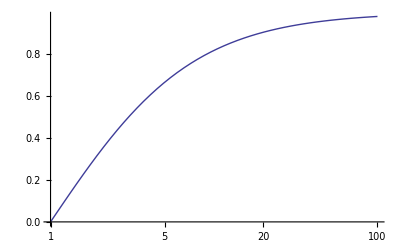

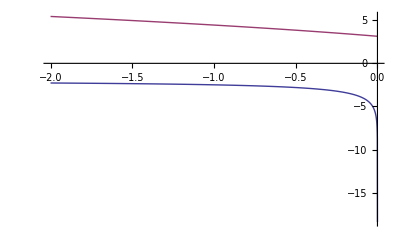

```mathematica
LogLinearPlot[-(1-b)/(1+b),{b,1,100}]
Plot[{Re@(b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-r]},Im@(b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-r]}},{r,-2,0}]
```

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((m0^2+m1^2-p2)/(m0 m1)) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m0 m1/μ2]+(m0^2-m1^2)/p2 Log[m1/m0]-m0 m1/p2(1/r-r)Log@r;
Print@Limit[B0/.rSol/.{m1-> Sqrt@m2,p2-> m2},m0-> 0,Assumptions-> {m2>0}];
]
```

{{r→(m0^2+m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)-p2)/(2 m0 m1)},{r→-(-m0^2-m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)+p2)/(2 m0 m1)}}

{2-EulerGamma-2/ϵ-Log[m2/(4 π μ2)],2-EulerGamma-2/ϵ-Log[m2/(4 π μ2)]}

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((m0^2+m1^2-p2)/(m0 m1)) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m0 m1/μ2]+(m0^2-m1^2)/p2 Log[m1/m0]-m0 m1/p2(1/r-r)Log@r;
Print@Expand@Limit[B0/.rSol/.{m1-> Sqrt@m2,p2-> t},m0-> 0,Assumptions-> {t<0,m2>0,t-m2<0}];
]
```

{{r→(m0^2+m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)-p2)/(2 m0 m1)},{r→-(-m0^2-m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)+p2)/(2 m0 m1)}}

{2-EulerGamma-2/ϵ-(m2 Log[m2])/(2 t)+Log[4 π]-Log[(m2-t)/(√m2)]+(m2 Log[(m2-t)/(√m2)])/t-Log[(√m2)/μ2],2-EulerGamma-2/ϵ+Log[4]-(m2 Log[m2])/t+(m2 Log[m2-t])/t-Log[(m2-t)/(π μ2)]}

```mathematica
Module[{i,r},
i=Integrate[Log[(p2 x^2-x(p2+m2)+m2)/μ2],x];
Print@i;
r=Limit[i,x-> 1,Assumptions-> {p2>0,m2>0,μ2>0}]-Limit[i,x-> 0,Assumptions-> {p2>0,m2>0,μ2>0}];
r=Simplify[r,Assumptions-> {p2>m2>0,μ2>0}];
Print@r;
]
```

-2 x-Log[1-x]-(m2 Log[m2-p2 x])/p2+x Log[((-1+x) (-m2+p2 x))/μ2]

-2-ⅈ π+(m2 Log[m2])/p2-(m2 Log[m2-p2])/p2+Log[-m2+p2]-Log[μ2]

### C_0

```mathematica
sC0[s,q2,0,m2,m2,m2]:=1/(s-q2)(1/2 Log[χ]^2-1/2 Log[χq]^2-3zeta2);
sC0[0,q2,s,m2,m2,m2]:=sC0[μ2][s,q2,0,m2,m2,m2];
sC0[0,q2,q2-t1-u1,m2,m2,m2]:=sC0[μ2][0,q2,s,m2,m2,m2];
sC0[q2,0,s,m2,m2,m2]:=sC0[μ2][s,q2,0,m2,m2,m2];
sC0[q2,0,q2-t1-u1,m2,m2,m2]:=sC0[μ2][q2,0,s,m2,m2,m2];
sC0[s,0,0,m2,m2,m2]:=1/(s-q2)(1/2 Log[χ]^2-3zeta2);
sC0[m2,0,t,0,m2,m2]:=1/(t-m2)(zeta2-PolyLog[2,t/m2]);
sC0[t,0,m2,0,m2,m2]:=sC0[μ2][m2,0,t,0,m2,m2];
sC0[t1+m2,0,m2,0,m2,m2]:=sC0[μ2][t,0,m2,0,m2,m2];
sC0[m2,0,u,0,m2,m2]:=(sC0[μ2][m2,0,t,0,m2,m2]/.{t-> u});
sC0[m2,0,u1+m2,0,m2,m2]:=sC0[μ2][m2,0,u,0,m2,m2];
sC0[m2,s,m2,0,m2,m2]:=(1/(s β)(-2/ϵ Log[χ]-2Log[χ]Log[1-χ]-2PolyLog[2,χ]+1/2Log[χ]^2-4zeta2));
sC0[m2,q2-t1-u1,m2,0,m2,m2]:=sC0[μ2][m2,s,m2,0,m2,m2];
sC0[t,m2,q2,0,m2,m2]:=((1/(Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))(
-zeta2+2 PolyLog[2,-((-m2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])/(m2-t))]+
PolyLog[2,(m2-q2+t-Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])/(m2-q2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])]+ PolyLog[2,(q2 (-3 m2+q2-t-Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/(-3 m2 q2+q2^2-q2 t+Sqrt[q2 (-4 m2+q2) (m2^2+(q2-t)^2-2 m2 (q2+t))])]- PolyLog[2,(q2 (-3 m2+q2-t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/(-3 m2 q2+q2^2-q2 t+Sqrt[q2 (-4 m2+q2) (m2^2+(q2-t)^2-2 m2 (q2+t))])]+ PolyLog[2,-((q2 (-3 m2+q2-t-Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/(3 m2 q2-q2^2+q2 t+Sqrt[q2 (-4 m2+q2) (m2^2+(q2-t)^2-2 m2 (q2+t))]))]- PolyLog[2,-((q2 (-3 m2+q2-t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/(3 m2 q2-q2^2+q2 t+Sqrt[q2 (-4 m2+q2) (m2^2+(q2-t)^2-2 m2 (q2+t))]))]- PolyLog[2,(m2^2-m2 (q2+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])-t (-q2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/((m2-t) (m2-q2+t-Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))]- PolyLog[2,(m2^2-m2 (q2+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])-t (-q2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/((m2-t) (m2-q2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))]));
sC0[m2,q2,t,0,m2,m2]:=sC0[μ2][t,m2,q2,0,m2,m2];
sC0[m2,q2,m2+t1,0,m2,m2]:=sC0[μ2][m2,q2,t,0,m2,m2];
sC0[t,q2,m2,0,m2,m2]:=sC0[μ2][t,m2,q2,0,m2,m2];
sC0[m2+t1,q2,m2,0,m2,m2]:=sC0[μ2][t,q2,m2,0,m2,m2];
sC0[u,m2,q2,0,m2,m2]:=(sC0[μ2][t,m2,q2,0,m2,m2]/.{t-> u});
sC0[m2,q2,u,0,m2,m2]:=sC0[μ2][u,m2,q2,0,m2,m2];
sC0[m2,q2,m2+u1,0,m2,m2]:=sC0[μ2][m2,q2,u,0,m2,m2];
sC0[u,q2,m2,0,m2,m2]:=sC0[μ2][u,m2,q2,0,m2,m2];
sC0[m2+u1,q2,m2,0,m2,m2]:=sC0[μ2][u,q2,m2,0,m2,m2];
sC0[0,m2,t,0,0,m2]:=1/(t-m2)(2/ϵ^2+2/ϵ Log[(m2-t)/m2]+Log[(m2-t)/m2]^2+PolyLog[2,t/m2] +zeta2/4);
sC0[0,t,m2,0,0,m2]:=sC0[μ2][0,m2,t,0,0,m2];
sC0[0,m2+t1,m2,0,0,m2]:=sC0[μ2][0,t,m2,0,0,m2];
sC0[0,m2,u,0,0,m2]:=(sC0[μ2][0,m2,t,0,0,m2]/.{t-> u})
sC0[0,m2,m2+u1,0,0,m2]:=sC0[μ2][0,m2,u,0,0,m2];
sC0[0,m2+u1,m2,0,0,m2]:=sC0[μ2][0,m2,m2+u1,0,0,m2];
```

```mathematica
κ[x_,y_,z_]:=Sqrt[x^2+y^2+z^2-2(x y +y z + z x)];
Series[κ[x2,m2,m2],{x2,0,1}]
```

2 √-m2 √x2+O[x2]^(3/2)

#### Computing C_0(s,q.b2,0,m.b2,m.b2,m.b2)

```mathematica
Limit[-PolyLog[2,2/(1-b)]-PolyLog[2,2/(1+b)],b-> ∞,Assumptions-> {m2>0}]
Limit[-PolyLog[2,(2 q2)/(q2-√(q2 (-4 m2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 m2+q2)))],q2-> 0,Assumptions-> {m2>0}]
```

0

0

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C},
p2[1]=p2[1,0]=s;
p2[2]=p2[2,0]=k2;
p2[2,1]=q2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
Print@Limit[αα,k2-> 0,Assumptions-> {s>0,s-q2>0}];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print[{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print@α[i];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print[{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print@Limit[y[0,i],k2->0,Assumptions-> {s>0,s-q2>0,M2>0}];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
C=Simplify@Limit[C,k2-> 0,Assumptions-> {s>4M2>0,q2<0,s-q2>0}];
Print@C;
Print@Simplify[C/.{s-> 4M2/ρ,q2-> 4M2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,βq≥0,M2>0}];
]
```

-q2+s

{0,1,2}

√(q2 (-4 M2+q2))

{(q2+√(q2 (-4 M2+q2)))/(2 q2),(q2-√(q2 (-4 M2+q2)))/(2 q2)}

0

{1,2,0}

√(k2 (k2-4 M2))

{(k2+√(k2 (k2-4 M2)))/(2 k2),(k2-√(k2 (k2-4 M2)))/(2 k2)}

q2/(q2-s)

{2,0,1}

√(s (-4 M2+s))

{(s+√(s (-4 M2+s)))/(2 s),(s-√(s (-4 M2+s)))/(2 s)}

1

(-PolyLog[2,(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(q2-√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(q2-√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(q2+√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(q2+√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(s-√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(s-√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(s+√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(s+√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))])/(√(k2^2+q2^2+s^2-2 (k2 q2+k2 s+q2 s)))

1/(q2-s)(-PolyLog[2,(2 q2)/(q2-√(q2 (-4 M2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 M2+q2)))]+PolyLog[2,(2 s)/(s-√(s (-4 M2+s)))]+PolyLog[2,(2 s)/(s+√(s (-4 M2+s)))])

-((-1+β^2) (-1+βq^2) (PolyLog[2,-2/(-1+β)]+PolyLog[2,2/(1+β)]-PolyLog[2,-2/(-1+βq)]-PolyLog[2,2/(1+βq)]))/(4 M2 (β^2-βq^2))

```mathematica
{PolyLog[2,2/(1+b)]+PolyLog[2,2/(1-b)],3Zeta@2-Log[x]^2/2}/.{x-> (1-b)/(1+b)}/.{b-> {.1,.3,.5,.7}}
{PolyLog[2,2/(1+b)]+PolyLog[2,2/(1-b)],-Log[xq]^2/2}/.{xq-> -(1-b)/(1+b)}/.{b-> {1.1,3.,5.,7.}}
```

{{4.91467-4.38675 ⅈ,4.7432-4.65146 ⅈ,4.33133-5.25895 ⅈ,3.43038-6.47055 ⅈ},{4.91467,4.7432,4.33133,3.43038}}

{{-4.63456,-0.240227,-0.082201,-0.0413805},{-4.63456,-0.240227,-0.082201,-0.0413805}}

```mathematica
Module[{K,iy,kx,iyx,r},
K=(1-β^2-4(1-x)x y)/(1-β^2);
Print@K;
iy=Integrate[1/K,y];
kx=FullSimplify[Limit[iy,y-> 1]-Limit[iy,y->0],Assumptions->{0<β<1}];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x];
r=FullSimplify[Limit[iyx,x->1]-Limit[iyx,x->0],Assumptions->{0<β<1}];
Print@Simplify[r*4m2/(s(1-β^2))];
]
```

(1-4 (1-x) x y-β^2)/(1-β^2)

((-1+β^2) (Log[-1+β^2]-Log[-1-4 (-1+x) x+β^2]))/(4 (-1+x) x)

-(m2 (-4 ArcTanh[β]^2+π (π-12 ⅈ Log[2]+2 ⅈ Log[1-β^2])))/(2 s)

```mathematica
Module[{a,b,c,K,iy,kx,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={0<ρ<1,ρq<0};
K=Simplify[(-a b *0-a c *s-b c q2+a m2+b m2+c m2)/m2/.{s-> 4m2/ρ,q2-> 4m2/ρq},Assumptions->assum];
Print@K;
iy=Integrate[1/K,y,Assumptions->assum];
kx=FullSimplify[Limit[iy,y-> 1,Assumptions->assum]-Limit[iy,y->0,Assumptions->assum],Assumptions->assum];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,x->1,Assumptions->assum]-Limit[iyx,x->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[r//.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,1≤ βq}];
]
```

(ρ ρq+4 x ((-1+y) ρ-y ρq)+4 x^2 (ρ-y ρ+y ρq))/(ρ ρq)

(ρ ρq (Log[ρ]-Log[(4 (-1+x) x+ρ) ρq]+Log[4 (-1+x) x+ρq]))/(4 (-1+x) x (ρ-ρq))

-1/(4 (ρ-ρq))ρ ρq (-Log[-1/2+x-(√(1-ρ))/2] Log[(2 (-1+x))/(-1+√(1-ρ))]-Log[x+1/2 (-1+√(1-ρ))] Log[(2-2 x)/(1+√(1-ρ))]+Log[1-x] Log[ρ]+Log[-1/2+x-(√(1-ρq))/2] Log[(2 (-1+x))/(-1+√(1-ρq))]+Log[x+1/2 (-1+√(1-ρq))] Log[(2-2 x)/(1+√(1-ρq))]+Log[-1+x] (Log[x+1/2 (-1+√(1-ρ))]+Log[-1/2+x-(√(1-ρ))/2]-Log[(-4 x+4 x^2+ρ) ρq])-Log[-1+x] (Log[x+1/2 (-1+√(1-ρq))]+Log[-1/2+x-(√(1-ρq))/2]-Log[-4 x+4 x^2+ρq])-PolyLog[2,(1-2 x+√(1-ρ))/(-1+√(1-ρ))]-PolyLog[2,(-1+2 x+√(1-ρ))/(1+√(1-ρ))]+PolyLog[2,(1-2 x+√(1-ρq))/(-1+√(1-ρq))]+PolyLog[2,(-1+2 x+√(1-ρq))/(1+√(1-ρq))])

-(ρ ρq (-4 ArcCoth[√(1-ρq)]^2+4 ArcTanh[√(1-ρ)]^2+π (3 π+8 ⅈ Log[2]-2 ⅈ Log[-(ρ (-2+2 √(1-ρq)+ρq))/ρq^2])))/(8 (ρ-ρq))

((-1+β^2) (-1+βq^2) (-4 ArcCoth[βq]^2+4 ArcTanh[β]^2+π (3 π+8 ⅈ Log[2]-2 ⅈ Log[(1-β^2)/(1+βq)^2])))/(8 (β^2-βq^2))

#### Computing C_0(m.b2,0,t,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=M2;
p2[2]=p2[2,0]=t;
p2[2,1]=k2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,t<0,t-M2<0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
C=Simplify@Limit[C,k2-> 0,Assumptions-> ass];
Print@C;
(*Print@Simplify[C/.{s-> 4M2/ρ,q2-> 4M2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,βq≥0,M2>0}];*)
]
```

α = M2-t

i,j,k = {0,1,2}

α_i: √(k2 (k2-4 M2))

x_(i±) = {(k2+√(k2 (k2-4 M2)))/(2 k2),(k2-√(k2 (k2-4 M2)))/(2 k2)}

y_(0  i) = -(M2+t)/(M2-t)

i,j,k = {1,2,0}

α_i: √((M2-t)^2)

x_(i±) = {(-M2+√((M2-t)^2)+t)/(2 t),-(M2+√((M2-t)^2)-t)/(2 t)}

y_(0  i) = -M2/t

i,j,k = {2,0,1}

α_i: 0

x_(i±) = {1,1}

y_(0  i) = 2

(π^2/3-PolyLog[2,(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-PolyLog[2,(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-2 PolyLog[2,(M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(√(k2^2+(M2-t)^2-2 k2 (M2+t)) (-1+(M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(√(k2^2+(M2-t)^2-2 k2 (M2+t)))))]-PolyLog[2,-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)) ((M2+√((M2-t)^2)-t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))/((M2+√((M2-t)^2)-t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-PolyLog[2,-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(-M2+√((M2-t)^2)+t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(-M2+√((M2-t)^2)+t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))])/(√(k2^2+M2^2+t^2-2 (k2 M2+k2 t+M2 t)))

(π^2-12 PolyLog[2,2]-6 PolyLog[2,M2/t]+6 PolyLog[2,(M2+t)/M2]+6 PolyLog[2,(M2+t)/t])/(6 M2-6 t)

```mathematica
Module[{a,b,c,y},
a=π^2/6-2PolyLog[2,2]-PolyLog[2,1/z]+PolyLog[2,1+z]+PolyLog[2,1+1/z];
b=π^2/6-2PolyLog[2,2]-(-PolyLog[2,z]-π^2/6-1/2Log[-z]^2)+
(-PolyLog[2,-z]+π^2/6-Log[-z]Log[1+z])+
(-PolyLog[2,-1/z]+π^2/6-Log[-1/z]Log[1+1/z]);
c=π^2 5/6-2PolyLog[2,2]+PolyLog[2,z]+1/2Log[-z]^2+1/2Log[z]^2-Log[-z]Log[1+z]+Log[-z]Log[1+1/z];
y=-(Zeta[2]-PolyLog[2,z]);
Do[Print[{a,b,c,y}/.{z-> vz}],{vz,{-1.1,-3.,-5.,-7.}}];
]
```

{-2.53577+4.35517 ⅈ,-2.53577+4.35517 ⅈ,-2.53577+4.35517 ⅈ,-2.53577}

{-3.58431+4.35517 ⅈ,-3.58431+4.35517 ⅈ,-3.58431+4.35517 ⅈ,-3.58431}

{-4.39421+4.35517 ⅈ,-4.39421+4.35517 ⅈ,-4.39421+4.35517 ⅈ,-4.39421}

{-5.0451+4.35517 ⅈ,-5.0451+4.35517 ⅈ,-5.0451+4.35517 ⅈ,-5.0451}

```mathematica
π^2/3-Log[2]^2/2-Sum[1/(k^2 2^k),{k,1,∞}]
N@PolyLog[2,2]
N[π^2/4-I π Log@2]
```

π^2/4

2.4674-2.17759 ⅈ

2.4674-2.17759 ⅈ

```mathematica
Module[{a,b,c,K,iy,kx,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={m2>0,t<0};
K=Simplify[(-a b *0-a c *m2-b c t+a 0+b m2+c m2)/m2,Assumptions->assum];
Print@K;
iy=Integrate[1/K,y,Assumptions->assum];
kx=FullSimplify[Limit[iy,y-> 1,Assumptions->assum]-Limit[iy,y->0,Assumptions->assum],Assumptions->assum];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,x->1,Assumptions->assum]-Limit[iyx,x->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[r//.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,1≤ βq}];
]
```

(t x (-1+x+y-x y)+m2 (1-2 x y+x^2 y))/m2

(m2 (Log[m2 (-1+x)^2]-Log[m2+t (-1+x) x]))/(x (t+m2 (-2+x)-t x))

1/(m2-t)m2 (2 Log[-m2 (-2+x)+t (-1+x)] Log[-1+x]-2 Log[2+(t (-1+x))/m2-x] Log[-1+x]-Log[-m2 (-2+x)+t (-1+x)] Log[m2 (-1+x)^2]-Log[-m2 (-2+x)+t (-1+x)] Log[-1/2-(√(t (-4 m2+t)))/(2 t)+x]-Log[-m2 (-2+x)+t (-1+x)] Log[-1/2+(√(t (-4 m2+t)))/(2 t)+x]+Log[-1/2-(√(t (-4 m2+t)))/(2 t)+x] Log[(2 t (t+m2 (-2+x)-t x))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]+Log[-1/2+(√(t (-4 m2+t)))/(2 t)+x] Log[-(2 t (t+m2 (-2+x)-t x))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))]+Log[-m2 (-2+x)+t (-1+x)] Log[m2+t (-1+x) x]-2 PolyLog[2,((m2-t) (-1+x))/m2]+PolyLog[2,-((m2-t) (-t-√(t (-4 m2+t))+2 t x))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]+PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))+2 t x))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

1/(m2-t)m2 (Log[2 m2-t] Log[-m2^2/t]-Log[m2] Log[((2 m2-t) (t-√(t (-4 m2+t))))/(2 t)]+ⅈ π Log[-(-2 m2+t+√(t (-4 m2+t)))/(2 m2^3)]+Log[-(t+√(t (-4 m2+t)))/(2 t)] Log[(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))/((2 m2-t) (-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t)))))]+Log[(t-√(t (-4 m2+t)))/(2 t)] Log[(m2 t (t+√(t (-4 m2+t)))-m2^2 (3 t+√(t (-4 m2+t))))/((2 m2-t) (3 m2 t-m2 √(t (-4 m2+t))+t (-t+√(t (-4 m2+t)))))]+2 PolyLog[2,-1+t/m2]+PolyLog[2,((m2-t) (2 m2-t+√(t (-4 m2+t))))/(2 m2^2)]+PolyLog[2,-((m2-t) (-2 m2+t+√(t (-4 m2+t))))/(2 m2^2)]-PolyLog[2,((m2-t) (t+√(t (-4 m2+t))))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]-PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

1/(m2-t)m2 (Log[2 m2-t] Log[-m2^2/t]-Log[m2] Log[((2 m2-t) (t-√(t (-4 m2+t))))/(2 t)]+ⅈ π Log[-(-2 m2+t+√(t (-4 m2+t)))/(2 m2^3)]+Log[-(t+√(t (-4 m2+t)))/(2 t)] Log[(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))/((2 m2-t) (-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t)))))]+Log[(t-√(t (-4 m2+t)))/(2 t)] Log[(m2 t (t+√(t (-4 m2+t)))-m2^2 (3 t+√(t (-4 m2+t))))/((2 m2-t) (3 m2 t-m2 √(t (-4 m2+t))+t (-t+√(t (-4 m2+t)))))]+2 PolyLog[2,-1+t/m2]+PolyLog[2,((m2-t) (2 m2-t+√(t (-4 m2+t))))/(2 m2^2)]+PolyLog[2,-((m2-t) (-2 m2+t+√(t (-4 m2+t))))/(2 m2^2)]-PolyLog[2,((m2-t) (t+√(t (-4 m2+t))))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]-PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

#### Computing C_0(m.b2,s,m.b2,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=M2;
p2[2]=p2[2,0]=s;
p2[2,1]=M2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
(*ϵ=0;*)
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,s>0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
(*C=Simplify@Limit[C,k2-> 0,Assumptions-> ass];
Print@C;*)
]
```

α = √(s (-4 M2+s))

i,j,k = {0,1,2}

α_i: √3 √(-M2^2) (1+ⅈ M2 ϵ$13014)

x_(i±) = {(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2),(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)}

y_(0  i) = (-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))

i,j,k = {1,2,0}

α_i: √((M2-s)^2) (1+ⅈ s ϵ$13014)

x_(i±) = {(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s),-(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)}

y_(0  i) = -((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))

i,j,k = {2,0,1}

α_i: 0

x_(i±) = {1,1}

y_(0  i) = (M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)))

1/(√(2 M2^2+s^2-2 (M2^2+2 M2 s)))(π^2/3-2 PolyLog[2,(M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)) (-1+(M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)))))]-PolyLog[2,(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)) ((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)))]+PolyLog[2,(-1+(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s))))/((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2))]-PolyLog[2,(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)) ((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)))]+PolyLog[2,(-1+(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s))))/((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2))]-PolyLog[2,-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)) (-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))+(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)))]+PolyLog[2,(-1-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s))))/(-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))+(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s))]-PolyLog[2,-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)) (-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))-(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)))]+PolyLog[2,(-1-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s))))/(-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))-(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s))])

```mathematica
Module[{a,b,c,K,ix,ky,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={m2>0,s>4m2,0<ρ<1,0<β<1,0<χ<1};
K=Simplify[(-a b *s-a c *m2-b c *m2+a m2+b *m2+c *0)/m2(*/.{s-> 4m2/ρ,q2-> 4m2/ρq}*),Assumptions->assum];
Print@K;
ix=Integrate[x K^(-1+ϵ/2),x,Assumptions->assum];
Print@ix;
ky=FullSimplify[Limit[ix,x-> 1,Assumptions->assum],Assumptions->assum];
ky=Simplify[Normal@Series[ky,{ϵ,0,0}]/.{s-> 4m2/ρ}/.{ρ-> 1-β^2}/.{β-> (1-χ)/(1+χ)}];
Print@ky;
iyx=Integrate[(-1/2)*2 ky,y,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,y->1,Assumptions->assum]-Limit[iyx,y->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[χ/(1-χ^2)/m2/.{χ-> (1-β)/(1+β)}/.{β-> Sqrt[1-ρ]}/.{ρ-> 4m2/s}];
Print@Collect[r/(χ/(1-χ^2)),ϵ,Simplify[#,Assumptions-> assum]&];
]
```

(x^2 (m2+s (-1+y) y))/m2

(x^2 ((x^2 (m2+s (-1+y) y))/m2)^(1/2 (-2+ϵ)))/ϵ

(χ (2+ϵ Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]))/(2 ϵ (χ-y (1+χ)^2+y^2 (1+χ)^2))

-1/(4 ϵ (-1+χ^2))χ (4 Log[y-χ+y χ]-2 ϵ Log[y-χ+y χ] Log[y-1/(1+χ)]-ϵ Log[y-1/(1+χ)]^2-2 ϵ Log[(-1+y+y χ)/(-1+χ)] Log[y-χ/(1+χ)]-2 ϵ Log[y-χ+y χ] Log[y-χ/(1+χ)]+ϵ Log[y-χ/(1+χ)]^2-4 Log[1-y (1+χ)]+2 ϵ Log[y-1/(1+χ)] Log[1-y (1+χ)]+2 ϵ Log[y-χ/(1+χ)] Log[1-y (1+χ)]+2 ϵ Log[y-1/(1+χ)] Log[(χ-y (1+χ))/(-1+χ)]+2 ϵ Log[y-χ+y χ] Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]-2 ϵ Log[1-y (1+χ)] Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]+2 ϵ PolyLog[2,(-1+y+y χ)/(-1+χ)]-2 ϵ PolyLog[2,(χ-y (1+χ))/(-1+χ)])

1/(2 ϵ (-1+χ^2))χ (π (4 ⅈ+π ϵ)+Log[χ] (4+2 ϵ Log[1-χ]-ϵ Log[χ])-2 ⅈ π ϵ Log[χ/(1+χ)]+2 ϵ PolyLog[2,1/(1-χ)]-2 ϵ PolyLog[2,χ/(-1+χ)])

1/(√(1-(4 m2)/s) s)

(-2 ⅈ π-2 Log[χ])/ϵ+1/2 (-π^2-2 Log[1-χ] Log[χ]+Log[χ]^2+2 ⅈ π Log[χ/(1+χ)]-2 PolyLog[2,1/(1-χ)]+2 PolyLog[2,χ/(-1+χ)])

```mathematica
Module[{a,b,z},
(*a=PolyLog[2,1/(1-x)];
b=PolyLog[2,x]-π^2/3+Log[x]Log[1-x]-1/2Log[x-1]^2;
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];
a=PolyLog[2,x/(x-1)];
b=-PolyLog[2,1/(1-x)]+π^2/6+Log[1-x](Log[x]-Log[x-1]);
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];*)
a=-2PolyLog[2,1/(1-x)]+2PolyLog[2,x/(x-1)];
b=-4PolyLog[2,x]-π^2/3-2Log[x]Log[1-x];
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];
]
```

{-4.18554+0.662 ⅈ,-4.18554}

{-5.45324+2.24105 ⅈ,-5.45324}

{-6.57974+4.35517 ⅈ,-6.57974}

{-7.70623+7.56478 ⅈ,-7.70623}

#### Computing C_0(t,q.b2,m.b2,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=t;
p2[2]=p2[2,0]=M2;
p2[2,1]=q2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,t<0,q2<0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
C=Simplify[C,Assumptions-> ass];
Print@C;
Print@Simplify[Limit[C,q2-> 0,Assumptions-> ass],Assumptions-> ass];
]
```

α = √(M2^2+(q2-t)^2-2 M2 (q2+t))

i,j,k = {0,1,2}

α_i: √(q2 (-4 M2+q2))

x_(i±) = {(q2+√(q2 (-4 M2+q2)))/(2 q2),(q2-√(q2 (-4 M2+q2)))/(2 q2)}

y_(0  i) = (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(2 √(M2^2+(q2-t)^2-2 M2 (q2+t)))

i,j,k = {1,2,0}

α_i: 0

x_(i±) = {0,0}

y_(0  i) = (M2-t)/(√(M2^2+(q2-t)^2-2 M2 (q2+t)))

i,j,k = {2,0,1}

α_i: √((M2-t)^2)

x_(i±) = {(M2+t+√((-M2+t)^2))/(2 t),(M2+t-√((-M2+t)^2))/(2 t)}

y_(0  i) = (M2 (-M2+q2)+t (-q2+t)+(M2+t) √(M2^2+(q2-t)^2-2 M2 (q2+t)))/(2 t √(M2^2+(q2-t)^2-2 M2 (q2+t)))

1/(6 √(M2^2+(q2-t)^2-2 M2 (q2+t)))(-π^2+12 PolyLog[2,-(-M2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(M2-t)]+6 PolyLog[2,(M2-q2+t-√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(M2-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))]+6 PolyLog[2,(q2 (-3 M2+q2-t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(-3 M2 q2+q2^2-q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(q2 (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(-3 M2 q2+q2^2-q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]+6 PolyLog[2,-(q2 (-3 M2+q2-t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(3 M2 q2-q2^2+q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,-(q2 (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(3 M2 q2-q2^2+q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(M2^2-M2 (q2+√(M2^2+(q2-t)^2-2 M2 (q2+t)))-t (-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/((M2-t) (M2-q2+t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(M2^2-M2 (q2+√(M2^2+(q2-t)^2-2 M2 (q2+t)))-t (-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/((M2-t) (M2-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))])

-(π^2-6 PolyLog[2,t/M2])/(6 M2-6 t)

### D_0

```mathematica
sD0[m2,0,0,m2,t,s,0,m2,m2,m2]:=1/(β s (t-m2))(
-2Log[χ]/ϵ-2Log[χ](Log[1-χ]-Log[1+χ]+Log[- (t-m2)/m2])+2PolyLog[2,-χ]-2PolyLog[2,χ]-3zeta2
);
sD0[m2,0,q2,m2,t,s,0,m2,m2,m2]:=1/(β s (t-m2))(
-2Log[χ]/ϵ-2Log[χ]Log[- (t-m2)/m2]-Log[χq]^2-3zeta2-2PolyLog[2,χ]-2PolyLog[2,-χ]-2Log[χ]Log[1+χ]-2Log[χ]Log[1-χ]+2PolyLog[2,-χ χq]+2PolyLog[2,-χ/χq]+2Log[χ χq]Log[1+χ χq]+2Log[χ/χq]Log[1+χ/χq]
);
sD0[m2,q2,0,m2,t1+m2,q2-t1-u1,0,m2,m2,m2]:=sD0[μ2][m2,0,q2,m2,t,s,0,m2,m2,m2];
sD0[m2,0,q2,m2,u,s,0,m2,m2,m2]:=(sD0[μ2][m2,0,q2,m2,t,s,0,m2,m2,m2]/.{t-> u});
sD0[m2,0,q2,m2,m2+u1,q2-t1-u1,0,m2,m2,m2]:=sD0[μ2][m2,0,q2,m2,u,s,0,m2,m2,m2];
sD0[0,m2,q2,m2,t,u,0,0,m2,m2]:=1/((t-m2) (u-m2))(
4/ϵ^2+2/ϵ(Log[(m2-t)/m2]+Log[(m2-u)/m2])+2Log[(m2-t)/m2]Log[(m2-u)/m2] -7/2 zeta2-Log[χq]^2
);
sD0[0,t,q2,u,m2,m2,0,0,m2,m2]:=sD0[μ2][0,m2,q2,m2,t,u,0,0,m2,m2];
sD0[0,m2+t1,q2,m2+u1,m2,m2,0,0,m2,m2]:=sD0[μ2][0,t,q2,u,m2,m2,0,0,m2,m2];
```

#### Computing D_0(m.b2,0,q.b2,m.b2,t,s,0,m.b2,m.b2,m.b2)

```mathematica
(*-2Log[χ]/ϵ-2Log[χ](Log[1-χ]-Log[1+χ]+Log[- (t-m2)/m2])+2PolyLog[2,-χ]-2PolyLog[2,χ]-3zeta2
+Log[(βq^2-β^2)/(βq-1)^2]Log[(βq-β)/(βq+β)]-2Log[χ]Log[1-q2/s]
+2PolyLog[2,(βq-1)/(βq-β)]+2PolyLog[2,(βq-β)/(βq+1)]-2PolyLog[2,(βq+β)/(βq+1)]-2PolyLog[2,(βq-1)/(βq+β)]*)
```

```mathematica
Module[{
assum,params,p,a,b,c,d,Jac,K,pK,repDiLogs,repLogs,
i1,uk1,lk1,
i2a,k2a,i3a,resa,
i2b,k2b,i3b,resb,DiLogsββqRep,
res,Pϵ,normUnits,
tP
},
(* setup data *)
Jac=x^2 y;
assum={m2>0,s>4m2,q2<0,s-q2>0,t<0,0<ρ<1,ρq<0,0<β<1,0<χ<1,tTil>0,βq>1};
K=Simplify[(-a b *m2-a c *t-a d*m2-b c*0-b d*s-c d q2+a*0+b *m2+c*m2+d*m2)/m2/.{s-> 4m2/ρ,q2-> 4m2/ρq,t-> m2(1-tTil)},Assumptions->assum];
(* choose parameterization *)
params=Permute[{x y z,x y(1-z),x(1-y),(1-x)},AlternatingGroup[4]];
p=params[[11]];
pK=K/.{a->p[[1]],b-> p[[2]],c->p[[3]],d-> p[[4]]};
normUnits=-(1-β^2)/(4tTil β);
(* integrate z *)
i1=Integrate[Jac*pK^(-2+ϵ/2),z,Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
uk1=FullSimplify[Limit[i1,z-> 1,Assumptions->assum],Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
lk1=FullSimplify[Limit[i1,z-> 0,Assumptions->assum],Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
Print["{uk1,lk1} = ",{uk1,lk1}];
(* split x integration: a *)
i2a=Integrate[lk1,x,Assumptions->assum];
Print["i2a = ",i2a];
k2a=Limit[i2a,x-> 1,Assumptions->assum];
Print["k2a = ",k2a];
k2a=k2a/.{Hypergeometric2F1[1,ϵ,1+ϵ,z_]:> 1-ϵ Log[Simplify[1-z,Assumptions->assum]]-ϵ^2PolyLog[2,Simplify[z,Assumptions->assum]]};
k2a=Normal@Series[k2a,{ϵ,0,0}];
i3a=Integrate[k2a,y];
resa=Simplify[(Limit[i3a,y-> 1,Assumptions->assum]-Limit[i3a,y-> 0,Assumptions->assum])/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions->assum];
Print["resa1 = ",resa];
Print[];

(* part b *)
uk1=Limit[uk1,ϵ->0,Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
i2b=Integrate[uk1,x];
k2b=Simplify[Limit[i2b,x-> 1,Assumptions->assum]-Limit[i2b,x-> 0,Assumptions->assum],Assumptions->assum];
i3b=Integrate[k2b,y];
resb=Simplify[(Limit[i3b,y-> 1,Assumptions->assum]-Limit[i3b,y-> 0,Assumptions->assum])/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions->assum];
resb=Collect[resb,ϵ,FullSimplify[TrigToExp@#,Assumptions->assum]&];
Print["resb2 = ",resb];
Print[];
tP={m2-> 1.,s-> 20.,t1-> -1.,q2-> -1.5};
Print["t: ",NIntegrate[uk1/.{ρ-> 4m2/s,ρq-> 4m2/q2,tTil-> -t1/m2}/.tP,{x,0,1},{y,0,1}]];
Print["t: ",resb/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]}/.{ρ-> 4m2/s,ρq-> 4m2/q2,tTil-> -t1/m2}/.tP];

(* simplify a *)
resa=Collect[resa/normUnits,ϵ,Expand@TrigToExp@FullSimplify[#,Assumptions->assum]&];
repDiLogs={
PolyLog[2,-2/(-1+β)]-PolyLog[2,2/(1+β)]-> (2PolyLog[2,-χ]+π^2/6+2Log[χ]Log[1+χ]-1/2Log[χ]^2),
-PolyLog[2,(-1+β)/(2 β)]+ PolyLog[2,(1+β)/(2 β)]->-(-2PolyLog[2,χ]-π^2/6-Log[χ]Log[1-χ])
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[l-r]/Re@l,l,r}/.{χ-> (1-β)/(1+β)}/.{β-> vβ};
If[Abs@First@lr>1*^-8,Print[e,lr]],{vβ,RandomReal[{0,1},5]}]
,{e,repDiLogs}]
];
resa=resa//.repDiLogs;
resa=FullSimplify[resa/.{β-> (1-χ)/(1+χ)},Assumptions->assum];
resa=resa/.{Log[a_*b_]:> Log[a]+Log[b],Log[a_/b_]:> Log[a]-Log[b]};
resa=Collect[resa,ϵ,FullSimplify];
repLogs={
Log[(tTil (-1+βq^2) (-1+χ^2))/((1+βq+(-1+βq) χ) (-1+βq+χ+βq χ))]-> Log[tTil]+Log[(-1+βq^2)(-1+χ^2)]-Log[(1+βq+(-1+βq) χ)]-Log[-1+βq+χ+βq χ],
-Log[1+βq+(-1+βq) χ]- Log[-1+βq+χ+βq χ]+Log[(-1+βq^2) (-1+χ^2)]->(Log[β]-Log[(βq^2-β^2)/(1-βq^2)]) (*2(Log[β]+Log[(1-βq^2)/(1-β^2)/βq^2]+x)*)
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[(l-r)]/Re@l,{l,r},{β,βq}}/.{χ-> (1-β)/(1+β)}/.{β-> vβ,βq-> vβq};
If[Abs@First@lr>1*^-8,Print[e,lr]],{vβ,RandomReal[{0,1},5]},{vβq,RandomReal[{1,10},5]}]
,{e,repLogs}]
];
resa=Collect[resa//.repLogs,ϵ,Simplify[Expand@#,Assumptions->assum]&];
Print["resa3 = ",resa];

(* simplify b *)
DiLogsββqRep={PolyLog[2,(-1+βq)/(-β+βq)]- PolyLog[2,(1+βq)/(-β+βq)]- PolyLog[2,(-1+βq)/(β+βq)]+PolyLog[2,(1+βq)/(β+βq)]-> DiLogsββq};
resb=resb/.DiLogsββqRep;
repDiLogs={
PolyLog[2,-2/(-1+β)]-PolyLog[2,2/(1+β)]-> (2PolyLog[2,-χ]+π^2/6+2Log[χ]Log[1+χ]-1/2Log[χ]^2)
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[(l-r)]/Re@l,{l,r},β}//.{χ-> (1-β)/(1+β)}/.{β-> vβ};
If[Abs@First@lr>1*^-8,Print[e,lr]],{vβ,RandomReal[{0,1},5]}]
,{e,repDiLogs}]
];
resb=resb//.repDiLogs;
resb=FullSimplify[resb/normUnits,Assumptions->assum];
Print["resb4 = ",resb];
repLogs={
Log[1-1/βq]-> Log[βq-1]-Log[βq],
Log[1+1/βq]-> Log[βq+1]-Log[βq],
Log[(-1+βq)/(1+βq)]->Log[-1+βq]-Log[1+βq],
Log[2/(-1+βq)] ->Log[2]-Log[βq-1],
Log[2/(1+βq)]->Log[2]-Log[1+βq],
Log[(χ*(1 + βq + (-1 + βq)*χ))/(-1 + βq + χ + βq*χ)]->Log[χ]+Log[(1 + βq + (-1 + βq)*χ)]-Log[(-1 + βq + χ + βq*χ)],
Log[(χ*(-1 + βq + χ + βq*χ))/(1 + βq + (-1 + βq)*χ)]->Log[χ]+Log[-1 + βq + χ + βq*χ]-Log[1 + βq + (-1 + βq)*χ],
Log[((1+βq+(-1+βq) χ) (-1+βq+χ+βq χ))/(4 χ)]->Log[1+βq+(-1+βq) χ]+Log[-1+βq+χ+βq χ]-2Log[2]-Log[χ],
Log[(-1+βq^2)/((1+βq+(-1+βq) χ) (-1+βq+χ+βq χ))]->Log[-1+βq^2]-Log[1+βq+(-1+βq) χ]-Log[-1+βq+χ+βq χ]
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[(l-r)]/Re@l,{l,r},{β,βq}}/.{χ-> (1-β)/(1+β)}/.{β-> vβ,βq-> vβq};
If[Abs@First@lr>1*^-8,Print[e,lr]],{vβ,RandomReal[{0,1},5]},{vβq,RandomReal[{1,10},5]}]
,{e,repLogs}]
];
resb=Expand@TrigToExp@FullSimplify[resb/.{β-> (1-χ)/(1+χ)},Assumptions->assum];
resb=Simplify[Expand[resb/.repLogs],Assumptions->assum];
Print["resb5 = ",resb];
repLogs={
4Log[χ]Log[1+χ]+2 Log[-1+βq^2] Log[χ]-2 Log[χ] Log[1+βq+(-1+βq) χ]-2 Log[χ] Log[-1+βq+χ+βq χ]+2 Log[-1+βq] Log[1+βq+(-1+βq) χ]-2 Log[1+βq] Log[1+βq+(-1+βq) χ]-2 Log[-1+βq] Log[-1+βq+χ+βq χ]+2 Log[1+βq] Log[-1+βq+χ+βq χ]-> 2Log[χq]Log[(βq+β)/(βq-β)]-2Log[χ]Log[1-ρ/ρq]
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[(l-r)]/Re@l,{l,r},{β,βq}}/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2}/.{β-> vβ,βq-> vβq};
If[Abs@First@lr>1*^-8,Print[e,lr]],{vβ,RandomReal[{0,1},5]},{vβq,RandomReal[{1,10},5]}]
,{e,repLogs}]
];
resb=Simplify[resb/.repLogs,Assumptions->assum];
Print["resb6 = ",resb];
resb=Expand[resb/.{Last@First@DiLogsββqRep-> First@First@DiLogsββqRep}];
repLogs={
2Log[χq]Log[(βq+β)/(βq-β)]-2PolyLog[2,(βq+1)/(βq-β)]+2PolyLog[2,(βq+1)/(βq+β)]->2PolyLog[2,(βq-β)/(βq+1)]-2PolyLog[2,(βq+β)/(βq+1)]+Log[(βq-β)/(βq+β)]Log[(βq^2-β^2)/(βq-1)^2]
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[(l-r)]/Re@l,{l,r},{β,βq}}/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2}/.{β-> vβ,βq-> vβq};
If[Abs@First@lr>1*^-8,Print[e,lr]],{vβ,RandomReal[{0,1},5]},{vβq,RandomReal[{1,10},5]}]
,{e,repLogs}]
];
resb=Simplify[resb/.repLogs/.{2I*Pi*Log[4]-> 0},Assumptions->assum];
Print["resb7 = ",resb];
Print["t: ",normUnits*resb/.{χ-> (1-β)/(1+β),χq-> (βq-1)/(βq+1)}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]}/.{ρ-> 4m2/s,ρq-> 4m2/q2,tTil-> -t1/m2}/.tP];
]
```

{uk1,lk1} = {(2 x ρ ρq ((x (tTil y ρq+x (ρq+y (-4+4 y-tTil ρq))))/ρq)^(1/2 (-2+ϵ)))/((-2+ϵ) (4 x (-1+y) ρ+tTil ρ ρq-x (-4+4 y+tTil ρ) ρq)),(2 x ρ^(2-ϵ/2) (x^2 (4 (-1+y) y+ρ))^(1/2 (-2+ϵ)) ρq)/((-2+ϵ) (4 x (-1+y) ρ+tTil ρ ρq-x (-4+4 y+tTil ρ) ρq))}

i2a = (2 x^2 ρ^(1-ϵ/2) (x^2 (4 (-1+y) y+ρ))^(1/2 (-2+ϵ)) Hypergeometric2F1[1,ϵ,1+ϵ,(x (4 (-1+y) ρq+ρ (4-4 y+tTil ρq)))/(tTil ρ ρq)])/(tTil (-2+ϵ) ϵ)

k2a = (2 ((-4 y+4 y^2+ρ)/ρ)^(1/2 (-2+ϵ)) Hypergeometric2F1[1,ϵ,1+ϵ,(4 (-1+y) ρq+ρ (4-4 y+tTil ρq))/(tTil ρ ρq)])/(tTil (-2+ϵ) ϵ)

resa1 = 1/(8 tTil β ϵ)(-1+β^2) (4 ⅈ π+2 ⅈ π ϵ+π^2 ϵ+ϵ Log[(1-β)/2]^2+ⅈ π ϵ Log[1-β]+ϵ Log[(1-β)/2] Log[4 β^2]+4 Log[(1-β)/(1+β)]+2 ϵ Log[(1-β)/(1+β)]-2 ⅈ π ϵ Log[(1-β)/(1+β)]-ϵ Log[(1-β)/2] Log[(1-β)/(1+β)]+2 ϵ Log[1-β] Log[(1+β)/2]-ϵ Log[4 β^2] Log[(1+β)/2]-ϵ Log[(1-β)/(1+β)] Log[(1+β)/2]-ϵ Log[(1+β)/2]^2-ⅈ π ϵ Log[1+β]-2 ϵ Log[(1-β)/2] Log[1+β]-ⅈ π ϵ Log[1/4 (1-β^2)]-ϵ Log[(1-β)/(1+β)] Log[1/4 (1-β^2)]-4 ϵ Log[1-β] Log[(4 (β^2-βq^2))/(tTil (-1+β^2) (-1+βq^2))]+4 ϵ Log[1+β] Log[(4 (β^2-βq^2))/(tTil (-1+β^2) (-1+βq^2))]+2 ϵ PolyLog[2,-2/(-1+β)]-2 ϵ PolyLog[2,(-1+β)/(2 β)]-2 ϵ PolyLog[2,2/(1+β)]+2 ϵ PolyLog[2,(1+β)/(2 β)])

resb2 = 1/(2 tTil β)(-1+β^2) (ⅈ π Log[4]+Log[4-4 β^2] Log[-1+2/(1+β)]+Log[(-1+β)/(β-βq)] Log[1/2 (-1+βq)]+Log[(-1+β) (β-βq)] Log[(1+βq)/2]+Log[2/(-1+βq)] Log[(1+β)/(β+βq)]+Log[2/(1+βq)] Log[(1+β) (β+βq)]+2 ArcTanh[β] Log[-4 (β-βq) (β+βq)]+PolyLog[2,-2/(-1+β)]-PolyLog[2,2/(1+β)]+PolyLog[2,(-1+βq)/(-β+βq)]-PolyLog[2,(1+βq)/(-β+βq)]-PolyLog[2,(-1+βq)/(β+βq)]+PolyLog[2,(1+βq)/(β+βq)])

t: -0.572806

t: -0.572806+0.1715 ⅈ

resa3 = ⅈ π+(5 π^2)/6+ⅈ π Log[1+1/χ]+Log[χ]+2 ⅈ π Log[χ]+2 Log[tTil] Log[χ]+2 Log[β] Log[χ]-2 Log[(β^2-βq^2)/(-1+βq^2)] Log[χ]+Log[χ]^2+(2 (ⅈ π+Log[χ]))/ϵ+PolyLog[2,χ^2]

resb4 = 2 (DiLogsββq+1/6 π (π+6 ⅈ Log[4])+Log[4-4 β^2] Log[-1+2/(1+β)]+Log[(-1+β)/(β-βq)] Log[1/2 (-1+βq)]+Log[(-1+β) (β-βq)] Log[(1+βq)/2]+Log[2/(-1+βq)] Log[(1+β)/(β+βq)]+Log[2/(1+βq)] Log[(1+β) (β+βq)]+2 ArcTanh[β] Log[-4 (β-βq) (β+βq)]-1/2 Log[χ] (Log[χ]-4 Log[1+χ])+2 PolyLog[2,-χ])

resb5 = 2 DiLogsββq+π^2/3+2 ⅈ π Log[4]+2 Log[-1+βq^2] Log[χ]+Log[χ]^2+4 Log[χ] Log[1+χ]+2 Log[-1+βq] Log[1+βq+(-1+βq) χ]-2 Log[1+βq] Log[1+βq+(-1+βq) χ]-2 Log[χ] Log[1+βq+(-1+βq) χ]-2 Log[-1+βq] Log[-1+βq+χ+βq χ]+2 Log[1+βq] Log[-1+βq+χ+βq χ]-2 Log[χ] Log[-1+βq+χ+βq χ]+4 PolyLog[2,-χ]

resb6 = 2 DiLogsββq+π^2/3+2 ⅈ π Log[4]-2 Log[1-ρ/ρq] Log[χ]+Log[χ]^2+2 Log[(β+βq)/(-β+βq)] Log[χq]+4 PolyLog[2,-χ]

resb7 = π^2/3+Log[(-β+βq)/(β+βq)] Log[(-β^2+βq^2)/(-1+βq)^2]-2 Log[1-ρ/ρq] Log[χ]+Log[χ]^2+2 PolyLog[2,(-1+βq)/(-β+βq)]+2 PolyLog[2,(-β+βq)/(1+βq)]-2 PolyLog[2,(-1+βq)/(β+βq)]-2 PolyLog[2,(β+βq)/(1+βq)]+4 PolyLog[2,-χ]

t: -0.572806

resb-tex = π^2/3+Log[(-β+βq)/(β+βq)] Log[(-β^2+βq^2)/(-1+βq)^2]-2 Log[1-ρ/ρq] Log[χ]+Log[χ]^2+2 PolyLog[2,(-1+βq)/(-β+βq)]+2 PolyLog[2,(-β+βq)/(1+βq)]-2 PolyLog[2,(-1+βq)/(β+βq)]-2 PolyLog[2,(β+βq)/(1+βq)]+4 PolyLog[2,-χ]

t: -0.572806

```mathematica
(*Module[{a,b,c,d},
a=- Log[1+βq+(-1+βq) χ]- Log[-1+βq+χ+βq χ]+ Log[(-1+βq^2) (-1+χ^2)];
b=Log[(1-βq^2)(1-χ^2)/(βq^2(1+χ)^2-(1-χ)^2)];
c=-Log[(βq^2(1+χ)^2-(1-χ)^2)/((1-βq^2)(1-χ^2))];
d=Log[β]-Log[(βq^2-β^2)/(1-βq^2)];
Print@FullSimplify[(a-b)/.{χ-> (1-β)/(1+β)},Assumptions-> {0<β<1,βq>1}];
Print@FullSimplify@Simplify@FullSimplify[(a-c)/.{χ-> (1-β)/(1+β)},Assumptions-> {0<β<1,βq>1}];
Print@FullSimplify@Simplify@FullSimplify[(b-c)/.{χ-> (1-β)/(1+β)},Assumptions-> {0<β<1,βq>1}];
Print@FullSimplify@Simplify@FullSimplify[(a-d)/.{χ-> (1-β)/(1+β)},Assumptions-> {0<β<1,βq>1}];
]*)
(*Module[{a,b},
a=Log[-1+βq] Log[χ]+ Log[1+βq] Log[χ]-Log[χ]Log[βq^2(1+χ)^2-(χ-1)^2]+Log[χ]Log[(1+χ)^2];
b=-Log[χ]Log[1-q2/s];
Print@FullSimplify[(a-b)/.{χ-> (1-β)/(1+β),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]},Assumptions-> {0<β<1,βq>1}];
Do[
Print[{a-b,a,b}/.{χ-> (1-β)/(1+β),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]}];
,{ρ,RandomReal[{0,1},5]},{ρq,RandomReal[{-10,0},5]}];
]
Module[{a,b,c,d},
a=(Log[-1+βq] - Log[1+βq]) Log[(1 + βq - χ + βq*χ)/(-1 + βq + χ + βq*χ)];
b=Log[χq]Log[(β+βq)/(βq-β)];
Print@FullSimplify[(a-b)/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]},Assumptions-> {0<β<1,βq>1}];
Do[
Print[{a-b,a,b}/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]}];
,{ρ,RandomReal[{0,1},5]},{ρq,RandomReal[{-10,0},5]}];
]*)
(*Do[Print[{β,βq}," -> ",{(βq-1)/(βq-β),(βq+1)/(βq-β),(βq+1)/(βq+β),(βq-1)/(βq+β),(βq^2-β^2)/(βq-1)^2}],{β,RandomReal[{0,1},5]},{βq,RandomReal[{1,10},5]}]*)
(*Module[{a,b},
a=2Log[χq]Log[(βq+β)/(βq-β)]-2PolyLog[2,(βq+1)/(βq-β)]+2PolyLog[2,(βq+1)/(βq+β)];
b=2PolyLog[2,(βq-β)/(βq+1)]-2PolyLog[2,(βq+β)/(βq+1)]+Log[(βq-β)/(βq+β)]Log[(βq^2-β^2)/(βq-1)^2];
Do[
Print[{β,βq}," -> ",{a-b,a,b}/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq)}];
,{β,RandomReal[{0,1},5]},{βq,RandomReal[{1,5},5]}];
]*)
(*Module[{a,b},
a=(-β^2+βq^2)/(1-βq^2);
b=q2/s-1;
Do[
Print[{β,βq}," -> ",{a-b,a,b}//.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq,ρ-> 1-β^2,ρq-> 1-βq^2}];
,{β,RandomReal[{0,1},5]},{βq,RandomReal[{1,5},5]}];
]*)
Module[{a,b,c},
a=Log[χq]^2+2PolyLog[2,1+χ χq]+2PolyLog[2,1+χ/χq];
b=2π^2/3-Log[χq]^2-2PolyLog[2,-χ χq]-2PolyLog[2,-χ/χq]-2Log[χ]Log[(χ+1)^2+χ/χq(χq-1)^2]-2Log[χq]Log[(1+χ χq)/(χq+χ)];
c=Log[χq]^2+2π^2/3-2PolyLog[2,-χ χq]-2PolyLog[2,-χ/χq]-2Log[χ χq]Log[1+χ χq]-2Log[χ/χq]Log[1+χ/χq];
Do[
Print[{β,βq}," -> ",{a-c,a,c}//.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq,ρ-> 1-β^2,ρq-> 1-βq^2}];
,{β,RandomReal[{0,1},5]},{βq,RandomReal[{1,5},5]}];
]
```

{0.008661,1.11101} -> {3.55271×10^-15-19.0412 ⅈ,9.96115-19.0412 ⅈ,9.96115}

{0.008661,2.47458} -> {8.88178×10^-16-9.72215 ⅈ,9.88131-9.72215 ⅈ,9.88131}

{0.008661,4.09697} -> {-8.88178×10^-16-8.98789 ⅈ,9.87352-8.98789 ⅈ,9.87352}

{0.008661,1.0784} -> {3.55271×10^-15-20.9497 ⅈ,9.9746-20.9497 ⅈ,9.9746}

{0.008661,1.90118} -> {-1.77636×10^-15-10.6369 ⅈ,9.89061-10.6369 ⅈ,9.89061}

{0.428115,2.89403} -> {-1.77636×10^-15-4.89212 ⅈ,9.68076-4.89212 ⅈ,9.68076}

{0.428115,2.77714} -> {-2.66454×10^-15-4.95368 ⅈ,9.71749-4.95368 ⅈ,9.71749}

{0.428115,2.46512} -> {-1.77636×10^-15-5.16952 ⅈ,9.8451-5.16952 ⅈ,9.8451}

{0.428115,1.41445} -> {-8.88178×10^-16-7.9816 ⅈ,11.3648-7.9816 ⅈ,11.3648}

{0.428115,2.30675} -> {0.-5.31998 ⅈ,9.93301-5.31998 ⅈ,9.93301}

{0.100718,4.80189} -> {-1.77636×10^-15-7.78026 ⅈ,9.86685-7.78026 ⅈ,9.86685}

{0.100718,1.05475} -> {-3.55271×10^-15-21.8447 ⅈ,11.2179-21.8447 ⅈ,11.2179}

{0.100718,3.00071} -> {-2.66454×10^-15-8.23704 ⅈ,9.92427-8.23704 ⅈ,9.92427}

{0.100718,2.82603} -> {-2.66454×10^-15-8.33699 ⅈ,9.93665-8.33699 ⅈ,9.93665}

{0.100718,4.58475} -> {-1.77636×10^-15-7.80767 ⅈ,9.87033-7.80767 ⅈ,9.87033}

{0.579323,1.94769} -> {-2.66454×10^-15-4.30814 ⅈ,10.0673-4.30814 ⅈ,10.0673}

{0.579323,4.95296} -> {-1.77636×10^-15-3.1425 ⅈ,9.00061-3.1425 ⅈ,9.00061}

{0.579323,3.1069} -> {-2.66454×10^-15-3.43237 ⅈ,9.27566-3.43237 ⅈ,9.27566}

{0.579323,2.09324} -> {-2.66454×10^-15-4.09459 ⅈ,9.8794-4.09459 ⅈ,9.8794}

{0.579323,1.51613} -> {-8.88178×10^-16-5.56355 ⅈ,11.1141-5.56355 ⅈ,11.1141}

{0.187089,4.85931} -> {-1.77636×10^-15-6.81774 ⅈ,9.80779-6.81774 ⅈ,9.80779}

{0.187089,1.75761} -> {-1.77636×10^-15-8.94113 ⅈ,10.2907-8.94113 ⅈ,10.2907}

{0.187089,2.1594} -> {1.77636×10^-15-8.02444 ⅈ,10.0887-8.02444 ⅈ,10.0887}

{0.187089,2.3562} -> {0.-7.7633 ⅈ,10.0294-7.7633 ⅈ,10.0294}

{0.187089,4.94145} -> {-1.77636×10^-15-6.80889 ⅈ,9.80567-6.80889 ⅈ,9.80567}

```mathematica
Simplify[(β+1)/(2β)/.{β-> (1-χ)/(1+χ)}]
Simplify[(β-1)/(2β)/.{β-> (1-χ)/(1+χ)}]
Simplify[(1-β^2)/.{β-> (1-χ)/(1+χ)}]
Simplify[(1-β)/(1+β)/.{β-> (1-χ)/(1+χ)}]
```

1/(1-χ)

χ/(-1+χ)

(4 χ)/(1+χ)^2

χ

```mathematica
Simplify[2/(1+β)/.{β-> (1-χ)/(1+χ)}]
Simplify[2/(1-β)/.{β-> (1-χ)/(1+χ)}]
Simplify[4(1-y)/ρ/.{ρ-> 1-β^2}/.{β-> (1-χ)/(1+χ)}]
Simplify[(4y(y-1)+ρ)/ρ/.{ρ-> 1-β^2}/.{β-> (1-χ)/(1+χ)}]
```

1+χ

1+1/χ

-((-1+y) (1+χ)^2)/χ

(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ

```mathematica
(*Module[{a,b,c,d},
a=PolyLog[2,2/(1-β)]-PolyLog[2,2/(1+β)];
b=PolyLog[2,-χ]-PolyLog[2,-1/χ]+Log[-χ](2Log[1+χ]-Log[χ]);
c=PolyLog[2,-χ]-PolyLog[2,-1/χ]+2Log[χ]Log[1+χ]-Log[χ]^2;
d=2PolyLog[2,-χ]+π^2/6+2Log[χ]Log[1+χ]-1/2Log[χ]^2;
Do[Print[{Re[a-d],a,d}/.{χ-> (1-β)/(1+β)}/.{β-> vβ}],{vβ,{.1,.3,.5,.7}}]
]*)
Module[{a,b,c,d},
a=-PolyLog[2,(β+1)/(2β)]+PolyLog[2,(β-1)/(2β)];
b=-2PolyLog[2,χ]-π^2/6-Log[χ]Log[1-χ];
Do[Print[{Re[a-b],a,b}/.{χ-> (1-β)/(1+β)}/.{β-> vβ}],{vβ,{.1,.3,.5,.7}}]
]
```

{-4.44089×10^-16,-4.21105+5.35562 ⅈ,-4.21105}

{0.,-3.39656+2.42905 ⅈ,-3.39656}

{0.,-2.82281+1.27381 ⅈ,-2.82281}

{8.88178×10^-16,-2.35159+0.609959 ⅈ,-2.35159}

```mathematica
Simplify[(χ)/(tTil (-1+χ^2))/.{χ-> (1-β)/(1+β),tTil-> -t1/m2}/.{β-> Sqrt[1-ρ]}/.{ρ-> 4m2/s}]
Simplify[(1-β^2)/(tTil β 4)/.{χ-> (1-β)/(1+β),tTil-> -t1/m2}/.{β-> Sqrt[1-ρ]}/.{ρ-> 4m2/s}]
```

m2^2/(√(1-(4 m2)/s) s t1)

-m2^2/(√(1-(4 m2)/s) s t1)

```mathematica
Simplify[-χ/(1-χ^2)/.{χ-> (1-β)/(1+β)}]
Simplify[(1-χ^2)/.{χ-> (1-β)/(1+β)}]
Simplify[1+χ χq/.{χ-> (1-β)/(1+β),χq-> (βq-1)/(1+βq)}]
Simplify[1+χ/χq/.{χ-> (1-β)/(1+β),χq-> (βq-1)/(1+βq)}]
```

(-1+β^2)/(4 β)

(4 β)/(1+β)^2

(2 (β+βq))/((1+β) (1+βq))

-(2 (β-βq))/((1+β) (-1+βq))

```mathematica
Module[{a,b,c,d,x,n},
n={ρ->1-β^2,χ-> (1-β)/(1+β),ρq-> 1-βq^2,χq-> -(1-βq)/(1+βq)};
a=(-2Log[χ](Log[1-χ]-Log[1+χ])+2PolyLog[2,-χ]-2PolyLog[2,χ]-3zeta2
+1Log[(βq^2-β^2)/(βq-1)^2]Log[(βq-β)/(βq+β)]-2Log[χ]Log[1-ρ/ρq]
+2PolyLog[2,(βq-1)/(βq-β)]+2PolyLog[2,(βq-β)/(βq+1)]-2PolyLog[2,(βq+β)/(βq+1)]-2PolyLog[2,(βq-1)/(βq+β)])/.{zeta2-> Zeta[2]};
b=-(Log[χq]^2-PolyLog[2,1-χ^2]+2PolyLog[2,1+χ χq]+2PolyLog[2,1+χ/χq]);
c=π^2/6-PolyLog[2,χ^2]-2Log[χ]Log[1-χ^2]-2PolyLog[2,1+χ χq]-2PolyLog[2,1+χ/χq]-Log[χq]^2;
d=-((-2*(6*DiLogsββq + Pi^2 +  6*Log[1 - ρ/ρq]*Log[χ] + 3*Log[χ]^2 +6*Log[(β + βq)/(-β + βq)]*Log[χq] + 12*PolyLog[2, -χ])/.{DiLogsββq-> PolyLog[2,(-1+βq)/(-β+βq)]- PolyLog[2,(1+βq)/(-β+βq)]- PolyLog[2,(-1+βq)/(β+βq)]+PolyLog[2,(1+βq)/(β+βq)]})/6+(1/6 (π (5 π)+6 Log[χ] (2 Log[ β]-2 Log[((β-βq) (β+βq))/(-1+βq^2)]+Log[χ])+6 PolyLog[2,χ^2])));
x=(-2Log[χ](Log[1-χ]-Log[1+χ])-2PolyLog[2,χ]+2PolyLog[2,-χ]-7zeta2+Log[χ]Log[-(βq+β)^2/ρq]+2Log[-ρ/ρq]Log[χq]+2PolyLog[2,(βq-1)/(βq-β)]+2PolyLog[2,(βq-β)/(βq+1)]+2PolyLog[2,(β+1)/(βq+β)]+2PolyLog[2,(β-1)/(βq+β)])/.{zeta2-> Zeta[2]};
(*Print@FullSimplify[Expand@{a,d},Assumptions-> {0<ρ<1,0<β<1,0<χ<1,ρq<0,βq>0,0<χq<1}];*)
(*Print@FullSimplify[{a-b}/.n];
Print@N[{a-b,a,b}/.n/.{β-> 1/2,βq-> 2},10];*)
(*Print@Plot3D[Re[a-b]/.n/.{β-> vβ,βq->vβq},{vβ,0,1},{vβq,1,5}];*)
Print@Plot3D[Re[a-d]/.n/.{β-> vβ,βq->vβq},{vβ,0,1},{vβq,1,5}];
Do[
Print[{vβ,vβq}," -> ",{d-x,d,x}/.n/.{β-> vβ,βq-> vβq}];,{vβ,RandomReal[{0,1},5]},{vβq,RandomReal[{1,5},5]}];
(*Do[
Print[{vβ,vβq}," -> ",{a-b,a,b}/.n/.{β-> vβ,βq-> vβq}];,{vβ,RandomReal[{0,1},5]},{vβq,RandomReal[{1,5},5]}];*)
]
```

-Graphics3D-

{0.542653,4.65058} -> {-1.27947-6.16618 ⅈ,-7.96624-6.16618 ⅈ,-6.68677}

{0.542653,3.57954} -> {-1.44093-5.71936 ⅈ,-8.21592-5.71936 ⅈ,-6.775}

{0.542653,4.47503} -> {-1.3029-6.10783 ⅈ,-7.9948-6.10783 ⅈ,-6.6919}

{0.542653,2.87916} -> {-1.57666-5.24208 ⅈ,-8.56528-5.24208 ⅈ,-6.98861}

{0.542653,1.5502} -> {-1.83893-3.04614 ⅈ,-11.6375-3.04614 ⅈ,-9.79856}

{0.816675,3.88159} -> {-2.02948-11.7265 ⅈ,-6.81415-11.7265 ⅈ,-4.78467}

{0.816675,1.40613} -> {-4.14347-6.07066 ⅈ,-12.5542-6.07066 ⅈ,-8.41072}

{0.816675,4.1079} -> {-1.95955-11.8785 ⅈ,-6.75308-11.8785 ⅈ,-4.79353}

{0.816675,1.34634} -> {-4.34503-5.56994 ⅈ,-13.5391-5.56994 ⅈ,-9.1941}

{0.816675,1.21401} -> {-4.97116-4.16048 ⅈ,-17.0881-4.16048 ⅈ,-12.1169}

{0.962024,3.06885} -> {-3.29844-20.7093 ⅈ,-5.96444-20.7093 ⅈ,-2.666}

{0.962024,1.37291} -> {-5.78065-13.8693 ⅈ,-10.4051-13.8693 ⅈ,-4.62446}

{0.962024,4.4846} -> {-2.54957-22.0476 ⅈ,-5.60732-22.0476 ⅈ,-3.05776}

{0.962024,2.2927} -> {-4.00868-19.166 ⅈ,-6.56228-19.166 ⅈ,-2.55361}

{0.962024,1.94308} -> {-4.48146-17.9648 ⅈ,-7.1748-17.9648 ⅈ,-2.69333}

{0.999139,1.13547} -> {-14.3147-31.4133 ⅈ,-12.8052-31.4133 ⅈ,1.50953}

{0.999139,4.88897} -> {-3.94212-46.0932 ⅈ,-5.12538-46.0932 ⅈ,-1.18327}

{0.999139,2.00552} -> {-8.19688-41.8255 ⅈ,-6.17388-41.8255 ⅈ,2.023}

{0.999139,1.94189} -> {-8.42818-41.5495 ⅈ,-6.27437-41.5495 ⅈ,2.15381}

{0.999139,1.98614} -> {-8.26568-41.7439 ⅈ,-6.20315-41.7439 ⅈ,2.06252}

{0.74348,1.33871} -> {-3.73965-4.17333 ⅈ,-14.0547-4.17333 ⅈ,-10.3151}

{0.74348,2.92536} -> {-2.1641-8.77599 ⅈ,-7.68861-8.77599 ⅈ,-5.5245}

{0.74348,2.19222} -> {-2.58044-7.60377 ⅈ,-8.6213-7.60377 ⅈ,-6.04087}

{0.74348,1.86283} -> {-2.87312-6.73081 ⅈ,-9.56043-6.73081 ⅈ,-6.68731}

{0.74348,4.62556} -> {-1.6509-10.0038 ⅈ,-7.05223-10.0038 ⅈ,-5.40133}

```mathematica
)
```

```mathematica
Module[{e1,e2},
e1=Log[x y];
e2=-Log[x]-Log[y];
{e1,e2}={e1,e2}/.{x-> (β-1)/(β+1),y-> (βq-1)/(βq+1)}/.{β-> Sqrt[1-4m2/s],βq-> Sqrt[1-4m2/q2]};
{e1,e2}={e1,e2}/.{s-> s+I η,q2-> q2+I η}/.{m2-> 1,s-> 4,q2-> -1};
Print[N[e1/.{η-> {1,1*^-1,1*^-2,1*^-3}},10]];
Print[N[e2/.{η-> {1,1*^-1,1*^-2,1*^-3}},10]];
]
```

{-1.80216872+2.866342875 ⅈ,-1.18828914+2.963583919 ⅈ,-1.03317717+3.075383542 ⅈ,-0.984785396+3.119680119 ⅈ}

{1.80216872-2.866342875 ⅈ,1.18828914-2.963583919 ⅈ,1.03317717-3.075383542 ⅈ,0.984785396-3.119680119 ⅈ}

```mathematica
Limit[Log[χq]Log[-q2/s]//.{χq-> (βq-1)/(βq+1),βq-> Sqrt[1-4m2/q2]},q2-> 0]
Limit[Log[-q2/(4m2)(βq+β)^2]//.{χq-> (βq-1)/(βq+1),βq-> Sqrt[1-4m2/q2]},
q2-> 0]
Limit[(-2Log[χ](Log[1-χ]-Log[1+χ])-2PolyLog[2,χ]+2PolyLog[2,-χ]-7zeta2+Log[χ]Log[-(βq+β)^2/(ρq)]+2Log[-ρ/ρq]Log[χq]+2PolyLog[2,(βq-1)/(βq-β)]+2PolyLog[2,(βq-β)/(βq+1)]+2PolyLog[2,(β+1)/(βq+β)]+2PolyLog[2,(β-1)/(βq+β)])/.{zeta2-> Zeta[2]}//.{χq-> (βq-1)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2},q2-> 0]
```

0

0

-π^2/2-2 Log[1-χ] Log[χ]+2 Log[χ] Log[1+χ]+2 PolyLog[2,-χ]-2 PolyLog[2,χ]

```mathematica
Module[{iE,iB,fB,fE,g,iBviaE},
iE=((0.16140335286150148*-2)/ϵ+0.32434543128024673);
Print["iE = ",iE];
iB=(sD0[μ2][m2,0,0,m2,t,s,0,m2,m2,m2]//.{χ-> (1-β)/(1+β),β-> Sqrt[1-ρ],ρ-> 4m2/s,zeta2-> Zeta[2]}//.{m2-> 1.,μ2-> m2,s-> 20.,t-> -1.+m2});
Print["iB = ",iB];
fE=μ2^((4-d)/2)/(I π^(d/2))Gamma[1-2eE]/(Gamma[1-eE]^2Gamma[1+eE])/.{eE-> (4-d)/2};
fB=μ2^((4-d)/2)/(2π)^d;
g=fB/fE/.{d-> 4+ϵ};
Print["g = ",Simplify@Series[g,{ϵ,0,2}]];
iBviaE=Normal@Series[g*iE,{ϵ,0,0}];
Print["iBviaE = ",iBviaE];
Print["diff = ",iB-iBviaE];
]
```

iE = 0.324345-0.322807/ϵ

iB = (0.+0.00405093 ⅈ)-(0.+0.0020442 ⅈ)/ϵ

g = ⅈ/(16 π^2)+(ⅈ (EulerGamma+Log[1/(4 π)]) ϵ)/(32 π^2)+(ⅈ (6 EulerGamma^2-π^2-12 EulerGamma Log[4 π]+6 Log[4 π]^2) ϵ^2)/(768 π^2)+O[ϵ]^3

iBviaE = (0.+0.00405093 ⅈ)-(0.+0.0020442 ⅈ)/ϵ

diff = (0.+4.33681×10^-18 ⅈ)-(0.+4.33681×10^-19 ⅈ)/ϵ

```mathematica
Block[{$ContextPath},Module[{LTLink,tP,a,b,c},
tP={m2-> 1.,μ2-> m2,s-> 20.,q2->-2.,t-> -1.+m2};
LTLink=Install["LoopTools"];
LoopTools`SetMudim[μ2//.tP];
LoopTools`SetLambda[-2];
a=LoopTools`D0[m2,0,q2,m2,t,s,0,m2,m2,m2]//.tP;
LoopTools`SetLambda[-1];
b=LoopTools`D0[m2,0,q2,m2,t,s,0,m2,m2,m2]//.tP;
LoopTools`SetLambda[0];
c=LoopTools`D0[m2,0,q2,m2,t,s,0,m2,m2,m2]//.tP;
Uninstall[LTLink];
Print[a/ϵL^2+b/ϵL+c];
]
]
```

(0.437944-0.0726654 ⅈ)+(0.161403-0.17562 ⅈ)/ϵL

```mathematica
Module[{iE,iB,fB,fE,g,iBviaE},
iE=((0.16140335286150148)*(-2/ϵ)+0.437944);
Print["iE = ",iE];
iB=(sD0[μ2][m2,0,q2,m2,t,s,0,m2,m2,m2]//.{χ-> (1-β)/(1+β),β-> Sqrt[1-ρ],ρ-> 4m2/s,χq-> (βq-1)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,zeta2-> Zeta[2]}//.{m2-> 1.,μ2-> m2,s-> 20.,q2->-2.,t-> -1.+m2});
Print["iB = ",iB];
fE=μ2^((4-d)/2)/(I π^(d/2))Gamma[1-2eE]/(Gamma[1-eE]^2Gamma[1+eE])/.{eE-> (4-d)/2};
fB=μ2^((4-d)/2)/(2π)^d;
g=fB/fE/.{d-> 4+ϵ};
iBviaE=Normal@Series[g*iE,{ϵ,0,0}];
Print["diff = ",iB-iBviaE];
]
```

iE = 0.437944-0.322807/ϵ

iB = (0.+0.0047703 ⅈ)-(0.+0.0020442 ⅈ)/ϵ

diff = (0.-9.20934×10^-10 ⅈ)-(0.+4.33681×10^-19 ⅈ)/ϵ

#### Computing D_0(0,m.b2,q.b2,m.b2,t,u,0,0,m.b2,m.b2)

```mathematica
Module[{
assum,params,p,a,b,c,d,Jac,K,pK,j,repDiLogs,repLogs,
i1,uk1,lk1,
i2a,uk2a,lk2a,ui3a,li3a,uresa,lresa,resa,
i2b,k2b,i3b,resb,
res,Pϵ,normUnits
},
(* setup data *)
Jac=6x^2 y;
assum={m2>0,s>4m2,q2<0,t<0,u<0,0<ρ<1,ρq<0,0<β<1,0<χ<1,tTil>0,uTil>0,βq>1};
K=Simplify[(-a b *0-a c *t-a d*m2-b c*m2-b d*u-c d q2+a*0+b *0+c*m2+d*m2)/m2/.{s-> 4m2/ρ,q2-> 4m2/ρq,t-> m2(1-tTil),u-> m2(1-uTil)},Assumptions->assum];
(* choose parameterization *)
params=Permute[{x y z,x y(1-z),x(1-y),(1-x)},AlternatingGroup[4]];
p=params[[1]]; (* either 1 or 4 *)
pK=K/.{a->p[[1]],b-> p[[2]],c->p[[3]],d-> p[[4]]};
pK=FullSimplify[pK,,Assumptions->assum~Join~{0<x<1,0<y<1,0<z<1}];
(*j=0;
Do[Print[(j+=1),": ",Integrate[Jac*(K/.{a->p[[1]],b-> p[[2]],c->p[[3]],d-> p[[4]]})^(-2+ϵ/2),z,Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}]];Print@FullSimplify@Limit[(K/.{a->p[[1]],b-> p[[2]],c->p[[3]],d-> p[[4]]}),ρq->-∞],{p,params}];*)
(*normUnits=(1-β^2)/(4tTil β);*)
(* integrate z *)
i1=Integrate[Jac*pK^(-2+ϵ/2),z,Assumptions->assum~Join~{0<x<1,0<y<1}];
uk1=FullSimplify[Limit[i1,z-> 1,Assumptions->assum~Join~{0<x<1,0<y<1}],Assumptions->assum~Join~{0<x<1,0<y<1}];
lk1=FullSimplify[Limit[i1,z-> 0,Assumptions->assum~Join~{0<x<1,0<y<1}],Assumptions->assum~Join~{0<x<1,0<y<1}];
Print["{uk1,lk1} = ",{uk1,lk1}];
Print@Series[uk1,{x,0,1},Assumptions->assum~Join~{0<x<1,0<y<1}];
Print@Series[uk1,{x,1,0},Assumptions->assum~Join~{0<x<1,0<y<1}];
Print@Series[uk1,{y,0,0},Assumptions->assum~Join~{0<x<1,0<y<1}];
Print@Series[uk1,{y,1,0},Assumptions->assum~Join~{0<x<1,0<y<1}];
(* split x integration: a *)
(*Print@Integrate[uk1,x,Assumptions->assum];
Print@Integrate[uk1,y,Assumptions->assum];*)
(*i2a=Integrate[lk1,x,Assumptions->assum];
Print["i2a: ",i2a];
i2a=Integrate[lk1/.ϵ->0,x,Assumptions->assum];
uk2a=Limit[i2a,x->1,Assumptions->assum];
Print@uk2a;
lk2a=Limit[i2a,x->0,Assumptions->assum];
Print@lk2a;*)

(* part b *)
(*i2b=Integrate[uk1,x,Assumptions->assum];
Print@i2b;*)
]
```

{uk1,lk1} = {(12 x (-ρq)^(-ϵ/2) ρq (4 (-1+x) x (-1+y)-ρq+x y (2+tTil x (-1+y)-x y) ρq)^(1/2 (-2+ϵ)))/((uTil-uTil x+tTil x (-1+y)) (-2+ϵ)),(12 x (-ρq)^(-ϵ/2) ρq (4 (-1+x) x (-1+y)-ρq-x y (-2+uTil-uTil x+x y) ρq)^(1/2 (-2+ϵ)))/((uTil-uTil x+tTil x (-1+y)) (-2+ϵ))}

-(12 x)/(uTil (-2+ϵ))+O[x]^2

(12 (-ρq)^(-ϵ/2) ρq (-ρq+2 y ρq-tTil y ρq-y^2 ρq+tTil y^2 ρq)^(1/2 (-2+ϵ)))/((-tTil+tTil y) (-2+ϵ))+O[x-1]^1

(12 x (4 x-4 x^2-ρq)^(1/2 (-2+ϵ)) (-ρq)^(-ϵ/2) ρq)/((uTil-tTil x-uTil x) (-2+ϵ))+O[y]^1

(12 x (-ρq)^(-ϵ/2) (-ρq+2 x ρq-x^2 ρq)^(ϵ/2))/(uTil (-1+x)^3 (-2+ϵ))+O[y-1]^1

```mathematica
Module[{Jac,a,b,c,d,params,p,pK,j,K,i1},
K=x y(x(tTil-(tTil-1)y)+(uTil(1-x)-tTil x(1-y))z);
Print@FullSimplify@K;
i1=Integrate[x^2y K^(-2+ϵ/2),z];
Print@Limit[i1,z-> 1];
Print@Limit[i1,z-> 0];
Jac=6x^2 y;
K=Simplify[(-a b *0-a c *t-a d*m2-b c*m2-b d*u-c d q2+a*0+b *0+c*m2+d*m2)/m2/.{s-> 4m2/ρ,(*q2-> 4m2/ρq,*)q2->0,t-> m2(1-tTil),u-> m2(1-uTil)}];
(* choose parameterization *)
params=Permute[{x y z,x y(1-z),x(1-y),(1-x)},AlternatingGroup[4]];
j=0;
Do[Print[(j+=1),": ",FullSimplify[(K/.{a->p[[1]],b-> p[[2]],c->p[[3]],d-> p[[4]]})]],{p,params}];
]
```

x y (uTil z+x (y+tTil (-1+y) (-1+z)-uTil z))

(2 x (x y (uTil-uTil x+x y))^(1/2 (-2+ϵ)))/((uTil-uTil x+tTil x (-1+y)) (-2+ϵ))

(2 x (x^2 y (tTil+y-tTil y))^(1/2 (-2+ϵ)))/((uTil-uTil x+tTil x (-1+y)) (-2+ϵ))

1: 1+x y (-2+uTil (-1+x) (-1+z)+x (y+tTil z-tTil y z))

2: x y (-1+z) (-1+(-1+uTil) x (-1+y)+x y z)-(-1+x) (1+x (-1+y+(-1+tTil) y z))

3: x (x+uTil (-1+x) (-1+y)+x y z (-2+y (tTil+z-tTil z)))

4: 1+x y (-2+tTil (-1+x) (-1+z)+x (y+uTil z-uTil y z))

5: 1+x (-2+x+uTil (-1+x) (-1+y)+y z (2+x (-2+y (tTil+z-tTil z))))

6: x (uTil y z+x (1+y^2 (-1+z) (-1+tTil+z)+y (-2+tTil-(-2+tTil+uTil) z)))

7: x y (-1+z) (-1+(-1+tTil) x (-1+y)+x y z)-(-1+x) (1+x (-1+y+(-1+uTil) y z))

8: 1+x (-2+x+tTil (-1+x) (-1+y)+y z (2+x (-2+y (uTil+z-uTil z))))

9: x y (uTil (-1+x) (-1+z)+x (y+tTil z-tTil y z))

10: x (x+tTil (-1+x) (-1+y)+x y z (-2+y (uTil+z-uTil z)))

11: x (tTil y z+x (1+y^2 (-1+z) (-1+uTil+z)+y (-2+uTil-(-2+tTil+uTil) z)))

12: x y (tTil (-1+x) (-1+z)+x (y+uTil z-uTil y z))

```mathematica
Solve[k==r+1/r,r]
```

{{r→1/2 (k-√(-4+k^2))},{r→1/2 (k+√(-4+k^2))}}

```mathematica
Solve[ x^2+b x +c==0,{x}]
```

{{x→1/2 (-b-√(b^2-4 c))},{x→1/2 (-b+√(b^2-4 c))}}

```mathematica
Module[{p2,M2,k,a,b,c,d,x1,x2},
p2[1,2]=m2;
p2[1,3]=t;
p2[1,4]=q2;
p2[2,3]=k12;
p2[2,4]=u;
p2[3,4]=m2;
M2[1]=M2[4]=m2;
M2[2]=M2[3]=0;
Do[
k[i,j]=Which[
M2[i]===0&&M2[j]===0,-p2[i,j]/mBar2,
M2[i]===0,(M2[j]-p2[i,j])/Sqrt[M2[j] mBar2],
M2[j]===0,(M2[i]-p2[i,j])/Sqrt[M2[i] mBar2],
True,(M2[i]+M2[j]-p2[i,j])/Sqrt[M2[i] M2[j]]
];
Print[{i,j},": ",k[i,j]],{i,4},{j,i+1,4}];
a=k[2,4]k[3,4]-k[2,3];
b=k[1,3]k[2,4]+k[1,2]k[3,4]-k[1,4]k[2,3];
c=k[1,2]k[1,3]-k[2,3];
Print@{a,b,c};
{x1,x2}=x/.Solve[a x^2+b x +c==0,{x}];
Print@Simplify[{x1,x2},Assumptions-> {m2>0,t<0,u<0}];
Print@Limit[{x1,x2},k12-> 0,Assumptions-> {m2>0,t<0,u<0}];
Print@Limit[(x1-x2)*a,k12-> 0,Assumptions-> {m2>0,t<0,u<0}];
Print@Limit[x1/x2,k12-> 0,Assumptions-> {m2>0,t<0,u<0}];
]
```

{1,2}: 0

{1,3}: (m2-t)/(√(m2 mBar2))

{1,4}: (2 m2-q2)/(√(m2^2))

{2,3}: -k12/mBar2

{2,4}: (m2-u)/(√(m2 mBar2))

{3,4}: 0

{k12/mBar2,(k12 (2 m2-q2))/(√(m2^2) mBar2)+((m2-t) (m2-u))/(m2 mBar2),k12/mBar2}

{-(2 k12 m2^2+m2^3-k12 m2 q2-m2^2 t+√(-4 k12^2 m2^4+m2^2 (k12 (2 m2-q2)+(m2-t) (m2-u))^2)-m2^2 u+m2 t u)/(2 k12 m2^2),(-2 k12 m2^2-m2^3+k12 m2 q2+m2^2 t+√(-4 k12^2 m2^4+m2^2 (k12 (2 m2-q2)+(m2-t) (m2-u))^2)+m2^2 u-m2 t u)/(2 k12 m2^2)}

{-∞,0}

-((m2-t) (m2-u))/(m2 mBar2)

∞

```mathematica
Module[{eE,eB,fE,fB,Cϵ,iE,iB,sE,sB},
fE=μ2^((4-d)/2)/(I π^(d/2))Gamma[1-2eE]/(Gamma[1-eE]^2Gamma[1+eE])/.{eE-> (4-d)/2};
fB=μ2^((4-d)/2)/(2π)^d;
Cϵ=1/(16π^2)Exp[ϵ/2(EulerGamma-Log[4π])](m2/μ2)^(ϵ/2)/.{ϵ-> d-4};
iE=aE/(d-4)^2+bE/(d-4)+cE;
iB=aB/(d-4)^2+bB/(d-4)+cB;
Print@Simplify@Series[fB/fE,{d,4,2}];
sB=Series[I Cϵ iB,{d,4,0}];
sE=Series[fB/fE iE,{d,4,0}];
FullSimplify@Solve[{SeriesCoefficient[sB,-2]==SeriesCoefficient[sE,-2],SeriesCoefficient[sB,-1]==SeriesCoefficient[sE,-1],SeriesCoefficient[sB,0]==SeriesCoefficient[sE,0]},{aB,bB,cB}]
]
```

ⅈ/(16 π^2)+(ⅈ (EulerGamma+Log[1/(4 π)]) (d-4))/(32 π^2)+(ⅈ (6 EulerGamma^2-π^2-12 EulerGamma Log[4 π]+6 Log[4 π]^2) (d-4)^2)/(768 π^2)+O[d-4]^3

{{aB→aE,bB→bE-1/2 aE Log[m2/μ2],cB→cE-(aE π^2)/48+1/8 Log[m2/μ2] (-4 bE+aE Log[m2/μ2])}}

## Join Elements

```mathematica
DeclareLorentzVectors[k1,q,p1,p2];
fakeMassSub={Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> s4,Sqr[-k1]-> s4};
BornSDots={
SDot[q,k1]->       sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2,
HDot[a_,b_]:> 0
};
```

```mathematica
getVirtualCoeffs[rawList_]:=Module[{assum,list,pT,worker,rep},
Share[];
assum={m2> 0,q2<0,s>0,sp>0,t<0,t1<0,u<0,u1<0,s4>0,Dim>0,0<β<1,0<χ<1,0<χq<1};
(* decompose raw list *)
list=(f↦(f/.{PaVe[j_,μ_,ir_][ind__][args__]:> {j,μ,{ind},{args}}}))/@rawList;
(* prepare mapping *)
pT[2]=pB;
pT[3]=pC;
pT[4]=pD;
(* prepare worker *)
worker=el↦Module[{j,μR,ind,args,realArgs,f,cs,ls,r,c,l,lϵ,cϵ0,cϵ1,cϵ2,fs},
{j,μR,ind,args}=el;
(* determine function *)
realArgs=(HEPExpand[#]/.fakeMassSub/.BornSDots//.{s-> sp+q2,t->t1+m2,u->u1+m2,sp->s4-t1-u1})&/@args;
Print@realArgs;
f=pT[j][ind/.{List-> Sequence}][realArgs/.{List-> Sequence}];
{cs,ls}=If[{0}===ind,{{1},{f}},f];
(* use s4 *)
Print@Together[cs[[2]]];
Print@Series[cs[[2]],{s4,0,0},Assumptions->assum];
cs=(Simplify[Limit[#,s4-> 0,Assumptions->assum],Assumptions->assum])&/@cs;
Print@Position[cs,∞];
Print@ls[[2]];
ls=ls/.{s4-> 0};
(* sum integrals *)
r[0]=r[1]=r[2]=0;
(*Do[
{c,l}=e;
If[0===c,Continue[]];
l=l/.{pA[0]-> sA0,pB[0]-> sB0,pC[0]-> sC0,pD[0]-> sD0}/.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]}/.{s-> sp+q2,t->t1+m2,u->u1+m2};
lϵ=Coefficient[l,ϵ,{0,-1,-2}];
Print["c: ",c];
c=c/.{Dim->4+ϵ};
cϵ0=Coefficient[c,ϵ,0];
r[0]+=cϵ0*lϵ[[1]];
If[0===lϵ[[2]]&&0===lϵ[[3]],Continue[]];
cϵ1=Coefficient[c,ϵ,1];
r[1]+=Simplify[cϵ0*lϵ[[2]],Assumptions->assum];
r[0]+=Simplify[cϵ1*lϵ[[2]],Assumptions->assum];
If[0===lϵ[[3]],Continue[]];
cϵ2=Coefficient[c,ϵ,2];
r[2]+=Simplify[cϵ0*lϵ[[3]],Assumptions->assum];
r[1]+=Simplify[cϵ1*lϵ[[3]],Assumptions->assum];
r[0]+=Simplify[cϵ2*lϵ[[3]],Assumptions->assum];
Print[Simplify[cϵ2*lϵ[[3]],Assumptions->assum]];
,{e,Transpose[{cs,ls}]}];
(* resort *)
PrintTemporary[{j,ind,": ",2}];
r[2]=FullSimplify[r[2],Assumptions->assum];
fs[1]=Reap[r[1]/.{Li2[z_]:> Sow[Li2[z],Li2],ln[z_]:> Sow[ln[z],ln]}];
fs[1]=Flatten[DeleteDuplicates/@Last[fs[1]]];
PrintTemporary[{j,ind,": ",1}];
Print@{fs[1],r[1]};
r[1]=If[Length[fs[1]]==0,FullSimplify[r[1]],Collect[r[1],fs[1],Simplify]];
fs[0]=Reap[r[0]/.{Li2[z_]:> Sow[Li2[z],Li2],ln[z_]:> Sow[ln[z],ln]}];
fs[0]=DeleteDuplicates/@Last[fs[0]];
PrintTemporary[{j,ind,": ",0}];
r[0]=Collect[r[0],Flatten@fs[0],Together];
Print[{j,ind},": ",{r[2],r[1]}];*)
r[2]/ϵ^2+r[1]/ϵ+r[0]
];
(* run *)
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
list =ParallelMap[worker,list];
rep=(First@#->Last@#)&/@Transpose[{rawList,list}];
(*Print@rep;*)
rep
];
getVirtualCoeffs[Take[rawPaVeList["box1"],{24,24}]]
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{m2,s4,q2,m2+2 s4,m2+s4+u1,q2+2 s4-t1-u1,0,m2,m2,m2}

(-24 m2^2 q2^3 s4^3+6 m2 q2^4 s4^3-12 m2^2 q2 s4^5+40 m2^2 q2^2 s4^3 t1-20 m2 q2^3 s4^3 t1+44 m2^2 q2 s4^4 t1+12 m2^2 s4^5 t1-8 m2^2 q2^3 s4 t1^2+2 m2 q2^4 s4 t1^2-32 m2^2 q2^2 s4^2 t1^2+4 m2 q2^3 s4^2 t1^2-76 m2^2 q2 s4^3 t1^2+24 m2 q2^2 s4^3 t1^2-44 m2^2 s4^4 t1^2+24 m2^2 q2^2 s4 t1^3-8 m2 q2^3 s4 t1^3+68 m2^2 q2 s4^2 t1^3-12 m2 q2^2 s4^2 t1^3+60 m2^2 s4^3 t1^3-12 m2 q2 s4^3 t1^3-24 m2^2 q2 s4 t1^4+12 m2 q2^2 s4 t1^4-36 m2^2 s4^2 t1^4+12 m2 q2 s4^2 t1^4+2 m2 s4^3 t1^4+8 m2^2 s4 t1^5-8 m2 q2 s4 t1^5-4 m2 s4^2 t1^5+2 m2 s4 t1^6+4 m2^2 q2^2 s4^3 u1-3 m2 q2^3 s4^3 u1-28 m2^2 q2 s4^4 u1-2 m2 q2^2 s4^4 u1+12 m2^2 s4^5 u1+16 m2^2 q2^3 s4 t1 u1-4 m2 q2^4 s4 t1 u1+68 m2^2 q2^2 s4^2 t1 u1-9 m2 q2^3 s4^2 t1 u1+16 m2^2 q2 s4^3 t1 u1+19 m2 q2^2 s4^3 t1 u1-96 m2^2 s4^4 t1 u1+4 m2 q2 s4^4 t1 u1+12 m2^2 q2^2 s4 t1^2 u1-m2 q2^3 s4 t1^2 u1+92 m2^2 q2 s4^2 t1^2 u1-7 m2 q2^2 s4^2 t1^2 u1+208 m2^2 s4^3 t1^2 u1-29 m2 q2 s4^3 t1^2 u1-2 m2 s4^4 t1^2 u1-4 m2^2 q2^2 t1^3 u1+m2 q2^3 t1^3 u1-88 m2^2 q2 s4 t1^3 u1+29 m2 q2^2 s4 t1^3 u1-180 m2^2 s4^2 t1^3 u1+41 m2 q2 s4^2 t1^3 u1+13 m2 s4^3 t1^3 u1+8 m2^2 q2 t1^4 u1-3 m2 q2^2 t1^4 u1+60 m2^2 s4 t1^4 u1-39 m2 q2 s4 t1^4 u1-25 m2 s4^2 t1^4 u1-4 m2^2 t1^5 u1+3 m2 q2 t1^5 u1+15 m2 s4 t1^5 u1-m2 t1^6 u1+24 m2^2 q2^3 s4 u1^2-14 m2 q2^4 s4 u1^2+2 q2^5 s4 u1^2+100 m2^2 q2^2 s4^2 u1^2-37 m2 q2^3 s4^2 u1^2+2 q2^4 s4^2 u1^2+92 m2^2 q2 s4^3 u1^2-29 m2 q2^2 s4^3 u1^2-q2^3 s4^3 u1^2-52 m2^2 s4^4 u1^2+15 m2 q2 s4^4 u1^2-48 m2^2 q2^2 s4 t1 u1^2+42 m2 q2^3 s4 t1 u1^2-7 q2^4 s4 t1 u1^2-20 m2^2 q2 s4^2 t1 u1^2+54 m2 q2^2 s4^2 t1 u1^2-3 q2^3 s4^2 t1 u1^2+236 m2^2 s4^3 t1 u1^2-33 m2 q2 s4^3 t1 u1^2+3 q2^2 s4^3 t1 u1^2-15 m2 s4^4 t1 u1^2-12 m2^2 q2^2 t1^2 u1^2+7 m2 q2^3 t1^2 u1^2-q2^4 t1^2 u1^2-120 m2^2 q2 s4 t1^2 u1^2+19 m2 q2^2 s4 t1^2 u1^2+6 q2^3 s4 t1^2 u1^2-324 m2^2 s4^2 t1^2 u1^2+84 m2 q2 s4^2 t1^2 u1^2-3 q2^2 s4^2 t1^2 u1^2+62 m2 s4^3 t1^2 u1^2-3 q2 s4^3 t1^2 u1^2+32 m2^2 q2 t1^3 u1^2-24 m2 q2^2 t1^3 u1^2+4 q2^3 t1^3 u1^2+160 m2^2 s4 t1^3 u1^2-113 m2 q2 s4 t1^3 u1^2+4 q2^2 s4 t1^3 u1^2-101 m2 s4^2 t1^3 u1^2+7 q2 s4^2 t1^3 u1^2+s4^3 t1^3 u1^2-20 m2^2 t1^4 u1^2+27 m2 q2 t1^4 u1^2-6 q2^2 t1^4 u1^2+66 m2 s4 t1^4 u1^2-8 q2 s4 t1^4 u1^2-3 s4^2 t1^4 u1^2-10 m2 t1^5 u1^2+4 q2 t1^5 u1^2+3 s4 t1^5 u1^2-t1^6 u1^2-36 m2^2 q2^2 s4 u1^3+23 m2 q2^3 s4 u1^3-4 q2^4 s4 u1^3-44 m2^2 q2 s4^2 u1^3+13 m2 q2^2 s4^2 u1^3-2 q2^3 s4^2 u1^3+88 m2^2 s4^3 u1^3-34 m2 q2 s4^3 u1^3+2 q2^2 s4^3 u1^3-m2 s4^4 u1^3-12 m2^2 q2^2 t1 u1^3+7 m2 q2^3 t1 u1^3-q2^4 t1 u1^3-72 m2^2 q2 s4 t1 u1^3-m2 q2^2 s4 t1 u1^3+7 q2^3 s4 t1 u1^3-252 m2^2 s4^2 t1 u1^3+81 m2 q2 s4^2 t1 u1^3-5 q2^2 s4^2 t1 u1^3+55 m2 s4^3 t1 u1^3-4 q2 s4^3 t1 u1^3+48 m2^2 q2 t1^2 u1^3-42 m2 q2^2 t1^2 u1^3+8 q2^3 t1^2 u1^3+200 m2^2 s4 t1^2 u1^3-151 m2 q2 s4 t1^2 u1^3+10 q2^2 s4 t1^2 u1^3-149 m2 s4^2 t1^2 u1^3+16 q2 s4^2 t1^2 u1^3+2 s4^3 t1^2 u1^3-40 m2^2 t1^3 u1^3+66 m2 q2 t1^3 u1^3-18 q2^2 t1^3 u1^3+132 m2 s4 t1^3 u1^3-25 q2 s4 t1^3 u1^3-9 s4^2 t1^3 u1^3-31 m2 t1^4 u1^3+16 q2 t1^4 u1^3+12 s4 t1^4 u1^3-5 t1^5 u1^3-4 m2^2 q2^2 u1^4+m2 q2^3 u1^4-16 m2^2 q2 s4 u1^4-3 m2 q2^2 s4 u1^4+q2^3 s4 u1^4-72 m2^2 s4^2 u1^4+26 m2 q2 s4^2 u1^4-2 q2^2 s4^2 u1^4+4 m2 s4^3 u1^4-q2 s4^3 u1^4+32 m2^2 q2 t1 u1^4-24 m2 q2^2 t1 u1^4+4 q2^3 t1 u1^4+120 m2^2 s4 t1 u1^4-79 m2 q2 s4 t1 u1^4+8 q2^2 s4 t1 u1^4-75 m2 s4^2 t1 u1^4+11 q2 s4^2 t1 u1^4+s4^3 t1 u1^4-40 m2^2 t1^2 u1^4+66 m2 q2 t1^2 u1^4-18 q2^2 t1^2 u1^4+120 m2 s4 t1^2 u1^4-27 q2 s4 t1^2 u1^4-9 s4^2 t1^2 u1^4-44 m2 t1^3 u1^4+24 q2 t1^3 u1^4+18 s4 t1^3 u1^4-10 t1^4 u1^4+8 m2^2 q2 u1^5-3 m2 q2^2 u1^5+28 m2^2 s4 u1^5-10 m2 q2 s4 u1^5+2 q2^2 s4 u1^5-6 m2 s4^2 u1^5+2 q2 s4^2 u1^5-20 m2^2 t1 u1^5+27 m2 q2 t1 u1^5-6 q2^2 t1 u1^5+45 m2 s4 t1 u1^5-11 q2 s4 t1 u1^5-3 s4^2 t1 u1^5-31 m2 t1^2 u1^5+16 q2 t1^2 u1^5+12 s4 t1^2 u1^5-10 t1^3 u1^5-4 m2^2 u1^6+3 m2 q2 u1^6+4 m2 s4 u1^6-q2 s4 u1^6-10 m2 t1 u1^6+4 q2 t1 u1^6+3 s4 t1 u1^6-5 t1^2 u1^6-m2 u1^7-t1 u1^7)/(2 s4 (q2+2 s4-t1-u1) (4 m2 s4-u1^2) (4 m2 q2-q2^2+8 m2 s4-4 m2 t1+2 q2 t1-t1^2-4 m2 u1+2 q2 u1-2 t1 u1-u1^2) (-4 q2 s4+s4^2-2 s4 t1+t1^2-2 s4 u1+2 t1 u1+u1^2) (-4 m2 q2 s4+q2^2 s4+m2 s4^2-2 m2 s4 t1-2 q2 s4 t1+m2 t1^2+s4 t1^2-2 m2 s4 u1+q2 s4 u1+2 m2 t1 u1-q2 t1 u1-s4 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2))

1/(2 u1 (t1+u1) s4)+((4 m2 q2-q2^2+2 q2 t1-t1^2)/(4 (q2-t1-u1) (-4 m2+q2-t1-u1) (-m2 t1^2-2 m2 t1 u1+q2 t1 u1-t1^2 u1-m2 u1^2-t1 u1^2))+(-2 m2 t1-2 m2 u1+q2 u1-t1 u1)/(4 (q2-t1-u1) (-4 m2+q2-t1-u1) (-m2 t1^2-2 m2 t1 u1+q2 t1 u1-t1^2 u1-m2 u1^2-t1 u1^2))+1/4 u1 ((4 m2 (2 m2 t1+2 m2 u1-q2 u1+t1 u1))/(u1^4 (m2 t1^2+2 m2 t1 u1-q2 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2))-(-((2 m2 t1+2 m2 u1-q2 u1+t1 u1) (4 m2 q2-q2^2+2 m2 t1+2 q2 t1-t1^2+2 m2 u1-q2 u1+t1 u1))/((m2 t1^2+2 m2 t1 u1-q2 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2)^2)+(2 m2)/(m2 t1^2+2 m2 t1 u1-q2 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2))/u1^2)+1/8 (-(4 (q2/2+t1+u1) (q2 t1-t1^2-q2 u1-t1 u1))/((q2-t1-u1) (t1+u1)^2 (m2 t1^2+2 m2 t1 u1-q2 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2))-1/2 (q2 t1-t1^2+q2 u1-2 t1 u1-u1^2) ((4 (q2 t1-t1^2-q2 u1-t1 u1) (4 m2 q2-q2^2+2 m2 t1+2 q2 t1-t1^2+2 m2 u1-q2 u1+t1 u1))/((q2-t1-u1) (t1+u1)^2 (m2 t1^2+2 m2 t1 u1-q2 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2)^2)-(4 (-(-q2+t1)/((q2-t1-u1) (t1+u1)^2)+1/4 (q2 t1-t1^2-q2 u1-t1 u1) (8/((q2-t1-u1)^2 (t1+u1)^2)-(8 (2 q2+t1+u1))/((q2-t1-u1) (t1+u1)^4))))/(m2 t1^2+2 m2 t1 u1-q2 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2))))+O[s4]^1

{{2}}

pA[0][m2]

{PaVe[4,muR,0][2,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]→0}

```mathematica
getAllSymbols@Together[Coefficient[rD[2,2,2][argsD],rA[0][m@0]]//.repVecs//.repMasses]
```

{p12,p22,sp12,p32,sp13,sp23}

```mathematica
m2,0,q2,m2,u,s,0,m2,m2,m2
```

```mathematica
HEPExpand[Sqr[p@1+p@2+p@3]-Sqr[p@1+p@2]-Sqr[p@2+p@3]+Sqr[p@2]]
```

2 SDot[p[1],p[3]]

```mathematica
Together[Coefficient[d32[argsD],a0[m@0]]/.{S-> SDot}//.repVecs//.repMasses/.{sp12-> (p122-p12-p22)/2,sp23-> (p232-p22-p32)/2,sp13-> (p42-p122-p232+p22)/2}]
```

(p12^4 p122^3 p22-2 p12^3 p122^4 p22+p12^2 p122^5 p22-2 p12^3 p122^3 p22^2-2 p12^2 p122^4 p22^2+p12^2 p122^3 p22^3-p12^4 p122^3 p232+3 p12^3 p122^4 p232-3 p12^2 p122^5 p232+p12 p122^6 p232+4 p12^2 p122^4 p22 p232-4 p12 p122^5 p22 p232+3 p12^2 p122^3 p22^2 p232+5 p12 p122^4 p22^2 p232-2 p12 p122^3 p22^3 p232+2 p12^3 p122^3 p232^2-5 p12^2 p122^4 p232^2+4 p12 p122^5 p232^2-p122^6 p232^2-3 p12^2 p122^3 p22 p232^2-4 p12 p122^4 p22 p232^2+3 p122^5 p22 p232^2-3 p122^4 p22^2 p232^2+p122^3 p22^3 p232^2-p12^2 p122^3 p232^3+2 p12 p122^4 p232^3-p122^5 p232^3+2 p12 p122^3 p22 p232^3+2 p122^4 p22 p232^3-p122^3 p22^2 p232^3+p12^5 p122^2 p32-3 p12^4 p122^3 p32+3 p12^3 p122^4 p32-p12^2 p122^5 p32-4 p12^4 p122^2 p22 p32+4 p12^3 p122^3 p22 p32+5 p12^3 p122^2 p22^2 p32+3 p12^2 p122^3 p22^2 p32-2 p12^2 p122^2 p22^3 p32-p12^4 p122^2 p232 p32+p12^3 p122^3 p232 p32+p12^2 p122^4 p232 p32-p12 p122^5 p232 p32+6 p12^3 p122^2 p22 p232 p32-4 p12^2 p122^3 p22 p232 p32+6 p12 p122^4 p22 p232 p32-9 p12^2 p122^2 p22^2 p232 p32-9 p12 p122^3 p22^2 p232 p32+4 p12 p122^2 p22^3 p232 p32-p12^3 p122^2 p232^2 p32+4 p12^2 p122^3 p232^2 p32-5 p12 p122^4 p232^2 p32+2 p122^5 p232^2 p32+2 p12 p122^3 p22 p232^2 p32-6 p122^4 p22 p232^2 p32+3 p12 p122^2 p22^2 p232^2 p32+6 p122^3 p22^2 p232^2 p32-2 p122^2 p22^3 p232^2 p32+p12^2 p122^2 p232^3 p32-2 p12 p122^3 p232^3 p32+p122^4 p232^3 p32-2 p12 p122^2 p22 p232^3 p32-2 p122^3 p22 p232^3 p32+p122^2 p22^2 p232^3 p32-p12^5 p122 p32^2+4 p12^4 p122^2 p32^2-5 p12^3 p122^3 p32^2+2 p12^2 p122^4 p32^2+3 p12^4 p122 p22 p32^2-4 p12^3 p122^2 p22 p32^2-3 p12^2 p122^3 p22 p32^2-3 p12^3 p122 p22^2 p32^2+p12^2 p122 p22^3 p32^2+2 p12^4 p122 p232 p32^2-5 p12^3 p122^2 p232 p32^2+4 p12^2 p122^3 p232 p32^2-p12 p122^4 p232 p32^2-6 p12^3 p122 p22 p232 p32^2+2 p12^2 p122^2 p22 p232 p32^2+6 p12^2 p122 p22^2 p232 p32^2+3 p12 p122^2 p22^2 p232 p32^2-2 p12 p122 p22^3 p232 p32^2-p12^3 p122 p232^2 p32^2+p12^2 p122^2 p232^2 p32^2+p12 p122^3 p232^2 p32^2-p122^4 p232^2 p32^2+3 p12^2 p122 p22 p232^2 p32^2+2 p12 p122^2 p22 p232^2 p32^2+3 p122^3 p22 p232^2 p32^2-3 p12 p122 p22^2 p232^2 p32^2-3 p122^2 p22^2 p232^2 p32^2+p122 p22^3 p232^2 p32^2-p12^4 p122 p32^3+2 p12^3 p122^2 p32^3-p12^2 p122^3 p32^3+2 p12^3 p122 p22 p32^3+2 p12^2 p122^2 p22 p32^3-p12^2 p122 p22^2 p32^3+p12^3 p122 p232 p32^3-2 p12^2 p122^2 p232 p32^3+p12 p122^3 p232 p32^3-2 p12^2 p122 p22 p232 p32^3-2 p12 p122^2 p22 p232 p32^3+p12 p122 p22^2 p232 p32^3-p12^2 p122^5 p42+p12 p122^6 p42-3 p12^4 p122^2 p22 p42+3 p12^3 p122^3 p22 p42-7 p12^2 p122^4 p22 p42-2 p12 p122^5 p22 p42+6 p12^3 p122^2 p22^2 p42+7 p12^2 p122^3 p22^2 p42+p12 p122^4 p22^2 p42-3 p12^2 p122^2 p22^3 p42+3 p12^4 p122^2 p232 p42-7 p12^3 p122^3 p232 p42+13 p12^2 p122^4 p232 p42-9 p12 p122^5 p232 p42+2 p122^6 p232 p42-8 p12^2 p122^3 p22 p232 p42+16 p12 p122^4 p22 p232 p42-6 p122^5 p22 p232 p42-9 p12^2 p122^2 p22^2 p232 p42-13 p12 p122^3 p22^2 p232 p42+6 p122^4 p22^2 p232 p42+6 p12 p122^2 p22^3 p232 p42-2 p122^3 p22^3 p232 p42-6 p12^3 p122^2 p232^2 p42+13 p12^2 p122^3 p232^2 p42-17 p12 p122^4 p232^2 p42+6 p122^5 p232^2 p42+9 p12^2 p122^2 p22 p232^2 p42+5 p12 p122^3 p22 p232^2 p42-15 p122^4 p22 p232^2 p42+12 p122^3 p22^2 p232^2 p42-3 p122^2 p22^3 p232^2 p42+3 p12^2 p122^2 p232^3 p42-4 p12 p122^3 p232^3 p42+3 p122^4 p232^3 p42-6 p12 p122^2 p22 p232^3 p42-6 p122^3 p22 p232^3 p42+3 p122^2 p22^2 p232^3 p42-2 p12^5 p122 p32 p42+3 p12^4 p122^2 p32 p42-4 p12^3 p122^3 p32 p42+4 p12^2 p122^4 p32 p42-3 p12 p122^5 p32 p42+5 p12^4 p122 p22 p32 p42+9 p12^3 p122^2 p22 p32 p42+11 p12^2 p122^3 p22 p32 p42+6 p12 p122^4 p22 p32 p42-4 p12^3 p122 p22^2 p32 p42-4 p12^2 p122^2 p22^2 p32 p42-3 p12 p122^3 p22^2 p32 p42+p12^2 p122 p22^3 p32 p42+5 p12^4 p122 p232 p32 p42-14 p12^3 p122^2 p232 p32 p42+3 p12^2 p122^3 p232 p32 p42+10 p12 p122^4 p232 p32 p42-4 p122^5 p232 p32 p42-12 p12^3 p122 p22 p232 p32 p42-12 p12^2 p122^2 p22 p232 p32 p42-6 p12 p122^3 p22 p232 p32 p42+12 p122^4 p22 p232 p32 p42+9 p12^2 p122 p22^2 p232 p32 p42-2 p12 p122^2 p22^2 p232 p32 p42-12 p122^3 p22^2 p232 p32 p42-2 p12 p122 p22^3 p232 p32 p42+4 p122^2 p22^3 p232 p32 p42-4 p12^3 p122 p232^2 p32 p42+13 p12^2 p122^2 p232^2 p32 p42+p12 p122^3 p232^2 p32 p42-4 p122^4 p232^2 p32 p42+9 p12^2 p122 p22 p232^2 p32 p42+17 p12 p122^2 p22 p232^2 p32 p42+9 p122^3 p22 p232^2 p32 p42-6 p12 p122 p22^2 p232^2 p32 p42-6 p122^2 p22^2 p232^2 p32 p42+p122 p22^3 p232^2 p32 p42+p12^2 p122 p232^3 p32 p42-6 p12 p122^2 p232^3 p32 p42+p122^3 p232^3 p32 p42-2 p12 p122 p22 p232^3 p32 p42-2 p122^2 p22 p232^3 p32 p42+p122 p22^2 p232^3 p32 p42-p12^5 p32^2 p42+6 p12^4 p122 p32^2 p42-p12^3 p122^2 p32^2 p42-3 p12^2 p122^3 p32^2 p42+3 p12 p122^4 p32^2 p42+2 p12^4 p22 p32^2 p42-7 p12^3 p122 p22 p32^2 p42-12 p12^2 p122^2 p22 p32^2 p42-6 p12 p122^3 p22 p32^2 p42-p12^3 p22^2 p32^2 p42+3 p12^2 p122 p22^2 p32^2 p42+3 p12 p122^2 p22^2 p32^2 p42+3 p12^4 p232 p32^2 p42-7 p12^3 p122 p232 p32^2 p42+p12^2 p122^2 p232 p32^2 p42-5 p12 p122^3 p232 p32^2 p42+2 p122^4 p232 p32^2 p42-6 p12^3 p22 p232 p32^2 p42+2 p12 p122^2 p22 p232 p32^2 p42-6 p122^3 p22 p232 p32^2 p42+3 p12^2 p22^2 p232 p32^2 p42+3 p12 p122 p22^2 p232 p32^2 p42+6 p122^2 p22^2 p232 p32^2 p42-2 p122 p22^3 p232 p32^2 p42-3 p12^3 p232^2 p32^2 p42+3 p12^2 p122 p232^2 p32^2 p42+6 p12^2 p22 p232^2 p32^2 p42+3 p12 p122 p22 p232^2 p32^2 p42-3 p12 p22^2 p232^2 p32^2 p42+p12^2 p232^3 p32^2 p42+p122^2 p232^3 p32^2 p42-2 p12 p22 p232^3 p32^2 p42-2 p122 p22 p232^3 p32^2 p42+p22^2 p232^3 p32^2 p42-p12^4 p32^3 p42-2 p12^3 p122 p32^3 p42+2 p12^2 p122^2 p32^3 p42-p12 p122^3 p32^3 p42+p12^3 p22 p32^3 p42+2 p12^2 p122 p22 p32^3 p42+2 p12 p122^2 p22 p32^3 p42-p12 p122 p22^2 p32^3 p42+2 p12^3 p232 p32^3 p42+2 p12^2 p122 p232 p32^3 p42-2 p12^2 p22 p232 p32^3 p42-p12^2 p232^2 p32^3 p42-p12 p122 p232^2 p32^3 p42+p12 p22 p232^2 p32^3 p42+4 p12^2 p122^4 p42^2-3 p12 p122^5 p42^2-p122^6 p42^2+3 p12^4 p122 p22 p42^2+3 p12^3 p122^2 p22 p42^2+18 p12^2 p122^3 p22 p42^2+12 p12 p122^4 p22 p42^2+3 p122^5 p22 p42^2-6 p12^3 p122 p22^2 p42^2-13 p12^2 p122^2 p22^2 p42^2-11 p12 p122^3 p22^2 p42^2-3 p122^4 p22^2 p42^2+3 p12^2 p122 p22^3 p42^2+2 p12 p122^2 p22^3 p42^2+p122^3 p22^3 p42^2-3 p12^4 p122 p232 p42^2+3 p12^3 p122^2 p232 p42^2-22 p12^2 p122^3 p232 p42^2+23 p12 p122^4 p232 p42^2-9 p122^5 p232 p42^2+8 p12^2 p122^2 p22 p232 p42^2-12 p12 p122^3 p22 p232 p42^2+24 p122^4 p22 p232 p42^2+9 p12^2 p122 p22^2 p232 p42^2+7 p12 p122^2 p22^2 p232 p42^2-21 p122^3 p22^2 p232 p42^2-6 p12 p122 p22^3 p232 p42^2+6 p122^2 p22^3 p232 p42^2+6 p12^3 p122 p232^2 p42^2-13 p12^2 p122^2 p232^2 p42^2+23 p12 p122^3 p232^2 p42^2-12 p122^4 p232^2 p42^2-9 p12^2 p122 p22 p232^2 p42^2+7 p12 p122^2 p22 p232^2 p42^2+27 p122^3 p22 p232^2 p42^2-18 p122^2 p22^2 p232^2 p42^2+3 p122 p22^3 p232^2 p42^2-3 p12^2 p122 p232^3 p42^2+2 p12 p122^2 p232^3 p42^2-3 p122^3 p232^3 p42^2+6 p12 p122 p22 p232^3 p42^2+6 p122^2 p22 p232^3 p42^2-3 p122 p22^2 p232^3 p42^2+p12^5 p32 p42^2+3 p12^4 p122 p32 p42^2+2 p12^3 p122^2 p32 p42^2-3 p12^2 p122^3 p32 p42^2+3 p12 p122^4 p32 p42^2+2 p122^5 p32 p42^2-p12^4 p22 p32 p42^2-14 p12^3 p122 p22 p32 p42^2-15 p12^2 p122^2 p22 p32 p42^2-20 p12 p122^3 p22 p32 p42^2-6 p122^4 p22 p32 p42^2-p12^3 p22^2 p32 p42^2+13 p12^2 p122 p22^2 p32 p42^2+23 p12 p122^2 p22^2 p32 p42^2+6 p122^3 p22^2 p32 p42^2+p12^2 p22^3 p32 p42^2-6 p12 p122 p22^3 p32 p42^2-2 p122^2 p22^3 p32 p42^2-4 p12^4 p232 p32 p42^2+9 p12^3 p122 p232 p32 p42^2-15 p12^2 p122^2 p232 p32 p42^2+5 p12 p122^3 p232 p32 p42^2+5 p122^4 p232 p32 p42^2+6 p12^3 p22 p232 p32 p42^2-12 p12^2 p122 p22 p232 p32 p42^2-32 p12 p122^2 p22 p232 p32 p42^2-12 p122^3 p22 p232 p32 p42^2+17 p12 p122 p22^2 p232 p32 p42^2+9 p122^2 p22^2 p232 p32 p42^2-2 p12 p22^3 p232 p32 p42^2-2 p122 p22^3 p232 p32 p42^2+5 p12^3 p232^2 p32 p42^2-4 p12^2 p122 p232^2 p32 p42^2+23 p12 p122^2 p232^2 p32 p42^2-4 p122^3 p232^2 p32 p42^2-9 p12^2 p22 p232^2 p32 p42^2-2 p12 p122 p22 p232^2 p32 p42^2+9 p122^2 p22 p232^2 p32 p42^2+3 p12 p22^2 p232^2 p32 p42^2-6 p122 p22^2 p232^2 p32 p42^2+p22^3 p232^2 p32 p42^2-2 p12^2 p232^3 p32 p42^2-2 p122^2 p232^3 p32 p42^2+4 p12 p22 p232^3 p32 p42^2+4 p122 p22 p232^3 p32 p42^2-2 p22^2 p232^3 p32 p42^2+4 p12^4 p32^2 p42^2-p12^3 p122 p32^2 p42^2-10 p12^2 p122^2 p32^2 p42^2+4 p12 p122^3 p32^2 p42^2-p122^4 p32^2 p42^2-5 p12^3 p22 p32^2 p42^2+p12^2 p122 p22 p32^2 p42^2-4 p12 p122^2 p22 p32^2 p42^2+3 p122^3 p22 p32^2 p42^2+p12^2 p22^2 p32^2 p42^2-3 p122^2 p22^2 p32^2 p42^2+p122 p22^3 p32^2 p42^2-4 p12^3 p232 p32^2 p42^2-12 p12^2 p122 p232 p32^2 p42^2-4 p12 p122^2 p232 p32^2 p42^2+2 p12^2 p22 p232 p32^2 p42^2+2 p12 p122 p22 p232 p32^2 p42^2+2 p12 p22^2 p232 p32^2 p42^2+3 p12 p122 p232^2 p32^2 p42^2-3 p122^2 p232^2 p32^2 p42^2+3 p12 p22 p232^2 p32^2 p42^2+6 p122 p22 p232^2 p32^2 p42^2-3 p22^2 p232^2 p32^2 p42^2+2 p12^3 p32^3 p42^2+2 p12^2 p122 p32^3 p42^2-2 p12^2 p22 p32^3 p42^2+2 p12^2 p232 p32^3 p42^2+2 p12 p122 p232 p32^3 p42^2-2 p12 p22 p232 p32^3 p42^2-6 p12^2 p122^3 p42^3+2 p12 p122^4 p42^3+4 p122^5 p42^3-p12^4 p22 p42^3-7 p12^3 p122 p22 p42^3-22 p12^2 p122^2 p22 p42^3-25 p12 p122^3 p22 p42^3-11 p122^4 p22 p42^3+2 p12^3 p22^2 p42^3+13 p12^2 p122 p22^2 p42^3+23 p12 p122^2 p22^2 p42^3+10 p122^3 p22^2 p42^3-p12^2 p22^3 p42^3-4 p12 p122 p22^3 p42^3-3 p122^2 p22^3 p42^3+p12^4 p232 p42^3+3 p12^3 p122 p232 p42^3+18 p12^2 p122^2 p232 p42^3-25 p12 p122^3 p232 p42^3+15 p122^4 p232 p42^3-8 p12^2 p122 p22 p232 p42^3-12 p12 p122^2 p22 p232 p42^3-36 p122^3 p22 p232 p42^3-3 p12^2 p22^2 p232 p42^3+5 p12 p122 p22^2 p232 p42^3+27 p122^2 p22^2 p232 p42^3+2 p12 p22^3 p232 p42^3-6 p122 p22^3 p232 p42^3-2 p12^3 p232^2 p42^3+7 p12^2 p122 p232^2 p42^3-11 p12 p122^2 p232^2 p42^3+10 p122^3 p232^2 p42^3+3 p12^2 p22 p232^2 p42^3-13 p12 p122 p22 p232^2 p42^3-21 p122^2 p22 p232^2 p42^3+12 p122 p22^2 p232^2 p42^3-p22^3 p232^2 p42^3+p12^2 p232^3 p42^3+p122^2 p232^3 p42^3-2 p12 p22 p232^3 p42^3-2 p122 p22 p232^3 p42^3+p22^2 p232^3 p42^3-3 p12^4 p32 p42^3-4 p12^3 p122 p32 p42^3-3 p12^2 p122^2 p32 p42^3-2 p122^4 p32 p42^3+p12^3 p22 p32 p42^3+3 p12^2 p122 p22 p32 p42^3+5 p12 p122^2 p22 p32 p42^3+5 p122^3 p22 p32 p42^3+4 p12^2 p22^2 p32 p42^3+p12 p122 p22^2 p32 p42^3-4 p122^2 p22^2 p32 p42^3-2 p12 p22^3 p32 p42^3+p122 p22^3 p32 p42^3+4 p12^3 p232 p32 p42^3+11 p12^2 p122 p232 p32 p42^3-20 p12 p122^2 p232 p32 p42^3+5 p122^3 p232 p32 p42^3-4 p12^2 p22 p232 p32 p42^3-6 p12 p122 p22 p232 p32 p42^3-12 p122^2 p22 p232 p32 p42^3+2 p12 p22^2 p232 p32 p42^3+9 p122 p22^2 p232 p32 p42^3-2 p22^3 p232 p32 p42^3+3 p12^2 p232^2 p32 p42^3-3 p12 p122 p232^2 p32 p42^3+6 p122^2 p232^2 p32 p42^3-9 p12 p22 p232^2 p32 p42^3-12 p122 p22 p232^2 p32 p42^3+6 p22^2 p232^2 p32 p42^3-5 p12^3 p32^2 p42^3-3 p12^2 p122 p32^2 p42^3+4 p12 p122^2 p32^2 p42^3+4 p12^2 p22 p32^2 p42^3-5 p12 p122 p22 p32^2 p42^3+p12 p22^2 p32^2 p42^3-3 p12^2 p232 p32^2 p42^3-6 p12 p122 p232 p32^2 p42^3+3 p122^2 p232 p32^2 p42^3-6 p122 p22 p232 p32^2 p42^3+3 p22^2 p232 p32^2 p42^3-p12^2 p32^3 p42^3-p12 p122 p32^3 p42^3+p12 p22 p32^3 p42^3+4 p12^2 p122^2 p42^4+2 p12 p122^3 p42^4-6 p122^4 p42^4+3 p12^3 p22 p42^4+13 p12^2 p122 p22 p42^4+23 p12 p122^2 p22 p42^4+15 p122^3 p22 p42^4-5 p12^2 p22^2 p42^4-17 p12 p122 p22^2 p42^4-12 p122^2 p22^2 p42^4+2 p12 p22^3 p42^4+3 p122 p22^3 p42^4-2 p12^3 p232 p42^4-7 p12^2 p122 p232 p42^4+12 p12 p122^2 p232 p42^4-11 p122^3 p232 p42^4+4 p12^2 p22 p232 p42^4+16 p12 p122 p22 p232 p42^4+24 p122^2 p22 p232 p42^4-4 p12 p22^2 p232 p42^4-15 p122 p22^2 p232 p42^4+2 p22^3 p232 p42^4-2 p12^2 p232^2 p42^4+p12 p122 p232^2 p42^4-3 p122^2 p232^2 p42^4+5 p12 p22 p232^2 p42^4+6 p122 p22 p232^2 p42^4-3 p22^2 p232^2 p42^4+3 p12^3 p32 p42^4+4 p12^2 p122 p32 p42^4+3 p12 p122^2 p32 p42^4-2 p122^3 p32 p42^4+p12^2 p22 p32 p42^4+10 p12 p122 p22 p32 p42^4+5 p122^2 p22 p32 p42^4-5 p12 p22^2 p32 p42^4-4 p122 p22^2 p32 p42^4+p22^3 p32 p42^4+6 p12 p122 p232 p32 p42^4-6 p122^2 p232 p32 p42^4+6 p12 p22 p232 p32 p42^4+12 p122 p22 p232 p32 p42^4-6 p22^2 p232 p32 p42^4+2 p12^2 p32^2 p42^4+3 p12 p122 p32^2 p42^4-p122^2 p32^2 p42^4-p12 p22 p32^2 p42^4+2 p122 p22 p32^2 p42^4-p22^2 p32^2 p42^4-p12^2 p122 p42^5-3 p12 p122^2 p42^5+4 p122^3 p42^5-3 p12^2 p22 p42^5-9 p12 p122 p22 p42^5-9 p122^2 p22 p42^5+4 p12 p22^2 p42^5+6 p122 p22^2 p42^5-p22^3 p42^5+p12^2 p232 p42^5-2 p12 p122 p232 p42^5+3 p122^2 p232 p42^5-4 p12 p22 p232 p42^5-6 p122 p22 p232 p42^5+3 p22^2 p232 p42^5-p12^2 p32 p42^5-3 p12 p122 p32 p42^5+2 p122^2 p32 p42^5-p12 p22 p32 p42^5-4 p122 p22 p32 p42^5+2 p22^2 p32 p42^5+p12 p122 p42^6-p122^2 p42^6+p12 p22 p42^6+2 p122 p22 p42^6-p22^2 p42^6)/(2 p122 (p12^2-2 p12 p122+p122^2-2 p12 p22-2 p122 p22+p22^2) p42 (p12^2-2 p12 p232+p232^2-2 p12 p42-2 p232 p42+p42^2) (p122^2-2 p122 p32+p32^2-2 p122 p42-2 p32 p42+p42^2) (p12 p122 p22-p12 p122 p232+p122^2 p232-p122 p22 p232+p122 p232^2+p12^2 p32-p12 p122 p32-p12 p22 p32-p12 p232 p32-p122 p232 p32+p22 p232 p32+p12 p32^2-p12 p22 p42-p122 p22 p42+p22^2 p42+p12 p232 p42-p122 p232 p42-p22 p232 p42-p12 p32 p42+p122 p32 p42-p22 p32 p42+p22 p42^2))

```mathematica
Series[Together[Coefficient[rD[2,2,2][argsD],rA[0][m@0]]//.repVecs//.repMasses/.{sp12-> (p122-p12-p22)/2,sp23-> (p232-p22-p32)/2,sp13-> (p42-p122-p232+p22)/2}]/.{p12-> m2,p22-> s4,p32-> q2,p42->m2+2s4,p122-> s4+u1+m2,p232-> q2+2s4-t1-u1},{s4,0,0}]
```

(32 m2^5 q2^2 t1-16 m2^4 q2^3 t1+2 m2^3 q2^4 t1-32 m2^5 q2 t1^2+24 m2^4 q2^2 t1^2-4 m2^3 q2^3 t1^2-8 m2^4 q2 t1^3+2 m2^3 q2^2 t1^3+32 m2^5 q2^2 u1-32 m2^4 q2^3 u1+10 m2^3 q2^4 u1-m2^2 q2^5 u1-64 m2^5 q2 t1 u1+112 m2^4 q2^2 t1 u1-40 m2^3 q2^3 t1 u1+4 m2^2 q2^4 t1 u1-72 m2^4 q2 t1^2 u1+42 m2^3 q2^2 t1^2 u1-5 m2^2 q2^3 t1^2 u1-12 m2^3 q2 t1^3 u1+2 m2^2 q2^2 t1^3 u1-32 m2^5 q2 u1^2+56 m2^4 q2^2 u1^2-44 m2^3 q2^3 u1^2+12 m2^2 q2^4 u1^2-m2 q2^5 u1^2-104 m2^4 q2 t1 u1^2+102 m2^3 q2^2 t1 u1^2-31 m2^2 q2^3 t1 u1^2+3 m2 q2^4 t1 u1^2+8 m2^4 t1^2 u1^2-52 m2^3 q2 t1^2 u1^2+23 m2^2 q2^2 t1^2 u1^2-3 m2 q2^3 t1^2 u1^2+2 m2^3 t1^3 u1^2-4 m2^2 q2 t1^3 u1^2+m2 q2^2 t1^3 u1^2-40 m2^4 q2 u1^3+30 m2^3 q2^2 u1^3-14 m2^2 q2^3 u1^3+2 m2 q2^4 u1^3+16 m2^4 t1 u1^3-56 m2^3 q2 t1 u1^3+19 m2^2 q2^2 t1 u1^3-2 m2 q2^3 t1 u1^3+14 m2^3 t1^2 u1^3-3 m2^2 q2 t1^2 u1^3-3 m2 q2^2 t1^2 u1^3+2 m2^2 t1^3 u1^3+3 m2 q2 t1^3 u1^3+8 m2^4 u1^4-8 m2^3 q2 u1^4+2 m2^2 q2^2 u1^4-m2 q2^3 u1^4+16 m2^3 t1 u1^4-m2^2 q2 t1 u1^4-6 m2 q2^2 t1 u1^4+q2^3 t1 u1^4+5 m2^2 t1^2 u1^4+8 m2 q2 t1^2 u1^4-2 q2^2 t1^2 u1^4+q2 t1^3 u1^4+4 m2^3 u1^5+3 m2^2 q2 u1^5-m2 q2^2 u1^5+m2^2 t1 u1^5+10 m2 q2 t1 u1^5-3 q2^2 t1 u1^5-4 m2 t1^2 u1^5+4 q2 t1^2 u1^5-t1^3 u1^5-2 m2^2 u1^6+2 m2 q2 u1^6-5 m2 t1 u1^6+3 q2 t1 u1^6-2 t1^2 u1^6-m2 u1^7-t1 u1^7)/(2 m2 u1^2 (m2+u1) (-q2+t1+u1) (4 m2-q2+t1+u1) (4 m2 q2-q2^2+2 q2 u1-u1^2) (m2 t1^2+2 m2 t1 u1-q2 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2))+O[s4]^1

```mathematica
Last[pD[2,2,2][m2,s4,q2,m2+2 s4,m2+s4+u1,q2+2 s4-t1-u1,0,m2,m2,m2]][[2]]
```

pA[0][m2]

```mathematica
Together@First[pD[2,2,2][m2,s4,q2,m2+2 s4,m2+s4+u1,q2+2 s4-t1-u1,0,m2,m2,m2]][[2]]
```

(-24 m2^2 q2^3 s4^3+6 m2 q2^4 s4^3-12 m2^2 q2 s4^5+40 m2^2 q2^2 s4^3 t1-20 m2 q2^3 s4^3 t1+44 m2^2 q2 s4^4 t1+12 m2^2 s4^5 t1-8 m2^2 q2^3 s4 t1^2+2 m2 q2^4 s4 t1^2-32 m2^2 q2^2 s4^2 t1^2+4 m2 q2^3 s4^2 t1^2-76 m2^2 q2 s4^3 t1^2+24 m2 q2^2 s4^3 t1^2-44 m2^2 s4^4 t1^2+24 m2^2 q2^2 s4 t1^3-8 m2 q2^3 s4 t1^3+68 m2^2 q2 s4^2 t1^3-12 m2 q2^2 s4^2 t1^3+60 m2^2 s4^3 t1^3-12 m2 q2 s4^3 t1^3-24 m2^2 q2 s4 t1^4+12 m2 q2^2 s4 t1^4-36 m2^2 s4^2 t1^4+12 m2 q2 s4^2 t1^4+2 m2 s4^3 t1^4+8 m2^2 s4 t1^5-8 m2 q2 s4 t1^5-4 m2 s4^2 t1^5+2 m2 s4 t1^6+4 m2^2 q2^2 s4^3 u1-3 m2 q2^3 s4^3 u1-28 m2^2 q2 s4^4 u1-2 m2 q2^2 s4^4 u1+12 m2^2 s4^5 u1+16 m2^2 q2^3 s4 t1 u1-4 m2 q2^4 s4 t1 u1+68 m2^2 q2^2 s4^2 t1 u1-9 m2 q2^3 s4^2 t1 u1+16 m2^2 q2 s4^3 t1 u1+19 m2 q2^2 s4^3 t1 u1-96 m2^2 s4^4 t1 u1+4 m2 q2 s4^4 t1 u1+12 m2^2 q2^2 s4 t1^2 u1-m2 q2^3 s4 t1^2 u1+92 m2^2 q2 s4^2 t1^2 u1-7 m2 q2^2 s4^2 t1^2 u1+208 m2^2 s4^3 t1^2 u1-29 m2 q2 s4^3 t1^2 u1-2 m2 s4^4 t1^2 u1-4 m2^2 q2^2 t1^3 u1+m2 q2^3 t1^3 u1-88 m2^2 q2 s4 t1^3 u1+29 m2 q2^2 s4 t1^3 u1-180 m2^2 s4^2 t1^3 u1+41 m2 q2 s4^2 t1^3 u1+13 m2 s4^3 t1^3 u1+8 m2^2 q2 t1^4 u1-3 m2 q2^2 t1^4 u1+60 m2^2 s4 t1^4 u1-39 m2 q2 s4 t1^4 u1-25 m2 s4^2 t1^4 u1-4 m2^2 t1^5 u1+3 m2 q2 t1^5 u1+15 m2 s4 t1^5 u1-m2 t1^6 u1+24 m2^2 q2^3 s4 u1^2-14 m2 q2^4 s4 u1^2+2 q2^5 s4 u1^2+100 m2^2 q2^2 s4^2 u1^2-37 m2 q2^3 s4^2 u1^2+2 q2^4 s4^2 u1^2+92 m2^2 q2 s4^3 u1^2-29 m2 q2^2 s4^3 u1^2-q2^3 s4^3 u1^2-52 m2^2 s4^4 u1^2+15 m2 q2 s4^4 u1^2-48 m2^2 q2^2 s4 t1 u1^2+42 m2 q2^3 s4 t1 u1^2-7 q2^4 s4 t1 u1^2-20 m2^2 q2 s4^2 t1 u1^2+54 m2 q2^2 s4^2 t1 u1^2-3 q2^3 s4^2 t1 u1^2+236 m2^2 s4^3 t1 u1^2-33 m2 q2 s4^3 t1 u1^2+3 q2^2 s4^3 t1 u1^2-15 m2 s4^4 t1 u1^2-12 m2^2 q2^2 t1^2 u1^2+7 m2 q2^3 t1^2 u1^2-q2^4 t1^2 u1^2-120 m2^2 q2 s4 t1^2 u1^2+19 m2 q2^2 s4 t1^2 u1^2+6 q2^3 s4 t1^2 u1^2-324 m2^2 s4^2 t1^2 u1^2+84 m2 q2 s4^2 t1^2 u1^2-3 q2^2 s4^2 t1^2 u1^2+62 m2 s4^3 t1^2 u1^2-3 q2 s4^3 t1^2 u1^2+32 m2^2 q2 t1^3 u1^2-24 m2 q2^2 t1^3 u1^2+4 q2^3 t1^3 u1^2+160 m2^2 s4 t1^3 u1^2-113 m2 q2 s4 t1^3 u1^2+4 q2^2 s4 t1^3 u1^2-101 m2 s4^2 t1^3 u1^2+7 q2 s4^2 t1^3 u1^2+s4^3 t1^3 u1^2-20 m2^2 t1^4 u1^2+27 m2 q2 t1^4 u1^2-6 q2^2 t1^4 u1^2+66 m2 s4 t1^4 u1^2-8 q2 s4 t1^4 u1^2-3 s4^2 t1^4 u1^2-10 m2 t1^5 u1^2+4 q2 t1^5 u1^2+3 s4 t1^5 u1^2-t1^6 u1^2-36 m2^2 q2^2 s4 u1^3+23 m2 q2^3 s4 u1^3-4 q2^4 s4 u1^3-44 m2^2 q2 s4^2 u1^3+13 m2 q2^2 s4^2 u1^3-2 q2^3 s4^2 u1^3+88 m2^2 s4^3 u1^3-34 m2 q2 s4^3 u1^3+2 q2^2 s4^3 u1^3-m2 s4^4 u1^3-12 m2^2 q2^2 t1 u1^3+7 m2 q2^3 t1 u1^3-q2^4 t1 u1^3-72 m2^2 q2 s4 t1 u1^3-m2 q2^2 s4 t1 u1^3+7 q2^3 s4 t1 u1^3-252 m2^2 s4^2 t1 u1^3+81 m2 q2 s4^2 t1 u1^3-5 q2^2 s4^2 t1 u1^3+55 m2 s4^3 t1 u1^3-4 q2 s4^3 t1 u1^3+48 m2^2 q2 t1^2 u1^3-42 m2 q2^2 t1^2 u1^3+8 q2^3 t1^2 u1^3+200 m2^2 s4 t1^2 u1^3-151 m2 q2 s4 t1^2 u1^3+10 q2^2 s4 t1^2 u1^3-149 m2 s4^2 t1^2 u1^3+16 q2 s4^2 t1^2 u1^3+2 s4^3 t1^2 u1^3-40 m2^2 t1^3 u1^3+66 m2 q2 t1^3 u1^3-18 q2^2 t1^3 u1^3+132 m2 s4 t1^3 u1^3-25 q2 s4 t1^3 u1^3-9 s4^2 t1^3 u1^3-31 m2 t1^4 u1^3+16 q2 t1^4 u1^3+12 s4 t1^4 u1^3-5 t1^5 u1^3-4 m2^2 q2^2 u1^4+m2 q2^3 u1^4-16 m2^2 q2 s4 u1^4-3 m2 q2^2 s4 u1^4+q2^3 s4 u1^4-72 m2^2 s4^2 u1^4+26 m2 q2 s4^2 u1^4-2 q2^2 s4^2 u1^4+4 m2 s4^3 u1^4-q2 s4^3 u1^4+32 m2^2 q2 t1 u1^4-24 m2 q2^2 t1 u1^4+4 q2^3 t1 u1^4+120 m2^2 s4 t1 u1^4-79 m2 q2 s4 t1 u1^4+8 q2^2 s4 t1 u1^4-75 m2 s4^2 t1 u1^4+11 q2 s4^2 t1 u1^4+s4^3 t1 u1^4-40 m2^2 t1^2 u1^4+66 m2 q2 t1^2 u1^4-18 q2^2 t1^2 u1^4+120 m2 s4 t1^2 u1^4-27 q2 s4 t1^2 u1^4-9 s4^2 t1^2 u1^4-44 m2 t1^3 u1^4+24 q2 t1^3 u1^4+18 s4 t1^3 u1^4-10 t1^4 u1^4+8 m2^2 q2 u1^5-3 m2 q2^2 u1^5+28 m2^2 s4 u1^5-10 m2 q2 s4 u1^5+2 q2^2 s4 u1^5-6 m2 s4^2 u1^5+2 q2 s4^2 u1^5-20 m2^2 t1 u1^5+27 m2 q2 t1 u1^5-6 q2^2 t1 u1^5+45 m2 s4 t1 u1^5-11 q2 s4 t1 u1^5-3 s4^2 t1 u1^5-31 m2 t1^2 u1^5+16 q2 t1^2 u1^5+12 s4 t1^2 u1^5-10 t1^3 u1^5-4 m2^2 u1^6+3 m2 q2 u1^6+4 m2 s4 u1^6-q2 s4 u1^6-10 m2 t1 u1^6+4 q2 t1 u1^6+3 s4 t1 u1^6-5 t1^2 u1^6-m2 u1^7-t1 u1^7)/(2 s4 (q2+2 s4-t1-u1) (4 m2 s4-u1^2) (4 m2 q2-q2^2+8 m2 s4-4 m2 t1+2 q2 t1-t1^2-4 m2 u1+2 q2 u1-2 t1 u1-u1^2) (-4 q2 s4+s4^2-2 s4 t1+t1^2-2 s4 u1+2 t1 u1+u1^2) (-4 m2 q2 s4+q2^2 s4+m2 s4^2-2 m2 s4 t1-2 q2 s4 t1+m2 t1^2+s4 t1^2-2 m2 s4 u1+q2 s4 u1+2 m2 t1 u1-q2 t1 u1-s4 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2))

```mathematica
Series[Together[Coefficient[d32[argsD],a0[m@0]]/.{S-> SDot}//.repVecs//.repMasses/.{sp12-> (p122-p12-p22)/2,sp23-> (p232-p22-p32)/2,sp13-> (p42-p122-p232+p22)/2}]/.{p12-> m2,p22-> s4,p32-> q2,p42->m2+2s4,p122-> s4+u1+m2,p232-> q2+2s4-t1-u1},{s4,0,0}]
```

(32 m2^5 q2^2 t1-16 m2^4 q2^3 t1+2 m2^3 q2^4 t1-32 m2^5 q2 t1^2+24 m2^4 q2^2 t1^2-4 m2^3 q2^3 t1^2-8 m2^4 q2 t1^3+2 m2^3 q2^2 t1^3+32 m2^5 q2^2 u1-32 m2^4 q2^3 u1+10 m2^3 q2^4 u1-m2^2 q2^5 u1-64 m2^5 q2 t1 u1+112 m2^4 q2^2 t1 u1-40 m2^3 q2^3 t1 u1+4 m2^2 q2^4 t1 u1-72 m2^4 q2 t1^2 u1+42 m2^3 q2^2 t1^2 u1-5 m2^2 q2^3 t1^2 u1-12 m2^3 q2 t1^3 u1+2 m2^2 q2^2 t1^3 u1-32 m2^5 q2 u1^2+56 m2^4 q2^2 u1^2-44 m2^3 q2^3 u1^2+12 m2^2 q2^4 u1^2-m2 q2^5 u1^2-104 m2^4 q2 t1 u1^2+102 m2^3 q2^2 t1 u1^2-31 m2^2 q2^3 t1 u1^2+3 m2 q2^4 t1 u1^2+8 m2^4 t1^2 u1^2-52 m2^3 q2 t1^2 u1^2+23 m2^2 q2^2 t1^2 u1^2-3 m2 q2^3 t1^2 u1^2+2 m2^3 t1^3 u1^2-4 m2^2 q2 t1^3 u1^2+m2 q2^2 t1^3 u1^2-40 m2^4 q2 u1^3+30 m2^3 q2^2 u1^3-14 m2^2 q2^3 u1^3+2 m2 q2^4 u1^3+16 m2^4 t1 u1^3-56 m2^3 q2 t1 u1^3+19 m2^2 q2^2 t1 u1^3-2 m2 q2^3 t1 u1^3+14 m2^3 t1^2 u1^3-3 m2^2 q2 t1^2 u1^3-3 m2 q2^2 t1^2 u1^3+2 m2^2 t1^3 u1^3+3 m2 q2 t1^3 u1^3+8 m2^4 u1^4-8 m2^3 q2 u1^4+2 m2^2 q2^2 u1^4-m2 q2^3 u1^4+16 m2^3 t1 u1^4-m2^2 q2 t1 u1^4-6 m2 q2^2 t1 u1^4+q2^3 t1 u1^4+5 m2^2 t1^2 u1^4+8 m2 q2 t1^2 u1^4-2 q2^2 t1^2 u1^4+q2 t1^3 u1^4+4 m2^3 u1^5+3 m2^2 q2 u1^5-m2 q2^2 u1^5+m2^2 t1 u1^5+10 m2 q2 t1 u1^5-3 q2^2 t1 u1^5-4 m2 t1^2 u1^5+4 q2 t1^2 u1^5-t1^3 u1^5-2 m2^2 u1^6+2 m2 q2 u1^6-5 m2 t1 u1^6+3 q2 t1 u1^6-2 t1^2 u1^6-m2 u1^7-t1 u1^7)/(2 m2 u1^2 (m2+u1) (-q2+t1+u1) (4 m2-q2+t1+u1) (4 m2 q2-q2^2+2 q2 u1-u1^2) (m2 t1^2+2 m2 t1 u1-q2 t1 u1+t1^2 u1+m2 u1^2+t1 u1^2))+O[s4]^1

### Box 1 + 2

```mathematica
rawPaVeList["box1"]={
PaVe[3,muR,0][0][Sqr[-k1],Sqr[-q],Sqr[-k1-q],m2,m2,m2],
PaVe[3,muR,0][1][Sqr[-k1],Sqr[-q],Sqr[-k1-q],m2,m2,m2],PaVe[3,muR,0][2][Sqr[-k1],Sqr[-q],Sqr[-k1-q],m2,m2,m2],
PaVe[4,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],
PaVe[4,muR,0][1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],
PaVe[4,muR,0][0,0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],
PaVe[4,muR,0][0,0,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][0,0,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][0,0,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]
};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,s4->0})&/@f))/@rawPaVeList["box1"]
Length@rawPaVeList["box1"]
```

{PaVe[3,muR,0][0][0,q2,s,m2,m2,m2],PaVe[3,muR,0][1][0,q2,s,m2,m2,m2],PaVe[3,muR,0][2][0,q2,s,m2,m2,m2],PaVe[4,muR,0][0][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][0,0][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,1][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][3,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,1][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,1][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,2,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,2,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,3,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,2,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,2,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,3,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][3,3,3][m2,0,q2,m2,u,s,0,m2,m2,m2]}

27

```mathematica
getVirtualCoeffs[Take[rawPaVeList["box1"],{24,24}]](*>>"~/Physik/PhD/MMa/data/repBox1.m"*)
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

c: (32 m2^5 q2 (q2-t1-u1) (t1+u1)+t1 (q2-u1) u1^4 (-q2+t1+u1)^2-m2 u1^2 (q2^5-q2^4 (3 t1+2 u1)+q2^3 (3 t1^2+2 t1 u1+u1^2)+u1^3 (4 t1^2+5 t1 u1+u1^2)+q2^2 (-t1^3+3 t1^2 u1+6 t1 u1^2+u1^3)-q2 u1 (3 t1^3+8 t1^2 u1+10 t1 u1^2+2 u1^3))+m2^2 u1 (-q2^5+4 q2^4 (t1+3 u1)-q2^3 (5 t1^2+31 t1 u1+14 u1^2)-q2 u1 (4 t1^3+3 t1^2 u1+t1 u1^2-3 u1^3)+u1^2 (2 t1^3+5 t1^2 u1+t1 u1^2-2 u1^3)+q2^2 (2 t1^3+23 t1^2 u1+19 t1 u1^2+2 u1^3))-8 m2^4 (-u1^2 (t1+u1)^2+2 q2^3 (t1+2 u1)-q2^2 (3 t1^2+14 t1 u1+7 u1^2)+q2 (t1^3+9 t1^2 u1+13 t1 u1^2+5 u1^3))+2 m2^3 (q2^4 (t1+5 u1)-2 q2^3 (t1^2+10 t1 u1+11 u1^2)+u1^2 (t1^3+7 t1^2 u1+8 t1 u1^2+2 u1^3)-2 q2 u1 (3 t1^3+13 t1^2 u1+14 t1 u1^2+2 u1^3)+q2^2 (t1^3+21 t1^2 u1+51 t1 u1^2+15 u1^3)))/(2 m2 (4 m2 q2-(q2-u1)^2) u1^2 (m2+u1) (-q2+t1+u1) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))

c: ∞

c: -∞

Infinity::indet: Indeterminate expression -∞ + ∞ encountered.

c: (t1 (q2-u1) u1 (t1+u1)^2 (-q2+t1+u1)^2+4 m2^3 q2 (4 q2^2 (t1-u1)+(t1+u1)^2 (5 t1+3 u1)-4 q2 (3 t1^2+4 t1 u1+u1^2))+m2 (q2^5 (t1-u1)-u1^2 (t1+u1)^3 (5 t1+u1)+q2^4 (-4 t1^2-6 t1 u1+2 u1^2)+q2^3 (6 t1^3+20 t1^2 u1+15 t1 u1^2-u1^3)+2 q2 (t1+u1)^2 (t1^3+4 t1^2 u1+7 t1 u1^2+u1^3)-q2^2 (5 t1^4+24 t1^3 u1+38 t1^2 u1^2+20 t1 u1^3+u1^4))-m2^2 (8 q2^4 (t1-u1)+u1^2 (t1+u1)^2 (5 t1+3 u1)-4 q2^3 (7 t1^2+10 t1 u1-u1^2)+q2^2 (29 t1^3+85 t1^2 u1+71 t1 u1^2+7 u1^3)-2 q2 (6 t1^4+21 t1^3 u1+31 t1^2 u1^2+19 t1 u1^3+3 u1^4)))/(2 m2 (4 m2 q2-(q2-u1)^2) (q2-t1-u1) (t1+u1)^2 (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))

c: (m2 (-32 (-1+HEPMath`Lorentz`Dim) m2^4 (q2-t1-u1) (t1+u1)^3+HEPMath`Lorentz`Dim (q2-t1)^3 u1^3 (-q2+t1+u1)^2+2 m2 (q2-t1) (q2-t1-u1) u1^2 (q2^2 ((-2+HEPMath`Lorentz`Dim) t1-5 HEPMath`Lorentz`Dim u1)+t1 ((-2+HEPMath`Lorentz`Dim) t1^2-2 HEPMath`Lorentz`Dim t1 u1-3 (-2+HEPMath`Lorentz`Dim) u1^2)+q2 (-2 (-2+HEPMath`Lorentz`Dim) t1^2+7 HEPMath`Lorentz`Dim t1 u1+3 HEPMath`Lorentz`Dim u1^2))+8 m2^3 (q2-t1-u1) (t1+u1) (-(t1+u1) ((-1+HEPMath`Lorentz`Dim) t1^2+8 (-1+HEPMath`Lorentz`Dim) t1 u1-(-3+HEPMath`Lorentz`Dim) u1^2)+q2 ((-1+HEPMath`Lorentz`Dim) t1^2+8 (-1+HEPMath`Lorentz`Dim) t1 u1-(3+HEPMath`Lorentz`Dim) u1^2))+4 m2^2 u1 (t1 (t1+u1)^2 (3 (-1+HEPMath`Lorentz`Dim) t1^2+(-8+7 HEPMath`Lorentz`Dim) t1 u1-3 (-3+HEPMath`Lorentz`Dim) u1^2)+q2^3 (-3 (-1+HEPMath`Lorentz`Dim) t1^2-4 (-2+HEPMath`Lorentz`Dim) t1 u1+(1+7 HEPMath`Lorentz`Dim) u1^2)-3 q2 (t1+u1) (3 (-1+HEPMath`Lorentz`Dim) t1^3+(-9+7 HEPMath`Lorentz`Dim) t1^2 u1-3 (-1+HEPMath`Lorentz`Dim) t1 u1^2-(-1+HEPMath`Lorentz`Dim) u1^3)+3 q2^2 (3 (-1+HEPMath`Lorentz`Dim) t1^3+(-10+7 HEPMath`Lorentz`Dim) t1^2 u1-3 (1+HEPMath`Lorentz`Dim) t1 u1^2-3 HEPMath`Lorentz`Dim u1^3))))/(2 (-2+HEPMath`Lorentz`Dim) u1^3 (-q2+t1+u1) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^2)

c: (4 m2 (t1+u1)+u1 (2 q2-3 (t1+u1)))/(2 u1^2 (t1+u1)^2)

c: -(128 (-1+HEPMath`Lorentz`Dim) m2^7 q2^2 (t1+u1)^3-64 m2^6 q2 (t1+u1) ((-1+HEPMath`Lorentz`Dim) u1^2 (t1+u1)^2-q2 u1 (t1+u1) (8 (-1+HEPMath`Lorentz`Dim) t1+(-3+4 HEPMath`Lorentz`Dim) u1)+q2^2 ((-1+HEPMath`Lorentz`Dim) t1^2+5 (-1+HEPMath`Lorentz`Dim) t1 u1-2 u1^2))+8 m2^5 ((-1+HEPMath`Lorentz`Dim) u1^4 (t1+u1)^3-4 q2 u1^3 (t1+u1)^2 (7 (-1+HEPMath`Lorentz`Dim) t1+(-2+3 HEPMath`Lorentz`Dim) u1)+2 q2^2 u1^2 (t1+u1) (49 (-1+HEPMath`Lorentz`Dim) t1^2+2 (-19+28 HEPMath`Lorentz`Dim) t1 u1+(3+5 HEPMath`Lorentz`Dim) u1^2)+q2^4 ((-1+HEPMath`Lorentz`Dim) t1^3+15 (-1+HEPMath`Lorentz`Dim) t1^2 u1+3 (-9+5 HEPMath`Lorentz`Dim) t1 u1^2-5 (1+3 HEPMath`Lorentz`Dim) u1^3)+4 q2^3 u1 (-7 (-1+HEPMath`Lorentz`Dim) t1^3+(35-34 HEPMath`Lorentz`Dim) t1^2 u1+(29-19 HEPMath`Lorentz`Dim) t1 u1^2+(7+4 HEPMath`Lorentz`Dim) u1^3))+4 m2^4 u1 (u1^4 (t1+u1)^2 (6 (-1+HEPMath`Lorentz`Dim) t1+(-1+2 HEPMath`Lorentz`Dim) u1)+q2 u1^3 (t1+u1) (-68 (-1+HEPMath`Lorentz`Dim) t1^2+(27-59 HEPMath`Lorentz`Dim) t1 u1+(-19+HEPMath`Lorentz`Dim) u1^2)+q2^5 (-3 (-1+HEPMath`Lorentz`Dim) t1^2-6 (-2+HEPMath`Lorentz`Dim) t1 u1+(1+17 HEPMath`Lorentz`Dim) u1^2)+2 q2^2 u1^2 (70 (-1+HEPMath`Lorentz`Dim) t1^3+3 (-27+44 HEPMath`Lorentz`Dim) t1^2 u1+12 (2+3 HEPMath`Lorentz`Dim) t1 u1^2+(23-18 HEPMath`Lorentz`Dim) u1^3)+2 q2^3 u1 (-34 (-1+HEPMath`Lorentz`Dim) t1^3+(131-127 HEPMath`Lorentz`Dim) t1^2 u1+2 (23-7 HEPMath`Lorentz`Dim) t1 u1^2+5 (1+9 HEPMath`Lorentz`Dim) u1^3)+q2^4 (6 (-1+HEPMath`Lorentz`Dim) t1^3+7 (-11+10 HEPMath`Lorentz`Dim) t1^2 u1+2 (-52+17 HEPMath`Lorentz`Dim) t1 u1^2-(17+94 HEPMath`Lorentz`Dim) u1^3))+2 m2^3 u1^2 (q2^6 ((-2+HEPMath`Lorentz`Dim) t1-7 HEPMath`Lorentz`Dim u1)+q2^5 ((13-11 HEPMath`Lorentz`Dim) t1^2-6 (-7+HEPMath`Lorentz`Dim) t1 u1+(3+89 HEPMath`Lorentz`Dim) u1^2)+q2^2 u1^2 ((-80+74 HEPMath`Lorentz`Dim) t1^3+2 (5+53 HEPMath`Lorentz`Dim) t1^2 u1+(238-107 HEPMath`Lorentz`Dim) t1 u1^2+3 (18-25 HEPMath`Lorentz`Dim) u1^3)+q2 u1^3 ((54-60 HEPMath`Lorentz`Dim) t1^3-(19+67 HEPMath`Lorentz`Dim) t1^2 u1+6 (-20+3 HEPMath`Lorentz`Dim) t1 u1^2+(-41+21 HEPMath`Lorentz`Dim) u1^3)+2 q2^3 u1 (-30 (-1+HEPMath`Lorentz`Dim) t1^3+(62-55 HEPMath`Lorentz`Dim) t1^2 u1+2 (-37+53 HEPMath`Lorentz`Dim) t1 u1^2+(-20+91 HEPMath`Lorentz`Dim) u1^3)+q2^4 (11 (-1+HEPMath`Lorentz`Dim) t1^3+5 (-22+17 HEPMath`Lorentz`Dim) t1^2 u1-3 (23+30 HEPMath`Lorentz`Dim) t1 u1^2-2 (3+110 HEPMath`Lorentz`Dim) u1^3)+u1^4 (t1+u1) (11 (-1+HEPMath`Lorentz`Dim) t1^2-2 (-3+HEPMath`Lorentz`Dim) u1^2+t1 (u1+6 HEPMath`Lorentz`Dim u1)))+(q2-u1) (q2-t1-u1) u1^5 (2 t1 (q2^4+3 t1 u1^3-q2^3 (t1+u1))+HEPMath`Lorentz`Dim (q2^5-3 t1^2 u1^3-3 q2^2 t1 u1 (t1+u1)-q2^4 (3 t1+2 u1)+q2^3 (2 t1^2+6 t1 u1+u1^2)))-2 m2 u1^4 (-6 t1 u1^4 (t1+u1)^2+q2^5 (2 t1^2+12 t1 u1+u1^2)+4 q2 t1 u1^3 (5 t1^2+8 t1 u1+3 u1^2)-q2^2 t1 u1^2 (2 t1^2+34 t1 u1+21 u1^2)+q2^3 u1 (10 t1^3+28 t1^2 u1+32 t1 u1^2+u1^3)-q2^4 (2 t1^3+24 t1^2 u1+29 t1 u1^2+2 u1^3)+HEPMath`Lorentz`Dim (-q2^7+3 t1 u1^4 (t1+u1)^2+q2^6 (3 t1+11 u1)-q2 t1 u1^3 (11 t1^2+16 t1 u1+6 u1^2)-q2^5 (4 t1^2+33 t1 u1+27 u1^2)+q2^2 u1^2 (11 t1^3+38 t1^2 u1+24 t1 u1^2+3 u1^3)+2 q2^4 (t1^3+18 t1^2 u1+35 t1 u1^2+14 u1^3)-q2^3 u1 (13 t1^3+56 t1^2 u1+61 t1 u1^2+14 u1^3)))+m2^2 u1^3 (-2 (3 q2^6 t1-3 q2^5 t1 (2 t1+3 u1)-3 u1^5 (4 t1^2+5 t1 u1+u1^2)+q2^4 (2 t1^3+t1^2 u1-55 t1 u1^2-10 u1^3)+q2 u1^3 (19 t1^3+80 t1^2 u1+76 t1 u1^2+6 u1^3)+q2^3 u1 (5 t1^3+68 t1^2 u1+131 t1 u1^2+14 u1^3)-q2^2 u1^2 (2 t1^3+75 t1^2 u1+127 t1 u1^2+15 u1^3))+HEPMath`Lorentz`Dim (q2^7-32 q2^6 u1+q2^5 (-6 t1^2+63 t1 u1+158 u1^2)+q2^4 (4 t1^3-41 t1^2 u1-313 t1 u1^2-236 u1^3)-3 u1^4 (-t1^3+2 t1^2 u1+4 t1 u1^2+u1^3)+q2 u1^3 (11 t1^3+53 t1^2 u1+64 t1 u1^2+9 u1^3)-q2^2 u1^2 (31 t1^3+117 t1^2 u1+199 t1 u1^2+57 u1^3)+q2^3 u1 (13 t1^3+197 t1^2 u1+365 t1 u1^2+160 u1^3))))/(2 (-2+HEPMath`Lorentz`Dim) (-4 m2 q2+(q2-u1)^2)^2 u1^3 (m2+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^2)

c: -(q2 (-256 m2^4 q2^3 (t1+u1)^3-32 m2^3 q2^2 (t1+u1) (-q2 (t1+u1) (3 (-3+HEPMath`Lorentz`Dim) t1^2+(-23+6 HEPMath`Lorentz`Dim) t1 u1-(6+HEPMath`Lorentz`Dim) u1^2)+(t1+u1)^2 (3 (-3+HEPMath`Lorentz`Dim) t1^2+6 (-2+HEPMath`Lorentz`Dim) t1 u1+(-7+2 HEPMath`Lorentz`Dim) u1^2)+q2^2 ((-7+HEPMath`Lorentz`Dim) t1^2+2 (-10+HEPMath`Lorentz`Dim) t1 u1-(5+3 HEPMath`Lorentz`Dim) u1^2))+(q2-u1) (q2-t1-u1) u1 ((-12+5 HEPMath`Lorentz`Dim) t1^3 u1^2 (t1+u1)^2+q2^5 (3 t1+u1) ((-2+HEPMath`Lorentz`Dim) t1-HEPMath`Lorentz`Dim u1)+q2 t1^2 u1 (t1+u1) (2 (1+HEPMath`Lorentz`Dim) t1^2+(-36+23 HEPMath`Lorentz`Dim) t1 u1+3 (-20+11 HEPMath`Lorentz`Dim) u1^2)+q2^4 (-9 (-2+HEPMath`Lorentz`Dim) t1^3-16 (-2+HEPMath`Lorentz`Dim) t1^2 u1+(2+7 HEPMath`Lorentz`Dim) t1 u1^2+2 HEPMath`Lorentz`Dim u1^3)+q2^3 (9 (-2+HEPMath`Lorentz`Dim) t1^4+48 (-2+HEPMath`Lorentz`Dim) t1^3 u1+2 (-45+22 HEPMath`Lorentz`Dim) t1^2 u1^2-8 HEPMath`Lorentz`Dim t1 u1^3-HEPMath`Lorentz`Dim u1^4)+q2^2 t1 (-3 (-2+HEPMath`Lorentz`Dim) t1^4-32 (-2+HEPMath`Lorentz`Dim) t1^3 u1+2 (87-44 HEPMath`Lorentz`Dim) t1^2 u1^2-60 (-2+HEPMath`Lorentz`Dim) t1 u1^3+3 HEPMath`Lorentz`Dim u1^4))+8 m2^2 q2 (u1 (t1+u1)^3 (-(-5+HEPMath`Lorentz`Dim) t1^3+3 (-2+HEPMath`Lorentz`Dim) t1^2 u1+3 (-5+3 HEPMath`Lorentz`Dim) t1 u1^2+3 (-2+HEPMath`Lorentz`Dim) u1^3)+2 q2^4 ((-4+HEPMath`Lorentz`Dim) t1^3+6 (-4+HEPMath`Lorentz`Dim) t1^2 u1-3 (6+HEPMath`Lorentz`Dim) t1 u1^2-2 (1+2 HEPMath`Lorentz`Dim) u1^3)-2 q2^3 (t1+u1) (3 (-3+HEPMath`Lorentz`Dim) t1^3+(-58+23 HEPMath`Lorentz`Dim) t1^2 u1+(-43+5 HEPMath`Lorentz`Dim) t1 u1^2-(4+7 HEPMath`Lorentz`Dim) u1^3)-q2 (t1+u1)^2 ((-3+HEPMath`Lorentz`Dim) t1^4+(-77+32 HEPMath`Lorentz`Dim) t1^3 u1+3 (-49+22 HEPMath`Lorentz`Dim) t1^2 u1^2+(-101+46 HEPMath`Lorentz`Dim) t1 u1^3+3 (-4+HEPMath`Lorentz`Dim) u1^4)+2 q2^2 (t1+u1) (3 (-3+HEPMath`Lorentz`Dim) t1^4+12 (-7+3 HEPMath`Lorentz`Dim) t1^3 u1+(-131+55 HEPMath`Lorentz`Dim) t1^2 u1^2+(-70+23 HEPMath`Lorentz`Dim) t1 u1^3-3 (2+HEPMath`Lorentz`Dim) u1^4))-2 m2 (-t1^2 u1^3 (t1+u1)^3 (2 (-3+HEPMath`Lorentz`Dim) t1+3 (-2+HEPMath`Lorentz`Dim) u1)+q2 t1 u1^2 (t1+u1)^2 ((-27+7 HEPMath`Lorentz`Dim) t1^3+(29-24 HEPMath`Lorentz`Dim) t1^2 u1+3 (34-19 HEPMath`Lorentz`Dim) t1 u1^2+6 (9-5 HEPMath`Lorentz`Dim) u1^3)+q2^6 ((-3+HEPMath`Lorentz`Dim) t1^3+3 (-13+5 HEPMath`Lorentz`Dim) t1^2 u1-3 (7+3 HEPMath`Lorentz`Dim) t1 u1^2-(1+7 HEPMath`Lorentz`Dim) u1^3)+q2^5 (-3 (-3+HEPMath`Lorentz`Dim) t1^4+(141-64 HEPMath`Lorentz`Dim) t1^3 u1+(233-82 HEPMath`Lorentz`Dim) t1^2 u1^2+(71+32 HEPMath`Lorentz`Dim) t1 u1^3+(2+21 HEPMath`Lorentz`Dim) u1^4)-q2^3 (t1+u1) ((-3+HEPMath`Lorentz`Dim) t1^5+(-128+57 HEPMath`Lorentz`Dim) t1^4 u1+20 (-32+15 HEPMath`Lorentz`Dim) t1^3 u1^2+4 (-197+93 HEPMath`Lorentz`Dim) t1^2 u1^3+67 (-3+HEPMath`Lorentz`Dim) t1 u1^4-13 HEPMath`Lorentz`Dim u1^5)+q2^2 u1 (t1+u1) (2 (-7+4 HEPMath`Lorentz`Dim) t1^5+(-195+98 HEPMath`Lorentz`Dim) t1^4 u1+4 (-151+75 HEPMath`Lorentz`Dim) t1^3 u1^2+(-577+287 HEPMath`Lorentz`Dim) t1^2 u1^3+6 (-27+13 HEPMath`Lorentz`Dim) t1 u1^4-3 HEPMath`Lorentz`Dim u1^5)+q2^4 (3 (-3+HEPMath`Lorentz`Dim) t1^5+3 (-73+33 HEPMath`Lorentz`Dim) t1^4 u1+(-704+327 HEPMath`Lorentz`Dim) t1^3 u1^2+(-652+257 HEPMath`Lorentz`Dim) t1^2 u1^3-(143+14 HEPMath`Lorentz`Dim) t1 u1^4-(1+24 HEPMath`Lorentz`Dim) u1^5))))/(2 (-2+HEPMath`Lorentz`Dim) (-4 m2 q2+(q2-u1)^2)^2 (t1+u1)^3 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^2)

c: (4 m2^3 (t1+u1)^3 (16 q2^3-24 q2^2 (t1+u1)+6 q2 (t1+u1)^2+(t1+u1)^3)+(q2-t1-u1)^3 u1 (9 (-2+HEPMath`Lorentz`Dim) q2 t1^2 (t1+u1)^2-3 (-2+HEPMath`Lorentz`Dim) t1^2 (t1+u1)^3+q2^3 (3 t1+u1) ((-2+HEPMath`Lorentz`Dim) t1-HEPMath`Lorentz`Dim u1)-3 q2^2 t1 (t1+u1) (3 (-2+HEPMath`Lorentz`Dim) t1-HEPMath`Lorentz`Dim u1))+m2^2 (q2-t1-u1) (t1+u1) (8 q2^3 (t1+3 u1) ((-5+HEPMath`Lorentz`Dim) t1-(1+HEPMath`Lorentz`Dim) u1)+6 q2 (t1+u1)^2 ((-13+4 HEPMath`Lorentz`Dim) t1^2+2 (-9+4 HEPMath`Lorentz`Dim) t1 u1-u1^2)-(t1+u1)^3 ((-20+7 HEPMath`Lorentz`Dim) t1^2+2 (-11+7 HEPMath`Lorentz`Dim) t1 u1+3 (-2+HEPMath`Lorentz`Dim) u1^2)-24 q2^2 (t1+u1) ((-4+HEPMath`Lorentz`Dim) t1^2+(-9+2 HEPMath`Lorentz`Dim) t1 u1-(1+HEPMath`Lorentz`Dim) u1^2))-2 m2 (-q2+t1+u1)^2 (3 q2 t1 (t1+u1)^2 ((-3+HEPMath`Lorentz`Dim) t1^2+(-19+9 HEPMath`Lorentz`Dim) t1 u1+2 (-2+HEPMath`Lorentz`Dim) u1^2)-t1 (t1+u1)^3 ((-3+HEPMath`Lorentz`Dim) t1^2+8 (-2+HEPMath`Lorentz`Dim) t1 u1+3 (-2+HEPMath`Lorentz`Dim) u1^2)-3 q2^2 (t1+u1) ((-3+HEPMath`Lorentz`Dim) t1^3+(-22+9 HEPMath`Lorentz`Dim) t1^2 u1-(7+HEPMath`Lorentz`Dim) t1 u1^2-HEPMath`Lorentz`Dim u1^3)+q2^3 ((-3+HEPMath`Lorentz`Dim) t1^3+9 (-3+HEPMath`Lorentz`Dim) t1^2 u1-(17+5 HEPMath`Lorentz`Dim) t1 u1^2-(1+5 HEPMath`Lorentz`Dim) u1^3)))/(2 (-2+HEPMath`Lorentz`Dim) (t1+u1)^3 (-q2+t1+u1) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^2)

c: -(u1 (-HEPMath`Lorentz`Dim (64 m2^5 q2^2 (-2 q2+t1+u1)^2+2 t1^2 (q2-u1)^2 u1^2 (-q2+t1+u1)^3+m2 (q2-u1) (-q2+t1+u1)^2 (q2^5-q2^4 (3 t1+2 u1)+q2^3 (3 t1^2+6 t1 u1+u1^2)-q2^2 t1 (t1^2+6 t1 u1+3 u1^2)+q2 t1 u1 (6 t1^2+11 t1 u1+4 u1^2)-t1 u1^2 (t1^2+12 t1 u1+4 u1^2))-32 m2^4 q2 (8 q2^4-16 q2^3 (t1+u1)+u1^2 (t1+u1)^2+4 q2^2 (3 t1^2+5 t1 u1+3 u1^2)-q2 (3 t1^3+7 t1^2 u1+9 t1 u1^2+5 u1^3))+4 m2^3 (24 q2^6-72 q2^5 (t1+u1)+u1^4 (t1+u1)^2+q2^4 (85 t1^2+166 t1 u1+85 u1^2)-4 q2 u1^2 (3 t1^3+6 t1^2 u1+4 t1 u1^2+u1^3)-4 q2^3 (12 t1^3+33 t1^2 u1+38 t1 u1^2+13 u1^3)+2 q2^2 (6 t1^4+18 t1^3 u1+41 t1^2 u1^2+36 t1 u1^3+9 u1^4))-2 m2^2 (8 q2^7-32 q2^6 (t1+u1)-u1^3 (t1+u1)^2 (2 t1^2+7 t1 u1+u1^2)+q2^5 (51 t1^2+110 t1 u1+51 u1^2)-q2^4 (41 t1^3+143 t1^2 u1+151 t1 u1^2+41 u1^3)+q2 u1^2 (18 t1^4+46 t1^3 u1+53 t1^2 u1^2+28 t1 u1^3+3 u1^4)+2 q2^3 (9 t1^4+45 t1^3 u1+82 t1^2 u1^2+55 t1 u1^3+9 u1^4)-2 q2^2 (2 t1^5+13 t1^4 u1+44 t1^3 u1^2+54 t1^2 u1^3+28 t1 u1^4+3 u1^5)))+4 (32 m2^5 q2^2 (t1+u1)^2+t1^2 (q2-u1)^2 u1^2 (-q2+t1+u1)^3-16 m2^4 q2 (u1^2 (t1+u1)^2-2 q2 u1 (2 t1^2+3 t1 u1+u1^2)+q2^2 (t1^2+4 t1 u1+u1^2))+m2 t1 u1 (-q2+t1+u1)^2 (u1^2 (t1^2+6 t1 u1+2 u1^2)+q2^2 (2 t1^2+7 t1 u1+2 u1^2)-q2 u1 (5 t1^2+13 t1 u1+4 u1^2))+2 m2^3 (u1^4 (t1+u1)^2-4 q2^3 u1 (3 t1^2+8 t1 u1+u1^2)+q2^4 (t1^2+10 t1 u1+u1^2)+2 q2^2 u1 (3 t1^3+17 t1^2 u1+21 t1 u1^2+3 u1^3)-2 q2 u1 (3 t1^4+9 t1^3 u1+15 t1^2 u1^2+11 t1 u1^3+2 u1^4))+m2^2 (-2 q2^5 t1 u1+2 q2^4 t1 u1 (t1+5 u1)+u1^3 (4 t1^4+13 t1^3 u1+17 t1^2 u1^2+9 t1 u1^3+u1^4)-q2^3 (t1^4+7 t1^3 u1+32 t1^2 u1^2+27 t1 u1^3+u1^4)-q2 u1 (3 t1^5+30 t1^4 u1+66 t1^3 u1^2+65 t1^2 u1^3+31 t1 u1^4+3 u1^5)+q2^2 (t1^5+11 t1^4 u1+58 t1^3 u1^2+78 t1^2 u1^3+41 t1 u1^4+3 u1^5)))))/(2 (-2+HEPMath`Lorentz`Dim) (-4 m2 q2+(q2-u1)^2)^2 (q2-t1-u1) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^2)

c: (-32 (3-4 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) m2^5 (t1+u1)^5+(-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim (q2-t1)^3 u1^5 (-q2+t1+u1)^2-16 (-3+HEPMath`Lorentz`Dim) m2^4 u1 (t1+u1)^3 ((t1+u1) (5 (-1+HEPMath`Lorentz`Dim) t1-(-2+HEPMath`Lorentz`Dim) u1)+q2 (5 t1-5 HEPMath`Lorentz`Dim t1+u1+HEPMath`Lorentz`Dim u1))-8 m2^3 u1^2 (t1+u1) ((-3+HEPMath`Lorentz`Dim) (t1+u1)^2 ((-8+7 HEPMath`Lorentz`Dim) t1^2-4 (-2+HEPMath`Lorentz`Dim) t1 u1+(-2+HEPMath`Lorentz`Dim) u1^2)-2 q2 (t1+u1) ((24-29 HEPMath`Lorentz`Dim+7 (HEPMath`Lorentz`Dim)^2) t1^2-2 (3-7 HEPMath`Lorentz`Dim+2 (HEPMath`Lorentz`Dim)^2) t1 u1+(-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim u1^2)+q2^2 ((24-29 HEPMath`Lorentz`Dim+7 (HEPMath`Lorentz`Dim)^2) t1^2-4 (-3-2 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1 u1+HEPMath`Lorentz`Dim (1+HEPMath`Lorentz`Dim) u1^2))+4 m2^2 u1^3 (q2^3 ((12-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^2-4 (-4+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim t1 u1+HEPMath`Lorentz`Dim (-13+7 HEPMath`Lorentz`Dim) u1^2)-t1 (t1+u1)^2 ((12-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^2-3 (8-6 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1 u1+3 (6-5 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) u1^2)-3 q2^2 ((12-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^3-3 (-4+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim t1^2 u1+3 (-1+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim t1 u1^2+3 (-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim u1^3)+3 q2 (t1+u1) ((12-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^3-3 (4-5 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^2 u1+3 (2-3 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1 u1^2+(2-3 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) u1^3))+2 m2 (q2-t1) (q2-t1-u1) u1^4 (-12 t1 u1^2-2 HEPMath`Lorentz`Dim (q2^2 (2 t1-5 u1)+2 t1 (t1^2-t1 u1-3 u1^2)+q2 (-4 t1^2+7 t1 u1+3 u1^2))+(HEPMath`Lorentz`Dim)^2 (q2^2 (t1-5 u1)+t1 (t1^2-2 t1 u1-3 u1^2)+q2 (-2 t1^2+7 t1 u1+3 u1^2))))/(8 (-3+HEPMath`Lorentz`Dim) (-2+HEPMath`Lorentz`Dim) u1^2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^3)

c: -(u1^2 (-(q2-t1) (q2-t1-u1)+m2 (4 q2-2 (t1+u1))) (HEPMath`Lorentz`Dim ((q2-t1) (q2-t1-u1)+2 m2 (-2 q2+t1+u1))^2-12 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))))/(8 (-3+HEPMath`Lorentz`Dim) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^3)

c: (48 m2^3 q2 (t1+u1)^4 (-(t1+u1) ((-3+HEPMath`Lorentz`Dim) t1+(-2+HEPMath`Lorentz`Dim) u1)+q2 ((-3+HEPMath`Lorentz`Dim) t1+(-1+HEPMath`Lorentz`Dim) u1))+u1^2 (-q2+t1+u1)^2 (-(48-38 HEPMath`Lorentz`Dim+7 (HEPMath`Lorentz`Dim)^2) t1^3 (t1+u1)^3+3 (-2+HEPMath`Lorentz`Dim) q2 t1^2 (t1+u1)^2 ((-24+7 HEPMath`Lorentz`Dim) t1-HEPMath`Lorentz`Dim u1)-3 (-2+HEPMath`Lorentz`Dim) q2^2 t1 (t1+u1) ((-24+7 HEPMath`Lorentz`Dim) t1^2-2 HEPMath`Lorentz`Dim t1 u1-HEPMath`Lorentz`Dim u1^2)+q2^3 ((48-38 HEPMath`Lorentz`Dim+7 (HEPMath`Lorentz`Dim)^2) t1^3-3 (-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim t1^2 u1-3 (-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim t1 u1^2-(-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim u1^3))-4 m2^2 (t1+u1)^2 (t1 (t1+u1)^3 ((12-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^2+3 (8-6 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1 u1+3 (6-5 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) u1^2)-q2^3 ((12-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^3+3 (32-15 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^2 u1+3 (12-11 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1 u1^2+(13-7 HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim u1^3)+3 q2^2 (t1+u1) ((12-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^3+3 (24-12 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^2 u1+3 (12-9 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1 u1^2-3 (-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim u1^3)-3 q2 (t1+u1)^2 ((12-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^3+3 (16-9 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1^2 u1+3 (10-7 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1 u1^2-(2-3 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) u1^3))-2 m2 (q2-t1-u1) u1 (3 q2 t1 (t1+u1)^3 ((48-32 HEPMath`Lorentz`Dim+5 (HEPMath`Lorentz`Dim)^2) t1^2+9 (8-6 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) t1 u1-2 (2-3 HEPMath`Lorentz`Dim+(HEPMath`Lorentz`Dim)^2) u1^2)-t1^2 (t1+u1)^3 ((48-32 HEPMath`Lorentz`Dim+5 (HEPMath`Lorentz`Dim)^2) t1^2+2 (48-38 HEPMath`Lorentz`Dim+7 (HEPMath`Lorentz`Dim)^2) t1 u1+3 (20-16 HEPMath`Lorentz`Dim+3 (HEPMath`Lorentz`Dim)^2) u1^2)+q2^3 ((48-32 HEPMath`Lorentz`Dim+5 (HEPMath`Lorentz`Dim)^2) t1^4+2 (84-53 HEPMath`Lorentz`Dim+7 (HEPMath`Lorentz`Dim)^2) t1^3 u1+6 (12-7 HEPMath`Lorentz`Dim) t1^2 u1^2+2 (13-7 HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim t1 u1^3-5 (-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim u1^4)-3 q2^2 (t1+u1) ((48-32 HEPMath`Lorentz`Dim+5 (HEPMath`Lorentz`Dim)^2) t1^4+2 (72-48 HEPMath`Lorentz`Dim+7 (HEPMath`Lorentz`Dim)^2) t1^3 u1+2 (36-23 HEPMath`Lorentz`Dim+2 (HEPMath`Lorentz`Dim)^2) t1^2 u1^2-6 (-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim t1 u1^3-(-2+HEPMath`Lorentz`Dim) HEPMath`Lorentz`Dim u1^4)))/(8 (-3+HEPMath`Lorentz`Dim) (-2+HEPMath`Lorentz`Dim) (t1+u1)^2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^3)

c: (u1^2 (24 (64 m2^5 q2^3 (t1+u1)^2+2 t1^3 (q2-u1)^2 u1^3 (-q2+t1+u1)^2-8 m2^4 q2^2 ((t1+u1)^2 (t1^2+5 u1^2)+q2^2 (6 t1^2+20 t1 u1+6 u1^2)-2 q2 (t1^3+11 t1^2 u1+15 t1 u1^2+5 u1^3))+m2 t1 u1 (q2^7-2 q2^6 (t1+3 u1)-5 q2^4 u1 (t1^2+5 t1 u1+4 u1^2)+q2^5 (t1^2+11 t1 u1+15 u1^2)+t1 u1^3 (4 t1^3+12 t1^2 u1+13 t1 u1^2+5 u1^3)+2 q2^2 u1 (3 t1^4+15 t1^3 u1+12 t1^2 u1^2-t1 u1^3-3 u1^4)+q2 u1^2 (-14 t1^4-36 t1^3 u1-33 t1^2 u1^2-11 t1 u1^3+u1^4)+q2^3 (-6 t1^3 u1+24 t1 u1^3+15 u1^4))+2 m2^3 q2 (6 q2^4 (t1^2+6 t1 u1+u1^2)+u1 (t1+u1)^2 (-3 t1^3-4 t1^2 u1-3 t1 u1^2+4 u1^3)-4 q2^3 (t1^3+15 t1^2 u1+27 t1 u1^2+5 u1^3)+q2^2 (t1^4+24 t1^3 u1+94 t1^2 u1^2+120 t1 u1^3+25 u1^4)+q2 (t1^5-7 t1^4 u1-18 t1^3 u1^2-50 t1^2 u1^3-55 t1 u1^4-15 u1^5))+m2^2 (-q2^6 (t1^2+14 t1 u1+u1^2)+t1 u1^3 (t1+u1)^2 (2 t1^2+4 t1 u1+3 u1^2)+2 q2^3 u1^2 (21 t1^3+55 t1^2 u1+55 t1 u1^2+5 u1^3)+q2^5 (t1^3+27 t1^2 u1+63 t1 u1^2+5 u1^3)-q2^4 u1 (15 t1^3+88 t1^2 u1+115 t1 u1^2+10 u1^3)+q2 u1^2 (-16 t1^5-44 t1^4 u1-47 t1^3 u1^2-13 t1^2 u1^3+7 t1 u1^4+u1^5)-q2^2 u1 (-6 t1^5-12 t1^4 u1+2 t1^3 u1^2+45 t1^2 u1^3+54 t1 u1^4+5 u1^5)))+(HEPMath`Lorentz`Dim)^2 (256 m2^5 q2^3 (-2 q2+t1+u1)^2-(q2-u1)^2 (-q2+t1+u1)^2 (q2^6-7 t1^3 u1^3-3 q2^5 (t1+u1)-3 q2 t1^2 u1^2 (t1+u1)+3 q2^4 (t1^2+3 t1 u1+u1^2)+3 q2^2 t1 u1 (t1^2+3 t1 u1+u1^2)-q2^3 (t1^3+9 t1^2 u1+9 t1 u1^2+u1^3))-64 m2^4 q2^2 (20 q2^4+3 u1^2 (t1+u1)^2-4 q2^3 (9 t1+11 u1)+q2^2 (25 t1^2+50 t1 u1+37 u1^2)-2 q2 (3 t1^3+8 t1^2 u1+13 t1 u1^2+8 u1^3))+16 m2^3 q2 (40 q2^6+3 u1^4 (t1+u1)^2-8 q2^5 (13 t1+17 u1)+q2^4 (109 t1^2+270 t1 u1+189 u1^2)-6 q2 u1^2 (3 t1^3+7 t1^2 u1+7 t1 u1^2+3 u1^3)-2 q2^3 (27 t1^3+97 t1^2 u1+141 t1 u1^2+71 u1^3)+4 q2^2 (3 t1^4+12 t1^3 u1+34 t1^2 u1^2+38 t1 u1^3+16 u1^4))+2 m2 (q2-u1) (10 q2^8-6 q2^7 (7 t1+8 u1)-t1^2 u1^3 (t1+u1)^2 (5 t1+9 u1)+q2^6 (71 t1^2+178 t1 u1+95 u1^2)-q2^5 (61 t1^3+258 t1^2 u1+309 t1 u1^2+100 u1^3)+3 q2 t1 u1^2 (3 t1^4+4 t1^3 u1+t1^2 u1^2-2 t1 u1^3-2 u1^4)+3 q2^4 (9 t1^4+61 t1^3 u1+125 t1^2 u1^2+95 t1 u1^3+20 u1^4)+q2^2 u1 (9 t1^5+36 t1^4 u1+104 t1^3 u1^2+111 t1^2 u1^3+45 t1 u1^4+3 u1^5)-q2^3 (5 t1^5+64 t1^4 u1+206 t1^3 u1^2+284 t1^2 u1^3+151 t1 u1^4+20 u1^5))-4 m2^2 (40 q2^8-8 q2^7 (17 t1+23 u1)-t1 u1^3 (t1+u1)^2 (t1^2+3 t1 u1+3 u1^2)+q2^6 (187 t1^2+530 t1 u1+355 u1^2)-2 q2^5 (65 t1^3+294 t1^2 u1+429 t1 u1^2+188 u1^3)+q2^4 (46 t1^4+304 t1^3 u1+747 t1^2 u1^2+754 t1 u1^3+241 u1^4)+q2 u1^2 (3 t1^5+13 t1^4 u1+4 t1^3 u1^2-18 t1^2 u1^3-15 t1 u1^4-3 u1^5)+q2^2 u1 (-3 t1^5+27 t1^4 u1+98 t1^3 u1^2+171 t1^2 u1^3+123 t1 u1^4+24 u1^5)-q2^3 (7 t1^5+65 t1^4 u1+274 t1^3 u1^2+490 t1^2 u1^3+395 t1 u1^4+97 u1^5)))-2 HEPMath`Lorentz`Dim (512 m2^5 q2^3 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)-(q2-u1)^2 (-q2+t1+u1)^2 (q2^6-19 t1^3 u1^3-3 q2^5 (t1+u1)-3 q2 t1^2 u1^2 (t1+u1)+3 q2^4 (t1^2+3 t1 u1+u1^2)+3 q2^2 t1 u1 (t1^2+3 t1 u1+u1^2)-q2^3 (t1^3+9 t1^2 u1+9 t1 u1^2+u1^3))-128 m2^4 q2^2 (10 q2^4+3 u1^2 (t1+u1)^2-2 q2^3 (9 t1+11 u1)+2 q2^2 (7 t1^2+15 t1 u1+10 u1^2)-q2 (3 t1^3+13 t1^2 u1+21 t1 u1^2+11 u1^3))+8 m2^3 q2 (80 q2^6-16 q2^5 (13 t1+17 u1)+32 q2^4 (7 t1^2+18 t1 u1+12 u1^2)+3 q2 (t1+u1)^2 (t1^3-t1^2 u1-13 t1 u1^2-19 u1^3)-3 u1 (t1+u1)^2 (t1^3+2 t1^2 u1+t1 u1^2-4 u1^3)-4 q2^3 (27 t1^3+109 t1^2 u1+171 t1 u1^2+77 u1^3)+q2^2 (21 t1^4+96 t1^3 u1+362 t1^2 u1^2+448 t1 u1^3+161 u1^4))+2 m2 (10 q2^9-2 q2^8 (21 t1+29 u1)+q2^7 (71 t1^2+222 t1 u1+143 u1^2)+2 t1^2 u1^4 (8 t1^3+27 t1^2 u1+31 t1 u1^2+12 u1^3)-q2^6 (61 t1^3+331 t1^2 u1+501 t1 u1^2+195 u1^3)-q2 t1 u1^3 (53 t1^4+132 t1^3 u1+122 t1^2 u1^2+36 t1 u1^3-9 u1^4)+q2^5 (27 t1^4+241 t1^3 u1+651 t1^2 u1^2+633 t1 u1^3+160 u1^4)-q2^2 u1^2 (-21 t1^5-69 t1^4 u1+26 t1^3 u1^2+120 t1^2 u1^3+69 t1 u1^4+3 u1^5)+q2^3 u1 (13 t1^5+69 t1^4 u1+289 t1^3 u1^2+454 t1^2 u1^3+240 t1 u1^4+23 u1^5)-q2^4 (5 t1^5+87 t1^4 u1+383 t1^3 u1^2+713 t1^2 u1^3+492 t1 u1^4+80 u1^5))-2 m2^2 (80 q2^8-16 q2^7 (17 t1+23 u1)-t1 u1^3 (t1+u1)^2 (7 t1^2+18 t1 u1+15 u1^2)+8 q2^6 (47 t1^2+136 t1 u1+89 u1^2)-4 q2^5 (65 t1^3+303 t1^2 u1+465 t1 u1^2+191 u1^3)+q2^4 (89 t1^4+596 t1^3 u1+1650 t1^2 u1^2+1796 t1 u1^3+509 u1^4)+q2 u1^2 (45 t1^5+143 t1^4 u1+134 t1^3 u1^2-6 t1^2 u1^3-51 t1 u1^4-9 u1^5)+q2^2 u1 (-33 t1^5-9 t1^4 u1+154 t1^3 u1^2+450 t1^2 u1^3+399 t1 u1^4+63 u1^5)-q2^3 (13 t1^5+95 t1^4 u1+574 t1^3 u1^2+1210 t1^2 u1^3+1085 t1 u1^4+223 u1^5)))))/(8 (-3+HEPMath`Lorentz`Dim) (-2+HEPMath`Lorentz`Dim) (-4 m2 q2+(q2-u1)^2)^2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^3)

c: (u1^3 (-(q2-t1) (q2-t1-u1)+m2 (4 q2-2 (t1+u1))) (HEPMath`Lorentz`Dim ((q2-t1) (q2-t1-u1)+2 m2 (-2 q2+t1+u1))^2-12 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))))/(8 (-3+HEPMath`Lorentz`Dim) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^3)

{4,{2,2,2},: ,2}

{4,{2,2,2},: ,1}

{{},Indeterminate}

{4,{2,2,2},: ,0}

{4,{2,2,2}}: {0,Indeterminate}

{PaVe[4,muR,0][2,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]→Indeterminate}

```mathematica
rawPaVeList["box1cr"]={
PaVe[3,muR,0][0][Sqr[-q],Sqr[-k1],Sqr[-k1-q],m2,m2,m2],PaVe[3,muR,0][1][Sqr[-q],Sqr[-k1],Sqr[-k1-q],m2,m2,m2],PaVe[3,muR,0][2][Sqr[-q],Sqr[-k1],Sqr[-k1-q],m2,m2,m2],PaVe[4,muR,0][0][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][0,0][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][0,0,1][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][0,0,2][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][0,0,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,1][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,2][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2,2][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,3,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2,2][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,3,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3,3,3][Sqr[p1],Sqr[-q],Sqr[-k1],Sqr[-k1+p1-q],Sqr[p1-q],Sqr[-k1-q],0,m2,m2,m2]
};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["box1cr"]
Length@rawPaVeList["box1cr"]
```

{PaVe[3,muR,0][0][q2,0,s,m2,m2,m2],PaVe[3,muR,0][1][q2,0,s,m2,m2,m2],PaVe[3,muR,0][2][q2,0,s,m2,m2,m2],PaVe[4,muR,0][0][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][2][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][0,0][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,1][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,2][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][2,2][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][2,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][3,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,1][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,2][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,1][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,2][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,2,2][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,2,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][1,3,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][2,2,2][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][2,2,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][2,3,3][m2,q2,0,m2,t,s,0,m2,m2,m2],PaVe[4,muR,0][3,3,3][m2,q2,0,m2,t,s,0,m2,m2,m2]}

27

```mathematica
getVirtualCoeffs[rawPaVeList["box1cr"]]>>"~/Physik/PhD/MMa/data/repBox1cr.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{3,{0}}: {0,0,0}

{3,{2}}: {0,0,0}

{4,{1}}: {0,0,0}

{4,{3}}: {0,0,0}

{4,{1,1}}: {0,0,0}

{4,{1,3}}: {0,0,0}

{4,{2,3}}: {0,0,0}

{4,{0,0,1}}: {0,0,0}

{3,{1}}: {0,0,0}

{4,{0}}: {0,-(2 ln[χ])/(q2 t1 β+sp t1 β),0}

{4,{2}}: {0,0,0}

{4,{0,0}}: {0,0,0}

{4,{1,2}}: {0,0,0}

{4,{2,2}}: {0,0,0}

{4,{3,3}}: {0,0,0}

{4,{0,0,2}}: {0,0,0}

{4,{0,0,3}}: {0,0,0}

{4,{1,3,3}}: {0,0,(4 m2^2 (t1+u1)+t1 (-q2+t1+u1)^2+m2 (4 t1^2+7 t1 u1+u1^2-q2 (5 t1+u1)))/(2 t1 (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,1,2}}: {0,0,((q2-t1) t1 (q2-t1-u1) u1-2 m2 (-t1^2 (t1+u1)+q2 (t1^2+u1^2)))/(2 (4 m2 q2-(q2-t1)^2) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,2,2}}: {0,0,-(m2 (4 m2 t1 (t1+u1)+u1 (q2 (-3 t1+u1)+t1 (3 t1+u1))))/(2 (4 m2 q2-(q2-t1)^2) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{2,2,3}}: {0,0,-(m2 (2 m2 (t1+u1)+u1 (-q2+t1+u1)))/(2 (q2-t1-u1) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{2,3,3}}: {0,0,(t1 u1 (-q2+t1+u1)^3+2 m2^2 (t1+u1) (t1^2+3 t1 u1+2 u1 (-q2+u1))+m2 u1 (q2^2 (5 t1+u1)+(t1+u1)^2 (6 t1+u1)-q2 (11 t1^2+13 t1 u1+2 u1^2)))/(2 t1 (t1+u1) (-q2+t1+u1) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{2,2,2}}: {0,0,-(m2 ((q2-t1) (q2-t1-u1) u1^2+8 m2^2 (t1+u1)^2+2 m2 u1 (4 t1^2+5 t1 u1+u1^2-2 q2 (2 t1+u1))))/(2 (4 m2 q2-(q2-t1)^2) (q2-t1-u1) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,1,1}}: {0,0,(-t1^4-q2^2 t1 (t1-3 u1)+t1^2 u1^2+q2 (2 t1^3-3 t1^2 u1-4 m2 u1^2-t1 u1 (4 m2+3 u1)))/(2 (4 m2 q2-(q2-t1)^2) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{3,3,3}}: {0,0,(-8 m2^3 (q2-t1-u1) (t1+u1)^3+t1^2 (-q2+t1+u1)^3 (t1^2+3 t1 u1+2 u1^2+q2 (-t1+u1))+2 m2^2 (t1+u1)^2 (6 t1^3+16 t1^2 u1+11 t1 u1^2+u1^3+q2^2 (3 t1+u1)-2 q2 (4 t1^2+7 t1 u1+u1^2))+m2 t1 (-q2^3 (5 t1^2-2 t1 u1+u1^2)+(t1+u1)^3 (6 t1^2+15 t1 u1+4 u1^2)-q2 (t1+u1)^2 (17 t1^2+27 t1 u1+9 u1^2)+2 q2^2 (8 t1^3+13 t1^2 u1+8 t1 u1^2+3 u1^3)))/(2 t1^2 (t1+u1)^2 (-q2+t1+u1) (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,1,3}}: {0,0,(2 m2 (t1+u1)+t1 (-q2+t1+u1))/(2 (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,2,3}}: {0,0,(m2 (-t1+u1))/(2 (4 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

```mathematica
rawPaVeList["box2"]={PaVe[3,muR,0][0][Sqr[k1-p2],Sqr[q],Sqr[k1-p2+q],0,m2,m2],PaVe[3,muR,0][1][Sqr[k1-p2],Sqr[q],Sqr[k1-p2+q],0,m2,m2],PaVe[3,muR,0][2][Sqr[k1-p2],Sqr[q],Sqr[k1-p2+q],0,m2,m2],PaVe[4,muR,0][0][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][0,0][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,1][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][2,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][2,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][3,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][0,0,1][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][0,0,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][0,0,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,1,1][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,1,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,1,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,2,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,2,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][1,3,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][2,2,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][2,2,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][2,3,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2],PaVe[4,muR,0][3,3,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["box2"]
Length@rawPaVeList["box2"]
```

{PaVe[3,muR,0][0][t,q2,m2,0,m2,m2],PaVe[3,muR,0][1][t,q2,m2,0,m2,m2],PaVe[3,muR,0][2][t,q2,m2,0,m2,m2],PaVe[4,muR,0][0][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][2][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][0,0][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,1][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,2][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][2,2][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][2,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][3,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][0,0,1][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][0,0,2][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][0,0,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,1,1][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,1,2][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,1,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,2,2][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,2,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][1,3,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][2,2,2][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][2,2,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][2,3,3][0,t,q2,u,m2,m2,0,0,m2,m2],PaVe[4,muR,0][3,3,3][0,t,q2,u,m2,m2,0,0,m2,m2]}

27

```mathematica
getVirtualCoeffs[rawPaVeList["box2"]]>>"~/Physik/PhD/MMa/data/repBox2.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{3,{0}}: {0,0,0}

{3,{2}}: {0,0,0}

{4,{3}}: {0,0,0}

{3,{1}}: {0,0,0}

{4,{0}}: {4/(t1 u1),(2 (ln[-t1/m2]+ln[-u1/m2]))/(t1 u1),0}

{4,{1}}: {-2/(t1 u1),-(2 ln[-u1/m2])/(t1 u1),0}

{4,{0,0}}: {0,0,0}

{4,{2}}: {0,0,0}

{4,{2,3}}: {0,0,0}

{4,{1,1}}: {2/(t1 u1),(2 (-1+ln[-u1/m2]))/(t1 u1),0}

{4,{1,3}}: {0,0,0}

{4,{0,0,1}}: {0,0,0}

{4,{0,0,3}}: {0,0,0}

{4,{3,3}}: {0,0,0}

{4,{1,2}}: {0,0,0}

{4,{2,2}}: {0,0,0}

{4,{0,0,2}}: {0,0,0}

{4,{1,3,3}}: {0,0,(t1 (q2-u1)^2+m2 (u1 (t1+u1)-q2 (3 t1+u1)))/(2 (4 m2 q2-(q2-u1)^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,1,2}}: {0,0,(-4 m2^2 q2 (t1+u1)^2+t1 u1^2 (2 q2^2-3 q2 (t1+u1)+u1 (t1+u1))+m2 (t1+u1) (q2^2 (t1+u1)+u1^2 (t1+u1)-2 q2 u1 (3 t1+u1)))/(2 t1 (-4 m2 q2+(q2-u1)^2) u1 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,2,2}}: {0,0,(q2 (q2 (t1-u1)+u1 (t1+u1)))/(2 (4 m2 q2-(q2-u1)^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,1,1}}: {-2/(t1 u1),(3-2 ln[-u1/m2])/(t1 u1),(8 m2^3 q2 (t1-u1) (t1+u1)^2+t1^2 u1^3 (3 q2^2+u1 (t1+2 u1)-q2 (3 t1+5 u1))-m2 t1 u1 (q2^3 (-t1+u1)+q2^2 (t1^2-t1 u1-6 u1^2)+u1^2 (t1^2-3 t1 u1-4 u1^2)+q2 u1 (2 t1^2+13 t1 u1+9 u1^2))-2 m2^2 ((t1-u1) u1^2 (t1+u1)^2+q2^2 (t1^3+3 t1^2 u1-3 t1 u1^2-u1^3)+2 q2 u1 (-2 t1^3+2 t1^2 u1+5 t1 u1^2+u1^3)))/(2 t1^2 (-4 m2 q2+(q2-u1)^2) u1^2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{2,2,3}}: {0,0,(q2 (q2^2 t1 (t1-3 u1)+q2 (-t1^3+4 m2 u1^2+t1 u1 (4 m2+5 u1))+(t1+u1) (t1 (t1-2 u1) u1+2 m2 (t1^2-u1^2))))/(2 (4 m2 q2-(q2-t1)^2) (4 m2 q2-(q2-u1)^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{2,3,3}}: {0,0,-(-4 m2^2 q2 (t1+u1)^2+t1 (q2-u1)^2 (q2 (-t1+u1)+t1 (t1+u1))+m2 (t1+u1) (q2^2 (3 t1-u1)+t1 u1 (t1+u1)+q2 (-3 t1^2-6 t1 u1+u1^2)))/(2 (4 m2 q2-(q2-t1)^2) (4 m2 q2-(q2-u1)^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{3,3,3}}: {0,0,(t1^2 (q2-t1-2 u1) (q2-u1)^2+2 m2^2 (t1+u1) (t1^2-u1^2+2 q2 (2 t1+u1))+m2 t1 (t1+u1) (-5 q2^2+(t1-4 u1) u1+3 q2 (t1+3 u1)))/(2 (4 m2 q2-(q2-t1)^2) (4 m2 q2-(q2-u1)^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{2,2,2}}: {0,0,(q2 (4 m2 q2 (t1+u1)^2-t1 u1 (t1+u1)^2+q2^2 (t1^2-6 t1 u1+u1^2)-q2 (t1^3-5 t1^2 u1-5 t1 u1^2+u1^3)))/(2 (4 m2 q2-(q2-t1)^2) (4 m2 q2-(q2-u1)^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,1,3}}: {0,0,(t1 u1^2 (-q2+u1)-4 m2^2 q2 (t1+u1)+m2 (-4 q2 t1 u1+q2^2 (t1+u1)+u1^2 (t1+u1)))/(2 (-4 m2 q2+(q2-u1)^2) u1 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

{4,{1,2,3}}: {0,0,(q2 (t1 (q2-u1)-2 m2 (t1+u1)))/(2 (4 m2 q2-(q2-u1)^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))}

### Vertex corrections

```mathematica
rawPaVeList["e"]={PaVe[2,muR,0][0][Sqr[q],m2,m2],PaVe[3,muR,0][0][Sqr[-p2],Sqr[q],Sqr[-p2+q],0,m2,m2],PaVe[3,muR,0][1][Sqr[-p2],Sqr[q],Sqr[-p2+q],0,m2,m2],PaVe[3,muR,0][2][Sqr[-p2],Sqr[q],Sqr[-p2+q],0,m2,m2],PaVe[3,muR,0][0,0][Sqr[-p2],Sqr[q],Sqr[-p2+q],0,m2,m2],PaVe[3,muR,0][1,1][Sqr[-p2],Sqr[q],Sqr[-p2+q],0,m2,m2],PaVe[3,muR,0][1,2][Sqr[-p2],Sqr[q],Sqr[-p2+q],0,m2,m2],PaVe[3,muR,0][2,2][Sqr[-p2],Sqr[q],Sqr[-p2+q],0,m2,m2]};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["e"]
Length@rawPaVeList["e"]
```

{PaVe[2,muR,0][0][q2,m2,m2],PaVe[3,muR,0][0][m2,q2,u,0,m2,m2],PaVe[3,muR,0][1][m2,q2,u,0,m2,m2],PaVe[3,muR,0][2][m2,q2,u,0,m2,m2],PaVe[3,muR,0][0,0][m2,q2,u,0,m2,m2],PaVe[3,muR,0][1,1][m2,q2,u,0,m2,m2],PaVe[3,muR,0][1,2][m2,q2,u,0,m2,m2],PaVe[3,muR,0][2,2][m2,q2,u,0,m2,m2]}

8

```mathematica
getVirtualCoeffs[rawPaVeList["e"]]>>"~/Physik/PhD/MMa/data/repE.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{2,{0}}: {0,-2,0}

{3,{0}}: {0,0,0}

{3,{1}}: {0,0,0}

{3,{2}}: {0,0,0}

{3,{0,0}}: {0,-1/2,1/4}

{3,{1,1}}: {0,0,q2/(-4 m2 q2+(q2-u1)^2)}

{3,{1,2}}: {0,0,(-q2+u1)/(8 m2 q2-2 (q2-u1)^2)}

{3,{2,2}}: {0,0,-m2/(4 m2 q2-(q2-u1)^2)}

```mathematica
rawPaVeList["ecr"]={PaVe[2,muR,0][0][Sqr[-q],m2,m2],PaVe[3,muR,0][0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2],PaVe[3,muR,0][1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2],PaVe[3,muR,0][2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2],PaVe[3,muR,0][0,0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2],PaVe[3,muR,0][1,1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2],PaVe[3,muR,0][1,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2],PaVe[3,muR,0][2,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["ecr"]
Length@rawPaVeList["ecr"]
```

{PaVe[2,muR,0][0][q2,m2,m2],PaVe[3,muR,0][0][m2,q2,t,0,m2,m2],PaVe[3,muR,0][1][m2,q2,t,0,m2,m2],PaVe[3,muR,0][2][m2,q2,t,0,m2,m2],PaVe[3,muR,0][0,0][m2,q2,t,0,m2,m2],PaVe[3,muR,0][1,1][m2,q2,t,0,m2,m2],PaVe[3,muR,0][1,2][m2,q2,t,0,m2,m2],PaVe[3,muR,0][2,2][m2,q2,t,0,m2,m2]}

8

```mathematica
getVirtualCoeffs[rawPaVeList["ecr"]]>>"~/Physik/PhD/MMa/data/repEcr.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{2,{0}}: {0,-2,0}

{3,{0}}: {0,0,0}

{3,{1}}: {0,0,0}

{3,{2}}: {0,0,0}

{3,{0,0}}: {0,-1/2,1/4}

{3,{1,1}}: {0,0,q2/(-4 m2 q2+(q2-t1)^2)}

{3,{1,2}}: {0,0,(-q2+t1)/(8 m2 q2-2 (q2-t1)^2)}

{3,{2,2}}: {0,0,-m2/(4 m2 q2-(q2-t1)^2)}

```mathematica
rawPaVeList["g1"]={PaVe[2,muR,0][0][Sqr[-k1],m2,m2],PaVe[3,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2],PaVe[3,muR,0][1][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2],PaVe[3,muR,0][2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2],PaVe[3,muR,0][0,0][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2],PaVe[3,muR,0][1,1][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2],PaVe[3,muR,0][1,2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2],PaVe[3,muR,0][2,2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["g1"]
Length@rawPaVeList["g1"]
```

{PaVe[2,muR,0][0][0,m2,m2],PaVe[3,muR,0][0][m2,0,u,0,m2,m2],PaVe[3,muR,0][1][m2,0,u,0,m2,m2],PaVe[3,muR,0][2][m2,0,u,0,m2,m2],PaVe[3,muR,0][0,0][m2,0,u,0,m2,m2],PaVe[3,muR,0][1,1][m2,0,u,0,m2,m2],PaVe[3,muR,0][1,2][m2,0,u,0,m2,m2],PaVe[3,muR,0][2,2][m2,0,u,0,m2,m2]}

8

```mathematica
getVirtualCoeffs[rawPaVeList["g1"]]>>"~/Physik/PhD/MMa/data/repG1.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{2,{0}}: {0,-2,0}

{3,{0}}: {0,0,0}

{3,{1}}: {0,0,0}

{3,{2}}: {0,0,0}

{3,{0,0}}: {0,-1/2,1/4}

{3,{1,1}}: {0,0,0}

{3,{1,2}}: {0,0,-1/(2 u1)}

{3,{2,2}}: {0,0,m2/u1^2}

```mathematica
rawPaVeList["g1cr"]={PaVe[2,muR,0][0][Sqr[k1],m2,m2],PaVe[3,muR,0][0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2],PaVe[3,muR,0][1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2],PaVe[3,muR,0][2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2],PaVe[3,muR,0][0,0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2],PaVe[3,muR,0][1,1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2],PaVe[3,muR,0][1,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2],PaVe[3,muR,0][2,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["g1cr"]
Length@rawPaVeList["g1cr"]
```

{PaVe[2,muR,0][0][0,m2,m2],PaVe[3,muR,0][0][m2,0,t,0,m2,m2],PaVe[3,muR,0][1][m2,0,t,0,m2,m2],PaVe[3,muR,0][2][m2,0,t,0,m2,m2],PaVe[3,muR,0][0,0][m2,0,t,0,m2,m2],PaVe[3,muR,0][1,1][m2,0,t,0,m2,m2],PaVe[3,muR,0][1,2][m2,0,t,0,m2,m2],PaVe[3,muR,0][2,2][m2,0,t,0,m2,m2]}

8

```mathematica
getVirtualCoeffs[rawPaVeList["g1cr"]]>>"~/Physik/PhD/MMa/data/repG1cr.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{2,{0}}: {0,-2,0}

{3,{0}}: {0,0,0}

{3,{1}}: {0,0,0}

{3,{2}}: {0,0,0}

{3,{0,0}}: {0,-1/2,1/4}

{3,{1,1}}: {0,0,0}

{3,{1,2}}: {0,0,-1/(2 t1)}

{3,{2,2}}: {0,0,m2/t1^2}

```mathematica
rawPaVeList["g2"]={PaVe[2,muR,0][0][Sqr[-k1+p1],0,m2],PaVe[3,muR,0][0][Sqr[k1],Sqr[-k1+p1],Sqr[p1],0,0,m2],PaVe[3,muR,0][1][Sqr[k1],Sqr[-k1+p1],Sqr[p1],0,0,m2],PaVe[3,muR,0][2][Sqr[k1],Sqr[-k1+p1],Sqr[p1],0,0,m2],PaVe[3,muR,0][0,0][Sqr[k1],Sqr[-k1+p1],Sqr[p1],0,0,m2],PaVe[3,muR,0][1,1][Sqr[k1],Sqr[-k1+p1],Sqr[p1],0,0,m2],PaVe[3,muR,0][1,2][Sqr[k1],Sqr[-k1+p1],Sqr[p1],0,0,m2],PaVe[3,muR,0][2,2][Sqr[k1],Sqr[-k1+p1],Sqr[p1],0,0,m2]};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["g2"]
Length@rawPaVeList["g2"]
```

{PaVe[2,muR,0][0][u,0,m2],PaVe[3,muR,0][0][0,u,m2,0,0,m2],PaVe[3,muR,0][1][0,u,m2,0,0,m2],PaVe[3,muR,0][2][0,u,m2,0,0,m2],PaVe[3,muR,0][0,0][0,u,m2,0,0,m2],PaVe[3,muR,0][1,1][0,u,m2,0,0,m2],PaVe[3,muR,0][1,2][0,u,m2,0,0,m2],PaVe[3,muR,0][2,2][0,u,m2,0,0,m2]}

8

```mathematica
getVirtualCoeffs[rawPaVeList["g2"]]>>"~/Physik/PhD/MMa/data/repG2.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{2,{0}}: {0,-2,0}

{3,{0}}: {2/u1,(2 ln[-u1/m2])/u1,0}

{3,{1}}: {0,-2/u1,0}

{3,{2}}: {0,0,0}

{3,{0,0}}: {0,-1/2,1/4}

{3,{1,1}}: {0,1/u1,(m2+u1)/u1^2}

{3,{1,2}}: {0,0,1/(2 u1)}

{3,{2,2}}: {0,0,0}

```mathematica
rawPaVeList["g2cr"]={PaVe[2,muR,0][0][Sqr[k1-p2],0,m2],PaVe[3,muR,0][0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2],PaVe[3,muR,0][1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2],PaVe[3,muR,0][2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2],PaVe[3,muR,0][0,0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2],PaVe[3,muR,0][1,1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2],PaVe[3,muR,0][1,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2],PaVe[3,muR,0][2,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["g2cr"]
Length@rawPaVeList["g2cr"]
```

{PaVe[2,muR,0][0][t,0,m2],PaVe[3,muR,0][0][0,t,m2,0,0,m2],PaVe[3,muR,0][1][0,t,m2,0,0,m2],PaVe[3,muR,0][2][0,t,m2,0,0,m2],PaVe[3,muR,0][0,0][0,t,m2,0,0,m2],PaVe[3,muR,0][1,1][0,t,m2,0,0,m2],PaVe[3,muR,0][1,2][0,t,m2,0,0,m2],PaVe[3,muR,0][2,2][0,t,m2,0,0,m2]}

8

```mathematica
getVirtualCoeffs[rawPaVeList["g2cr"]]>>"~/Physik/PhD/MMa/data/repG2cr.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{2,{0}}: {0,-2,0}

{3,{0}}: {2/t1,(2 ln[-t1/m2])/t1,0}

{3,{1}}: {0,-2/t1,0}

{3,{2}}: {0,0,0}

{3,{0,0}}: {0,-1/2,1/4}

{3,{1,1}}: {0,1/t1,(m2+t1)/t1^2}

{3,{1,2}}: {0,0,1/(2 t1)}

{3,{2,2}}: {0,0,0}

### Mass corrections

```mathematica
rawPaVeList["m1"]={PaVe[2,muR,0][0][Sqr[p2-q],m2,0],PaVe[2,muR,0][1][Sqr[p2-q],m2,0]};
rawPaVeList["m1cr"]={PaVe[2,muR,0][0][Sqr[-k1+p2],m2,0],PaVe[2,muR,0][1][Sqr[-k1+p2],m2,0]};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["m1"]
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,t1->t-m2,s4->0})&/@f))/@rawPaVeList["m1cr"]
```

{PaVe[2,muR,0][0][u,m2,0],PaVe[2,muR,0][1][u,m2,0]}

{PaVe[2,muR,0][0][t,m2,0],PaVe[2,muR,0][1][t,m2,0]}

```mathematica
getVirtualCoeffs[rawPaVeList["m1"]]>>"~/Physik/PhD/MMa/data/repM1.m"
getVirtualCoeffs[rawPaVeList["m1cr"]]>>"~/Physik/PhD/MMa/data/repM1cr.m"
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{2,{0}}: {0,-2,0}

{2,{1}}: {0,1,0}

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{2,{0}}: {0,-2,0}

{2,{1}}: {0,1,0}

### Check to Marco

```mathematica
psCmp[a_,b_,n_]:=Module[{l,worker,norm,na,nb},
l=RandomReal[1,{n,3}];
norm={u-> u1+m2,t-> t1+m2,u1-> -s-t1};
na=Coefficient[a//.norm,ϵ,{-2,-1,0}];
nb=Coefficient[b//.norm,ϵ,{-2,-1,0}];
worker=c↦Module[{vm2,vs,vβ,vt1,va,vb,vdiff,x1,x2,x3},
{x1,x2,x3}=Rationalize[#,0]&/@c;
vm2=1+x1;
vs=4vm2(1+4x2);
vβ=Sqrt[1-4vm2/vs];
vt1=-vs/2(1+vβ(1-2x3));
(* Evaluate *)
va=N[na/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vb=N[nb/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vdiff=(If[0===Last@#,First@#-Last@#,(First@#-Last@#)/Last@#]&)/@Transpose[{va,vb}];
{vdiff,va,vb,{vm2,vs,vβ,vt1}}
];
ParallelMap[worker,l]
];
```

#### Box 1

```mathematica
Module[{assum,r,showq2,me,map,Marco,me0,diff,normVars,norm,a,b,testP},
assum={m2>0,q2<0,s>4m2,t1<0,u1<0,zeta2>0,0<β<1,0<χ<1};
r=<<"~/Physik/PhD/MMa/data/repBox1.m";
<<"~/Physik/PhD/Marco/Virt/repBox1.m";
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
normVars={χ-> (1-β)/(1+β),β->Sqrt[1-ρ],ρ-> 4m2/s};
norm[f_]:=f//.normVars/.{Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]};

(* QED-like simplification *)
D31=-2 D32-2 D33+3 D36+3 D37;
D34=-D32-D33+2 D36+D37;
D35=-D32-D33+D36+2 D37;
D310=(-D32-D33+D36+D37+D38+D39)/2;
D311=D312+D313;
D24=(D21+D22-D23)/2;
D25=(D21+D23-D22)/2;
D11=D12+D13;

map={
{"D11",D11,PaVe[4,muR,0][1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D12",D12,PaVe[4,muR,0][2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D13",D13,PaVe[4,muR,0][3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D21",D21,PaVe[4,muR,0][1,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D22",D22,PaVe[4,muR,0][2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D23",D23,PaVe[4,muR,0][3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D24",D24,PaVe[4,muR,0][1,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D25",D25,PaVe[4,muR,0][1,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D26",D26,PaVe[4,muR,0][2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D27",D27,PaVe[4,muR,0][0,0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D31",D31,PaVe[4,muR,0][1,1,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D32",D32,PaVe[4,muR,0][2,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D33",D33,PaVe[4,muR,0][3,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D34",D34,PaVe[4,muR,0][1,1,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D35",D35,PaVe[4,muR,0][1,1,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D36",D36,PaVe[4,muR,0][1,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D37",D37,PaVe[4,muR,0][1,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D38",D38,PaVe[4,muR,0][2,2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D39",D39,PaVe[4,muR,0][2,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D310",D310,PaVe[4,muR,0][1,2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D311",D311,PaVe[4,muR,0][0,0,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D312",D312,PaVe[4,muR,0][0,0,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D313",D313,PaVe[4,muR,0][0,0,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]}
};
Do[
me=Last@e/.r/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
me=me//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> assum];
me0=me0;
Marco=e[[2]]/.{m-> Sqrt@m2,x-> χ,s-> -t1-u1};
diff=psCmp[norm@me0,norm@Marco,200];
diff=Sort[diff,Abs@First@#1>Abs@First@#2&];
Print[First[e],": ",First@First@diff];
,{e,map}]
]
```

D11: 0.

D12: 0.

D13: 0.

D21: 0.

D22: 0.

D23: 0.

D24: 0.

D25: 0.

D26: 0.

D27: 0.

D31: 0.

D32: 0.

D33: 0.

D34: 0.

D35: 0.

D36: 0.

D37: 0.

D38: 0.

D39: 0.

D310: 0.

D311: 0.

D312: 0.

D313: 0.

#### Box 2

```mathematica
Module[{assum,r,showq2,me,map,pathMarco,Marco,me0,diff,normVars,norm,a,b,testP},
assum={m2>0,q2<0,s>4m2,t1<0,u1<0,zeta2>0,0<β<1,0<χ<1};
r=<<"~/Physik/PhD/MMa/data/repBox2.m";
pathMarco="~/Physik/PhD/Marco/Virt/BOX2/";
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
normVars={χ-> (1-β)/(1+β),β->Sqrt[1-ρ],ρ-> 4m2/s};
norm[f_]:=f//.normVars/.{Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]};

map={
(*{"d11",False,PaVe[4,muR,0][1][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d12",True,PaVe[4,muR,0][2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d13",True,PaVe[4,muR,0][3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d21",False,PaVe[4,muR,0][1,1][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d22",False,PaVe[4,muR,0][2,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d23",True,PaVe[4,muR,0][3,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d24",False,PaVe[4,muR,0][1,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},*)
{"d25",False,PaVe[4,muR,0][1,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]}(*,
{"d26",True,PaVe[4,muR,0][2,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d27",False,PaVe[4,muR,0][0,0][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d31",False,PaVe[4,muR,0][1,1,1][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d32",False,PaVe[4,muR,0][2,2,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d33",True,PaVe[4,muR,0][3,3,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d34",False,PaVe[4,muR,0][1,1,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d35",True,PaVe[4,muR,0][1,1,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d36",False,PaVe[4,muR,0][1,2,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d37",True,PaVe[4,muR,0][1,3,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d38",True,PaVe[4,muR,0][2,2,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d39",True,PaVe[4,muR,0][2,3,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d310",True,PaVe[4,muR,0][1,2,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d311",False,PaVe[4,muR,0][0,0,1][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d312",False,PaVe[4,muR,0][0,0,2][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]},
{"d313",True,PaVe[4,muR,0][0,0,3][Sqr[-k1],Sqr[k1-p2],Sqr[q],Sqr[-p2+q],Sqr[-p2],Sqr[k1-p2+q],0,0,m2,m2]}*)
};
Do[
me=Last@e/.r/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
me=me//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> assum];
me0=me0;
Marco=Normal@Series[Get[pathMarco <>First@e]//.{m-> Sqrt@m2,x-> χ,eps-> ϵ,s-> -t1-u1}//.{t-> t1+m2,u-> u1+m2},{ϵ,0,0}];
Print@FullSimplify[Marco,Assumptions-> assum];
Print@FullSimplify[me0,Assumptions-> assum];
If[e[[2]],Marco=Marco//.{u1-> vt1}//.{t1-> u1}//.{vt1-> t1}];
Print@FullSimplify@Coefficient[me0,{zeta2,PolyLog[2,(m2+t1)/m2],PolyLog[2,(m2+u1)/m2]}];
Print@FullSimplify@Coefficient[Marco,{zeta2,PolyLog[2,(t1+m2)/m2],PolyLog[2,(u1+m2)/m2]}];
diff=psCmp[norm@me0,norm@Marco,200];
diff=Sort[diff,Max@Abs@First@#1>Max@Abs@First@#2&];
Print[First[e],": ",First@First[diff]];
,{e,map}]
]
```

1/(2 t1 u1 (t1+u1)^2 (t1 u1+m2 (t1+u1))^2)(2 (m2 t1 (2 t1-u1) u1 (t1+u1) (t1+3 u1)+t1^2 u1^2 (t1^2+2 t1 u1-2 u1^2)+m2^2 (t1+u1)^2 (t1^2+2 t1 u1-u1^2)) zeta2+t1 u1 ((m2 t1^2 u1-(m2+t1) u1^3) Log[-t1/m2]^2+2 u1 Log[-t1/m2] (-(t1+u1) (m2 t1+(m2+t1) u1)+(-m2 t1^2+(m2+t1) u1^2) Log[-u1/m2])+Log[-u1/m2] (-2 t1 (t1+u1) (m2 t1+(m2+t1) u1)+(m2 t1^2 u1-(m2+t1) u1^3) Log[-u1/m2]))+2 (t1+u1)^2 (m2 (m2+t1) u1^2 PolyLog[2,(m2+t1)/m2]-t1 (m2^2 t1+2 m2 (m2+t1) u1+(m2+t1) u1^2) PolyLog[2,(m2+u1)/m2]))

-1/(2 (t1+u1)^2 (t1 u1+m2 (t1+u1))^2)((2 (m2^2 t1^4+2 m2 t1^3 (2 m2+t1) u1+2 t1^2 (2 m2^2+4 m2 t1+t1^2) u1^2+4 t1^2 (m2+t1) u1^3-(m2+t1)^2 u1^4) zeta2)/(t1 u1)+t1 u1 (2 m2 (t1+u1)+t1 (t1+2 u1)) Log[-m2/t1]^2+(2 (t1+u1) (2 m2 t1+(m2+t1) u1) (t1 u1+m2 (t1+u1)) Log[-m2/u1])/(m2+u1)+t1 u1 (2 m2 (t1+u1)+t1 (t1+2 u1)) Log[-m2/u1]^2-2 t1 Log[-m2/t1] ((t1+u1) (t1 u1+m2 (t1+u1))+u1 (2 m2 (t1+u1)+t1 (t1+2 u1)) Log[-m2/u1])+(2 (m2+t1)^2 u1 (t1+u1)^2 PolyLog[2,(m2+t1)/m2])/t1-(2 m2 (t1+u1)^2 (m2 t1+2 (m2+t1) u1) PolyLog[2,(m2+u1)/m2])/u1)

{-1/(t1 u1)-3/(t1+u1)^2+3/(t1 (t1+u1))+(m2 (m2+t1))/(t1 u1+m2 (t1+u1))^2-(m2+t1)/(t1 (t1 u1+m2 (t1+u1))),-((m2+t1)^2 u1)/(t1 (t1 u1+m2 (t1+u1))^2),(m2 (m2 t1+2 (m2+t1) u1))/(u1 (t1 u1+m2 (t1+u1))^2)}

{3/(t1+u1)^2-m2^2/(t1 u1+m2 (t1+u1))^2+(1/u1-3/(t1+u1)+m2/(t1 u1+m2 (t1+u1)))/t1,(m2 (m2+t1) u1)/(t1 (t1 u1+m2 (t1+u1))^2),-(m2^2 t1+2 m2 (m2+t1) u1+(m2+t1) u1^2)/(u1 (t1 u1+m2 (t1+u1))^2)}

d25: {0,0,1.5661784310716}

### check crossing

```mathematica
Module[{l,r,rcr,f,fcr},
l=Take[Transpose[{rawPaVeList["box1"],rawPaVeList["box1cr"]}],4];
r=<<"~/Physik/PhD/MMa/data/repBox1.m";
rcr=<<"~/Physik/PhD/MMa/data/repBox1cr.m";
Do[
f=First@e/.r;
fcr=Last@e/.rcr;
Print@{f,fcr};
fcr=fcr/.{t1-> vu1}/.{u1-> t1}/.{vu1-> u1};
Print@Simplify[f-fcr];
,{e,l}]
]
```

{-(3 zeta2)/sp+ln[χ]^2/(2 sp)-ln[χq]^2/(2 sp),-(3 zeta2)/sp+ln[χ]^2/(2 sp)-ln[χq]^2/(2 sp)}

0

{2/(t1+u1)+(3 (-q2+t1+u1) zeta2)/(sp (t1+u1))+((-2 q2+t1+u1) β ln[χ])/(t1+u1)^2-((-q2+t1+u1) ln[χ]^2)/(2 sp (t1+u1))+(2 q2 βq ln[χq])/(t1+u1)^2+((-q2+t1+u1) ln[χq]^2)/(2 sp (t1+u1)),(3 zeta2)/sp+(β ln[χ])/(t1+u1)-ln[χ]^2/(2 sp)-(βq ln[χq])/(t1+u1)+ln[χq]^2/(2 sp)}

(2 (t1+u1) (2 sp-3 q2 zeta2)-4 q2 sp β ln[χ]+q2 (t1+u1) ln[χ]^2+2 sp (2 q2+t1+u1) βq ln[χq]-q2 (t1+u1) ln[χq]^2)/(2 sp (t1+u1)^2)

{-(β ln[χ])/(t1+u1)+(βq ln[χq])/(t1+u1),-2/(t1+u1)+(3 q2 zeta2)/(sp (t1+u1))-((-2 q2+t1+u1) β ln[χ])/(t1+u1)^2-(q2 ln[χ]^2)/(2 sp (t1+u1))-(2 q2 βq ln[χq])/(t1+u1)^2+(q2 ln[χq]^2)/(2 sp t1+2 sp u1)}

(2 (t1+u1) (2 sp-3 q2 zeta2)-4 q2 sp β ln[χ]+q2 (t1+u1) ln[χ]^2+2 sp (2 q2+t1+u1) βq ln[χq]-q2 (t1+u1) ln[χq]^2)/(2 sp (t1+u1)^2)

{-(3 zeta2)/(q2 u1 β+sp u1 β)-(2 Li2[-χ])/(q2 u1 β+sp u1 β)-(2 Li2[χ])/(q2 u1 β+sp u1 β)+(2 Li2[-χ/χq])/(q2 u1 β+sp u1 β)+(2 Li2[-χ χq])/(q2 u1 β+sp u1 β)-(2 ln[χ])/((q2 u1 β+sp u1 β) ϵ)-(2 ln[-u1/m2] ln[χ])/(q2 u1 β+sp u1 β)+ln[χ] (-(2 ln[1-χ])/(q2 u1 β+sp u1 β)-(2 ln[1+χ])/(q2 u1 β+sp u1 β))+(2 ln[1+χ/χq] ln[χ/χq])/(q2 u1 β+sp u1 β)-ln[χq]^2/(q2 u1 β+sp u1 β)+(2 ln[χ χq] ln[1+χ χq])/(q2 u1 β+sp u1 β),-(3 zeta2)/(q2 t1 β+sp t1 β)-(2 Li2[-χ])/(q2 t1 β+sp t1 β)-(2 Li2[χ])/(q2 t1 β+sp t1 β)+(2 Li2[-χ/χq])/(q2 t1 β+sp t1 β)+(2 Li2[-χ χq])/(q2 t1 β+sp t1 β)-(2 ln[χ])/((q2 t1 β+sp t1 β) ϵ)-(2 ln[-t1/m2] ln[χ])/(q2 t1 β+sp t1 β)+ln[χ] (-(2 ln[1-χ])/(q2 t1 β+sp t1 β)-(2 ln[1+χ])/(q2 t1 β+sp t1 β))+(2 ln[1+χ/χq] ln[χ/χq])/(q2 t1 β+sp t1 β)-ln[χq]^2/(q2 t1 β+sp t1 β)+(2 ln[χ χq] ln[1+χ χq])/(q2 t1 β+sp t1 β)}

0